```mathematica
-Graphics- 
(* Author: Alexander Pickston (alexpickston@gmail.com) *)
(* Contents: Analysis of data for "Conference key agreement in a quantum network" *)
(* Dependencies: Mathematica 11.3 or later *)
(* NOTE: only csv in data directory should be the experimental data *)
```

Summary

GHZ results 

QBER | +- | Qx | +- | AKR | +-
0.0796788 | 0.00500306 | 0.112049 | 0.0113303 | 0.0928883 | 0.0220441

Bell 12

"QBER" | "+-" | "Qx" | "+-" | "AKR" | "+-"
0.0755697 | 0.00475614 | 0.0786904 | 0.0132387 | 0.216079 | 0.0293392

Bell 56

"QBER" | "+-" | "Qx" | "+-" | "AKR" | "+-"
0.0738391 | 0.00470459 | 0.0858702 | 0.0131546 | 0.197378 | 0.0275235

Bell 25

"QBER" | "+-" | "Qx" | "+-" | "AKR" | "+-"
0.101766 | 0.00547559 | 0.0997725 | 0.0137305 | 0.0571566 | 0.0273935

## Preliminaries

```mathematica
ClearAll["Global`*"]
```

### Directory and plot settings

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
BarChartSettings={ImageSize->1000
,LabelStyle->Directive[FontFamily->"Menlo",FontSize->12,Black]
,ChartStyle->Directive[EdgeForm[{Gray,Thickness[0.0021],Opacity[1]}], Black]};
```

```mathematica
em[name_String,size_:10]:=Graphics[{Dynamic@EdgeForm@Directive[CurrentValue["Color"],JoinForm["Round"],AbsoluteThickness[3],Opacity[1]],FaceForm[White],ResourceFunction["PolygonMarker"][name,Offset[size]]}]
fm2[name_String,size_:8]:=Graphics[{Dynamic@EdgeForm[{CurrentValue["Color"],Thick}],AbsoluteThickness[10],Dynamic@FaceForm@Lighter[CurrentValue["Color"],.75],ResourceFunction["PolygonMarker"][name,Offset@size]}]
```

### Libraries and functions

```mathematica
(* NOTE: Running this cell will install MaTeX *)
(* Details on the imported package can be found here: http://szhorvat.net/pelican/latex-typesetting-in-mathematica.html *)
ResourceFunction["MaTeXInstall"][]
<<MaTeX`
```

Paclet[MaTeX,1.7.9,<>]

```mathematica
(* options for this package. Ships with its own base preamble but need to incluse braket and dsfont *)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{braket,dsfont}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{braket,dsfont}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
(* some functions and variables required in this notebook *)
entropy[x_]:=(-x*Log[2,x])-((1-x)*Log[2,1-x])
Kron:=KroneckerProduct[##]&
Kronk=Fold[KroneckerProduct];
DensityMatrix:=#.#†&
RGBColorConversion[{a_,b_,c_}]:=RGBColor[a/256,b/256,c/256]
GHZ[nQubit_]:=1/Sqrt[2] (Kron@@ConstantArray[h,nQubit]+Kron@@ConstantArray[v,nQubit])/;nQubit≥2


h={{1},{0}};
v={{0},{1}};
d=1/Sqrt[2] (h+v);
a=1/Sqrt[2] (h-v);
r=1/Sqrt[2] (h+I*v);
l=1/Sqrt[2] (h-I*v);

rocketRGBvalues={{37,25,56},{81,45,86},{128,57,104},{169,59,108},{206,73,94},{228,119,90},{241,199,170},{248,233,220}};

rocketColors=RGBColorConversion/@rocketRGBvalues;
```

### Ideal state

```mathematica
expψ=Import[NotebookDirectory[]<>"ideal state/theoretical state vector.csv"];
expρ=DensityMatrix[expψ];
```

## Accumulated data set

### Import

```mathematica
data=Import[NotebookDirectory[]<>"data/*.csv"];
```

```mathematica
(* if the dimensions are not {1,4802,81} something is wrong *)
Dimensions[data]
```

{1,4802,81}

### Functions for automating analysis of measurement data

#### Obtaining projections in data set

This subsection prepares strings which are initially extracted from the data file and are manipulated to get them in a specific way for MMA to handle some mapping in the next subsection. The idea is to map the measurement outcomes (given by the data) to the projectors that are associated with said outcomes (by using the labels in the data file).

```mathematica
(* grab the observables (written in their projector form) *)
projectors=data⟦1,2;;7,2⟧;
(* grab the detector outcomes *)
detectorOutcomes=data⟦1,1,15;;78⟧;
```

```mathematica
(* put the ovservables into the typical Pauli labelling *)
projectorsPauliForm=StringReplace[#,
{"h"->"Z",
"d"->"X",
"r"->"Y"
}]&/@projectors;
```

```mathematica
(* some more manipulation to get the observables in the correct format *)
projectorsPauliForm=StringReplace[#,","->""]&/@projectorsPauliForm;
```

```mathematica
(* making sure that we are manipulating strings, and then splitting the string based on the fact that the delimiter is a comma *)
projectorsLabels=ToString[projectors];
projectorsLabelsString=StringSplit[projectors,","]&/@projectors;
```

```mathematica
(* string manipulation again, this time with some nested loops *)
{lenProjectors=Length[projectors],lenOutcomes=Length[detectorOutcomes]}
detectorOutcomesStringSplit=StringSplit[ToString[#],""]&/@detectorOutcomes;
outcomesString=Table[StringJoin[{projectorsLabelsString⟦1⟧⟦k⟧⟦j⟧,detectorOutcomesStringSplit⟦i⟧⟦j⟧}],{k,1,lenProjectors},{i,1,lenOutcomes},{j,1,6}];
outcomesString=Partition[Flatten@outcomesString,6];
```

{6,64}

#### Measurement settings as expressions

```mathematica
(* now we are only a few steps away from obtaining the expressions of the projections. We have the strings correctly formatted, and now we can map the strings to another string, which when converted to expression becomes the correct basis vector *)
measurementSettings=StringReplace[#,
{
"hT"->"h","hR"->"v","vT"->"v","vR"->"h",
"dT"->"d","dR"->"a","aT"->"a","aR"->"d",
"rT"->"r","rR"->"l","lT"->"l","lR"->"r"
}
]&/@outcomesString;
measurementSettingsExpression=Table[ToExpression[#⟦i⟧],{i,1,6}]&/@measurementSettings;
```

#### Labels

```mathematica
(* but what if we dont want the projectors to be MMA expressions. Better make some strings too *)
projectorsPlotLabels=StringReplace[#,
{
"hT"->"H","hR"->"V","vT"->"V","vR"->"H",
"dT"->"D","dR"->"A","aT"->"A","aR"->"D",
"rT"->"R","rR"->"L","lT"->"L","lR"->"R"
}
]&/@outcomesString;
projectorsPlotLabels=StringReplace[ToString[#],{","->""," "->"","{"->"","}"->""}]&/@projectorsPlotLabels;
projectorsPlotLabels=Partition[projectorsPlotLabels,64];
```

#### Projectors

```mathematica
(* need to take the Kronecker product, but MMA function only allows two arguments. Need some nesting so lets use the Kronk[] function *)
projectorsKron=Kronk[#]&/@measurementSettingsExpression;
projectorsKron=Partition[projectorsKron,64];
```

#### Summary

```mathematica
(* look at what we have made *)
{projectorsPauliForm,projectorsPlotLabels}//TableForm
```

ZZXXZZ | XYXXXY | XXXZXX | YYXZYY | XYXYZY | XZXYXY
HHDDHH
HHDDHV
HHDDVH
HHDDVV
HHDAHH
HHDAHV
HHDAVH
HHDAVV
HHADHH
HHADHV
HHADVH
HHADVV
HHAAHH
HHAAHV
HHAAVH
HHAAVV
HVDDHH
HVDDHV
HVDDVH
HVDDVV
HVDAHH
HVDAHV
HVDAVH
HVDAVV
HVADHH
HVADHV
HVADVH
HVADVV
HVAAHH
HVAAHV
HVAAVH
HVAAVV
VHDDHH
VHDDHV
VHDDVH
VHDDVV
VHDAHH
VHDAHV
VHDAVH
VHDAVV
VHADHH
VHADHV
VHADVH
VHADVV
VHAAHH
VHAAHV
VHAAVH
VHAAVV
VVDDHH
VVDDHV
VVDDVH
VVDDVV
VVDAHH
VVDAHV
VVDAVH
VVDAVV
VVADHH
VVADHV
VVADVH
VVADVV
VVAAHH
VVAAHV
VVAAVH
VVAAVV | DRDDDR
DRDDDL
DRDDAR
DRDDAL
DRDADR
DRDADL
DRDAAR
DRDAAL
DRADDR
DRADDL
DRADAR
DRADAL
DRAADR
DRAADL
DRAAAR
DRAAAL
DLDDDR
DLDDDL
DLDDAR
DLDDAL
DLDADR
DLDADL
DLDAAR
DLDAAL
DLADDR
DLADDL
DLADAR
DLADAL
DLAADR
DLAADL
DLAAAR
DLAAAL
ARDDDR
ARDDDL
ARDDAR
ARDDAL
ARDADR
ARDADL
ARDAAR
ARDAAL
ARADDR
ARADDL
ARADAR
ARADAL
ARAADR
ARAADL
ARAAAR
ARAAAL
ALDDDR
ALDDDL
ALDDAR
ALDDAL
ALDADR
ALDADL
ALDAAR
ALDAAL
ALADDR
ALADDL
ALADAR
ALADAL
ALAADR
ALAADL
ALAAAR
ALAAAL | DDDHDD
DDDHDA
DDDHAD
DDDHAA
DDDVDD
DDDVDA
DDDVAD
DDDVAA
DDAHDD
DDAHDA
DDAHAD
DDAHAA
DDAVDD
DDAVDA
DDAVAD
DDAVAA
DADHDD
DADHDA
DADHAD
DADHAA
DADVDD
DADVDA
DADVAD
DADVAA
DAAHDD
DAAHDA
DAAHAD
DAAHAA
DAAVDD
DAAVDA
DAAVAD
DAAVAA
ADDHDD
ADDHDA
ADDHAD
ADDHAA
ADDVDD
ADDVDA
ADDVAD
ADDVAA
ADAHDD
ADAHDA
ADAHAD
ADAHAA
ADAVDD
ADAVDA
ADAVAD
ADAVAA
AADHDD
AADHDA
AADHAD
AADHAA
AADVDD
AADVDA
AADVAD
AADVAA
AAAHDD
AAAHDA
AAAHAD
AAAHAA
AAAVDD
AAAVDA
AAAVAD
AAAVAA | RRDHRR
RRDHRL
RRDHLR
RRDHLL
RRDVRR
RRDVRL
RRDVLR
RRDVLL
RRAHRR
RRAHRL
RRAHLR
RRAHLL
RRAVRR
RRAVRL
RRAVLR
RRAVLL
RLDHRR
RLDHRL
RLDHLR
RLDHLL
RLDVRR
RLDVRL
RLDVLR
RLDVLL
RLAHRR
RLAHRL
RLAHLR
RLAHLL
RLAVRR
RLAVRL
RLAVLR
RLAVLL
LRDHRR
LRDHRL
LRDHLR
LRDHLL
LRDVRR
LRDVRL
LRDVLR
LRDVLL
LRAHRR
LRAHRL
LRAHLR
LRAHLL
LRAVRR
LRAVRL
LRAVLR
LRAVLL
LLDHRR
LLDHRL
LLDHLR
LLDHLL
LLDVRR
LLDVRL
LLDVLR
LLDVLL
LLAHRR
LLAHRL
LLAHLR
LLAHLL
LLAVRR
LLAVRL
LLAVLR
LLAVLL | DRDRHR
DRDRHL
DRDRVR
DRDRVL
DRDLHR
DRDLHL
DRDLVR
DRDLVL
DRARHR
DRARHL
DRARVR
DRARVL
DRALHR
DRALHL
DRALVR
DRALVL
DLDRHR
DLDRHL
DLDRVR
DLDRVL
DLDLHR
DLDLHL
DLDLVR
DLDLVL
DLARHR
DLARHL
DLARVR
DLARVL
DLALHR
DLALHL
DLALVR
DLALVL
ARDRHR
ARDRHL
ARDRVR
ARDRVL
ARDLHR
ARDLHL
ARDLVR
ARDLVL
ARARHR
ARARHL
ARARVR
ARARVL
ARALHR
ARALHL
ARALVR
ARALVL
ALDRHR
ALDRHL
ALDRVR
ALDRVL
ALDLHR
ALDLHL
ALDLVR
ALDLVL
ALARHR
ALARHL
ALARVR
ALARVL
ALALHR
ALALHL
ALALVR
ALALVL | DHDRDR
DHDRDL
DHDRAR
DHDRAL
DHDLDR
DHDLDL
DHDLAR
DHDLAL
DHARDR
DHARDL
DHARAR
DHARAL
DHALDR
DHALDL
DHALAR
DHALAL
DVDRDR
DVDRDL
DVDRAR
DVDRAL
DVDLDR
DVDLDL
DVDLAR
DVDLAL
DVARDR
DVARDL
DVARAR
DVARAL
DVALDR
DVALDL
DVALAR
DVALAL
AHDRDR
AHDRDL
AHDRAR
AHDRAL
AHDLDR
AHDLDL
AHDLAR
AHDLAL
AHARDR
AHARDL
AHARAR
AHARAL
AHALDR
AHALDL
AHALAR
AHALAL
AVDRDR
AVDRDL
AVDRAR
AVDRAL
AVDLDR
AVDLDL
AVDLAR
AVDLAL
AVARDR
AVARDL
AVARAR
AVARAL
AVALDR
AVALDL
AVALAR
AVALAL

### 6 photon coincidence rates

#### Coincidence data with and without Poissonian noise

```mathematica
(* this is the read time *)
readTime=data⟦1,2,79⟧
```

300

```mathematica
(* partitioning the data into "single runs" which required 6 measurements. These 6 measurements define the variable projectorsPauliForm *)
allCounts=Partition[data⟦1,2;;,15;;78⟧,6];
```

```mathematica
(* total the total of the total to get the number of measured 6folds *)
Total[Total[Total[allCounts]]]
```

20267.

```mathematica
Dimensions[data]
```

{1,4802,81}

```mathematica
(* read time * number of measurements made will tell us how long we measured for in total *)
totalMeasurementTime=readTime*Dimensions[data]⟦2⟧
```

1440600

```mathematica
(* lets add some noise. Using the Around[] function. There may be some dependency issues as Around[] was introduced in a later version of MMA. I will follow up on this *) 
PoissonianNoise[x_]:=Around[x,√x]
```

```mathematica
(* applying the noise to the data and assigning it to a new variable. We will define any variable that manipulates the data with the added noise with the suffix <var name>"Poissonian" *)
allCountsAccumulated=Accumulate@allCounts;
allCountsPoissonian=Partition[Partition[PoissonianNoise[#]&/@Flatten@allCountsAccumulated⟦-1⟧,64],6];
```

```mathematica
(*thanks to the way the data has been partitioned, we can assign measured counts to the observables being measured *)
countsZZXXZZ=#⟦1⟧&/@allCounts;
countsXYXXXY=#⟦2⟧&/@allCounts;
countsXXXZXX=#⟦3⟧&/@allCounts;
countsYYXZYY=#⟦4⟧&/@allCounts;
countsXYXYZY=#⟦5⟧&/@allCounts;
countsXZXYXY=#⟦6⟧&/@allCounts;
```

```mathematica
(*let's do the same thing with the data \pm noise *)
countsZZXXZZpoissonian=#⟦1⟧&/@allCountsPoissonian;
countsXYXXXYpoissonian=#⟦2⟧&/@allCountsPoissonian;
countsXXXZXXpoissonian=#⟦3⟧&/@allCountsPoissonian;
countsYYXZYYpoissonian=#⟦4⟧&/@allCountsPoissonian;
countsXYXYZYpoissonian=#⟦5⟧&/@allCountsPoissonian;
countsXZXYXYpoissonian=#⟦6⟧&/@allCountsPoissonian;
```

#### Normalised data set

```mathematica
(* does what is says on the tin *)
countsZZXXZZnormalised=Normalize[#⟦1⟧]&/@allCountsPoissonian;
countsXYXXXYnormalised=Normalize[#⟦2⟧]&/@allCountsPoissonian;
countsXXXZXXnormalised=Normalize[#⟦3⟧]&/@allCountsPoissonian;
countsYYXZYYnormalised=Normalize[#⟦4⟧]&/@allCountsPoissonian;
countsXYXYZYnormalised=Normalize[#⟦5⟧]&/@allCountsPoissonian;
countsXZXYXYnormalised=Normalize[#⟦6⟧]&/@allCountsPoissonian;
```

### Projections in the 6 photon state space

#### Theoretical populations

```mathematica
(* use the theoretical state to grab the populations one would expect to measure. This is for making the plots look nice. Also handy to make sure that the state was prepared correctly and that counts are appearing in the correct basis *)
theoryPopulations=Flatten@Flatten[(#†.expρ.#)&/@projectorsKron⟦1⟧,2];
```

#### Population outcomes

```mathematica
(* pretty much the rawest form of data which makes sense to plot. The outcomes in the six photon state space for each of the observables measured *)
dataPopulations=Total/@{countsZZXXZZpoissonian,countsXYXXXYpoissonian,countsXXXZXXpoissonian,countsYYXZYYpoissonian,countsXYXYZYpoissonian,countsXZXYXYpoissonian};
```

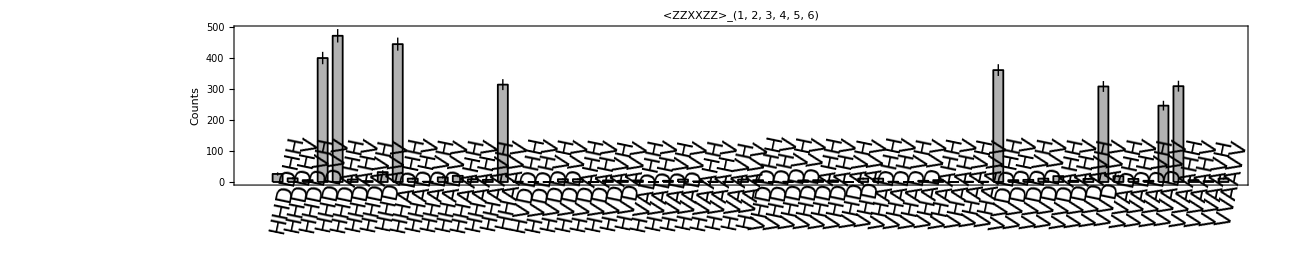
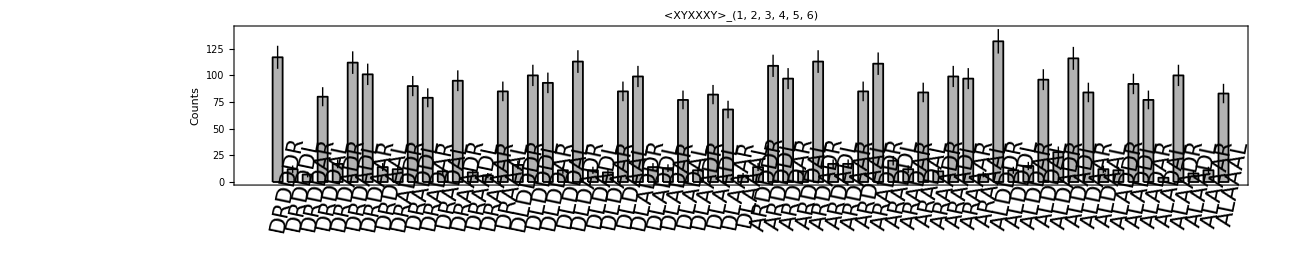
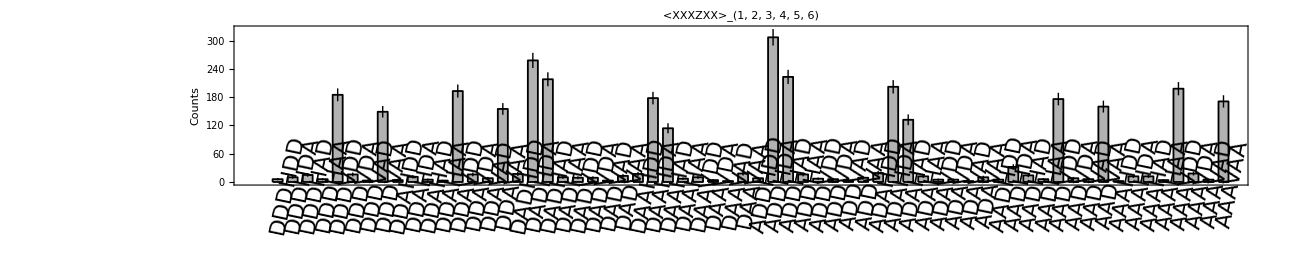
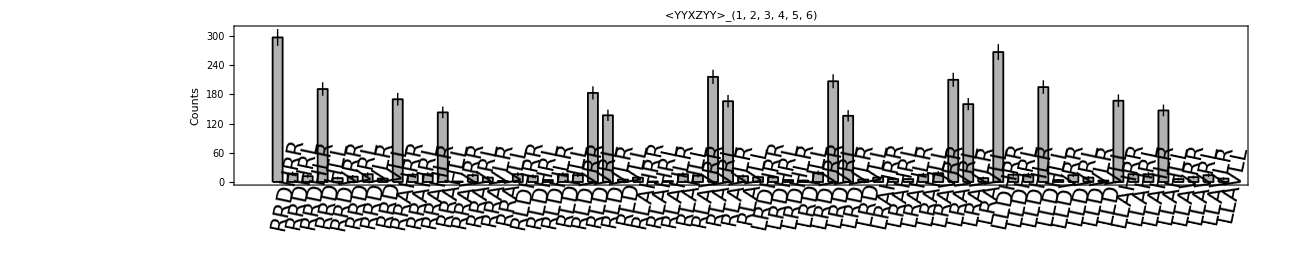
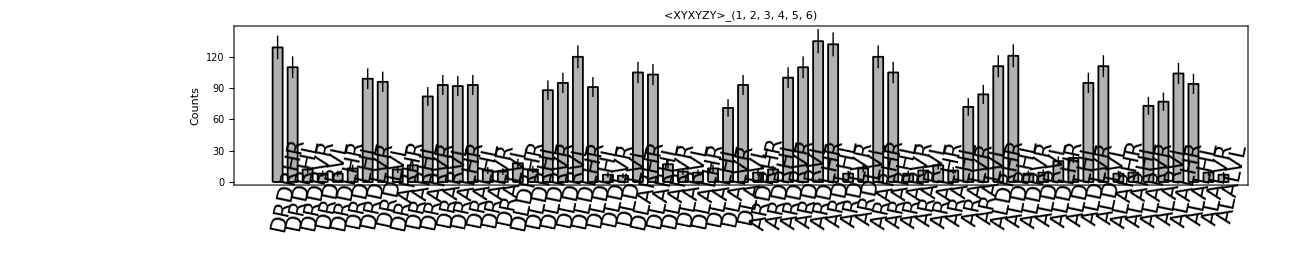
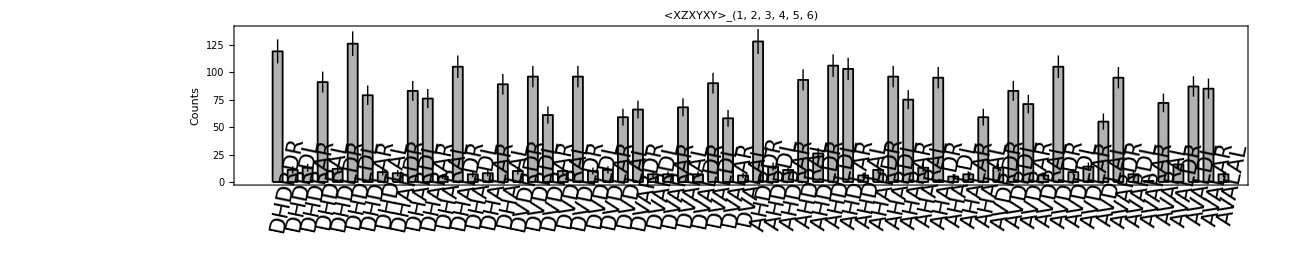

```mathematica
(* settings for plotting and the plots for the above data. This figure is in the supplementary. All the labelling is handled for you, including the labels for the projectors. No need to hard code the labels *)
settingsPlot={Frame->True
,ImageSize->1300
,AspectRatio->1/5
,BarSpacing->Large
,LabelStyle->Directive[
	FontFamily->"Times"
	,FontSize->22
	,Black]
,IntervalMarkers->"Fences"
,ChartStyle->Directive[Darker@Black,Opacity[0.3],EdgeForm[{Black,Thickness[0.001],Opacity[1]}]]};
fullProjections=Table[
Show[
BarChart[
dataPopulations⟦i⟧
,settingsPlot
,ChartLabels->Placed[projectorsPlotLabels⟦i⟧,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,PlotLabel->Style["<"<>projectorsPauliForm⟦i⟧<>">_(1, 2, 3, 4, 5, 6)"
,FontFamily->"Times"
]
,IntervalMarkersStyle->Directive[Darker@Black]
,FrameLabel->{"",Style["Counts",FontFamily->"Times"]}
]
],{i,1,6}]
```

## Conference key agreement via a GHZ state

To see the correlations and evaluate the key rate of NQKD we need to make measurements on the GHZ state that is made when the correct LC operations are applied to the initial state, we need to make projections into the Z and X bases. The observables which do this are ZZXXZZ and XYXXXY. The measurements applied to the state are recurring over time, so the correct observables are the first two observables in each round of six.  
There are some conditions on the measurements. For GHZ state correlations, we need to make sure that upon certain measurement outcomes (in the computational basis) 00, 01, 10 and 11 on qubits 3 and 4, we appropriately apply a bit-flip qubits 5 and 6. This is to coherently disentangle qubits 3 and 4 from the state.

### Data handling

#### Separating measurements

```mathematica
(* all of the projections are assigned to settings. Remember, these are grabbed and converted correctly thanks to the mapping we did earlier. For each observable there are 64 measurement outcomes *)
settings=Partition[measurementSettings,64];
```

```mathematica
(* the first two rows of settings correspond to the projectors which make up the desired observables *)
settingsZZXXZZ=settings⟦1⟧;
settingsXYXXXY=settings⟦2⟧;
```

#### Re-labeling measurements - Changing qubits 3 and 4 into computational basis form

```mathematica
(* re-labelling the projectors so that the labels for qubits 3 and 4 are in the computational basis *)
computationalBasis34=Join[
settingsZZXXZZ⟦;;,{1,2}⟧⟦#⟧,
StringReplace[#,{"h"->"0","v"->"1","d"->"0","a"->"1","r"->"0","l"->"1"}]&/@settingsZZXXZZ⟦;;,{3,4}⟧⟦#⟧,
settingsZZXXZZ⟦;;,{5,6}⟧⟦#⟧
]&/@Range[64];
```

#### Positions of 00, 01, 10 and 11

```mathematica
(* find the positions where post selection criteria is passed *)
positionPostSelect34=Position[computationalBasis34⟦;;,{3,4}⟧,#]&/@Tuples[{"0","1"},2];
```

### GHZ ZZZZ_(1,2,5,6)

#### ZZZZ_(1,2,5,6) flip conditioned on 00 and 11

```mathematica
(* this is hard coded-ish. This could be handled a little neater. On my todo list *)
(* here, we grab the ZZZZ measurements for the GHZ state and label the results based on qubits 3 and 4 measurement outcomes *)
ZZZZ00=settingsZZXXZZ⟦#⟧&/@Flatten@positionPostSelect34⟦1⟧;
ZZZZ01=settingsZZXXZZ⟦#⟧&/@Flatten@positionPostSelect34⟦2⟧;
ZZZZ10=settingsZZXXZZ⟦#⟧&/@Flatten@positionPostSelect34⟦3⟧;
ZZZZ11=settingsZZXXZZ⟦#⟧&/@Flatten@positionPostSelect34⟦4⟧;
```

```mathematica
(* now we flip the results based on 00 and 11 measurement *)
ZZZZ00flip=Join[ZZZZ00⟦;;⟧⟦;;,{1,2,3,4}⟧⟦#⟧,StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@ZZZZ00⟦;;⟧⟦;;,{5,6}⟧⟦#⟧]&/@Range[64/4];
ZZZZ11flip=Join[ZZZZ11⟦;;⟧⟦;;,{1,2,3,4}⟧⟦#⟧,StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@ZZZZ11⟦;;⟧⟦;;,{5,6}⟧⟦#⟧]&/@Range[64/4];
```

```mathematica
(* now, we need to find the index of where the measurement results are for the measurement sets. For conditions 00 and 11 we find the indices for the flipped sets *)
ZZZZ00position=Flatten[Position[settingsZZXXZZ,#]&/@ZZZZ00flip,2];
ZZZZ01position=Flatten[Position[settingsZZXXZZ,#]&/@ZZZZ01,2];
ZZZZ10position=Flatten[Position[settingsZZXXZZ,#]&/@ZZZZ10,2];
ZZZZ11position=Flatten[Position[settingsZZXXZZ,#]&/@ZZZZ11flip,2];
```

#### Counts

```mathematica
(* counts with Poissonian noise *)
countsZZXXZZpostSelect00=Table[#⟦i⟧,{i,ZZZZ00position}]&/@countsZZXXZZpoissonian;
countsZZXXZZpostSelect10=Table[#⟦i⟧,{i,ZZZZ01position}]&/@countsZZXXZZpoissonian;
countsZZXXZZpostSelect01=Table[#⟦i⟧,{i,ZZZZ10position}]&/@countsZZXXZZpoissonian;
countsZZXXZZpostSelect11=Table[#⟦i⟧,{i,ZZZZ11position}]&/@countsZZXXZZpoissonian;
```

```mathematica
(* counts without Poissonian noise *)
countsZZXXZZpostSelect00value=Table[#⟦i⟧,{i,ZZZZ00position}]&/@countsZZXXZZ;
countsZZXXZZpostSelect10value=Table[#⟦i⟧,{i,ZZZZ01position}]&/@countsZZXXZZ;
countsZZXXZZpostSelect01value=Table[#⟦i⟧,{i,ZZZZ10position}]&/@countsZZXXZZ;
countsZZXXZZpostSelect11value=Table[#⟦i⟧,{i,ZZZZ11position}]&/@countsZZXXZZ;
```

```mathematica
(* sum the counts *)
countsZZXXZZpostSelectAll=countsZZXXZZpostSelect00+countsZZXXZZpostSelect01+countsZZXXZZpostSelect10+countsZZXXZZpostSelect11;
countsZZXXZZpostSelectAllvalue=countsZZXXZZpostSelect00value+countsZZXXZZpostSelect01value+countsZZXXZZpostSelect10value+countsZZXXZZpostSelect11value;
```

#### Labels for plotting GHZ state populations

```mathematica
StringReplace[ZZZZ00⟦#⟧⟦{1,2,5,6}⟧,{"h"->"H","d"->"D","a"->"A","v"->"V","r"->"R","l"->"L"}]&/@Range[16];
ZZZZ00labels=StringReplace[ToString[#],{","->""," "->"","{"->"","}"->""}]&/@%;

StringReplace[ZZZZ01⟦#⟧⟦{1,2,5,6}⟧,{"h"->"H","d"->"D","a"->"A","v"->"V","r"->"R","l"->"L"}]&/@Range[16];
ZZZZ01labels=StringReplace[ToString[#],{","->""," "->"","{"->"","}"->""}]&/@%;

StringReplace[ZZZZ10⟦#⟧⟦{1,2,5,6}⟧,{"h"->"H","d"->"D","a"->"A","v"->"V","r"->"R","l"->"L"}]&/@Range[16];
ZZZZ10labels=StringReplace[ToString[#],{","->""," "->"","{"->"","}"->""}]&/@%;

StringReplace[ZZZZ11⟦#⟧⟦{1,2,5,6}⟧,{"h"->"H","d"->"D","a"->"A","v"->"V","r"->"R","l"->"L"}]&/@Range[16];
ZZZZ11labels=StringReplace[ToString[#],{","->""," "->"","{"->"","}"->""}]&/@%;
```

#### ZZZZ_(1,2,5,6)

Some nice plots of the Z correlations. Showing the summed result and all the conditioned results.

```mathematica
scale=Total[Accumulate[countsZZXXZZpostSelectAll]⟦-1⟧];
scale=scale["Value"];
projections=Kronk/@Tuples[{h,v},4];
theoryPopulationsGHZ=Flatten[(#†.GHZ[4])&/@projections]*scale/2 √2;
stackedData={Flatten@theoryPopulationsGHZ,Flatten[Accumulate[countsZZXXZZpostSelectAll]⟦-1⟧]}†;

BarChartSettings={ImageSize->800
,LabelStyle->Directive[FontFamily->"Menlo",FontSize->22,Black]
,ChartStyle->Directive[rocketColors⟦2⟧,Opacity[0.3],EdgeForm[{rocketColors⟦2⟧,Thickness[0.002],Opacity[1]}]]
,IntervalMarkers->"Fences"
,AspectRatio->(1/3)
,Frame->True
,IntervalMarkersStyle->Directive[rocketColors⟦2⟧,Thick]
,FrameLabel->{"",Style["Counts",FontFamily->"Times New Roman"]}
,BarSpacing->Small
};
```

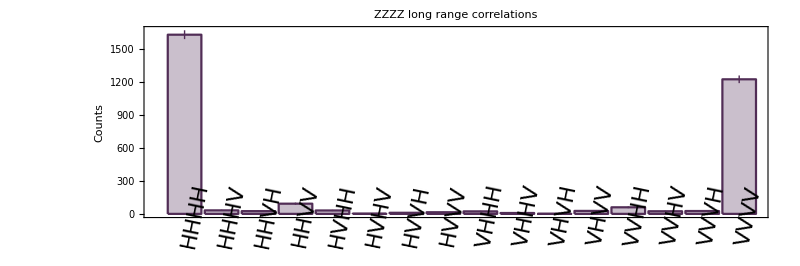

```mathematica
BarChart[Flatten[Accumulate[countsZZXXZZpostSelectAll]⟦-1⟧]
,ChartLabels->Placed[ZZZZ00labels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"ZZZZ long range correlations"]
```

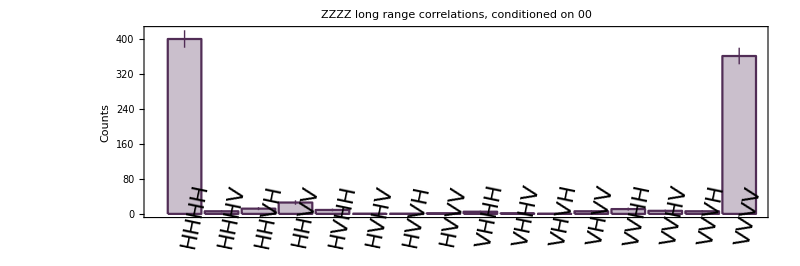

```mathematica
BarChart[Flatten[Accumulate[countsZZXXZZpostSelect00]⟦-1⟧]
,ChartLabels->Placed[ZZZZ00labels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"ZZZZ long range correlations, conditioned on 00"]
```

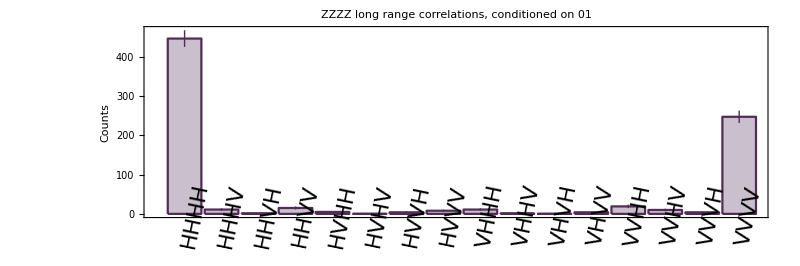

```mathematica
BarChart[Flatten[Accumulate[countsZZXXZZpostSelect01]⟦-1⟧]
,ChartLabels->Placed[ZZZZ01labels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"ZZZZ long range correlations, conditioned on 01"]
```

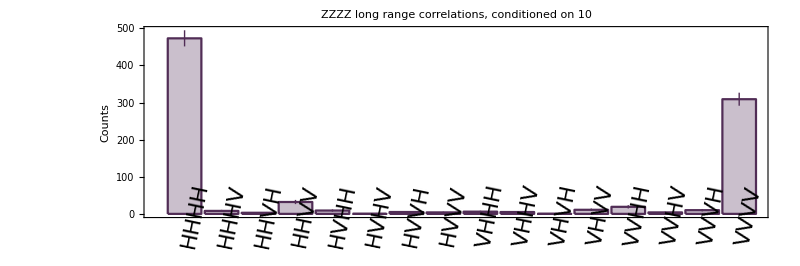

```mathematica
BarChart[Flatten[Accumulate[countsZZXXZZpostSelect10]⟦-1⟧]
,ChartLabels->Placed[ZZZZ10labels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"ZZZZ long range correlations, conditioned on 10"]
```

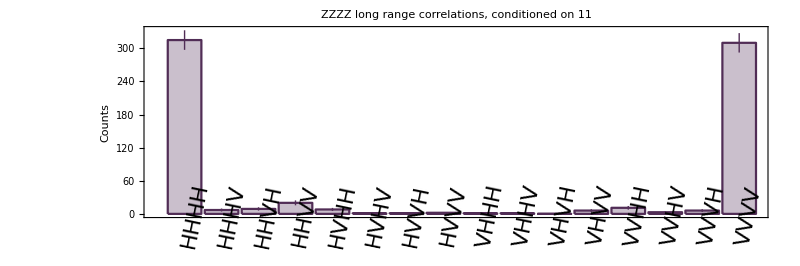

```mathematica
BarChart[Flatten[Accumulate[countsZZXXZZpostSelect11]⟦-1⟧]
,ChartLabels->Placed[ZZZZ11labels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"ZZZZ long range correlations, conditioned on 11"]
```

### GHZ XXXX_(1,2,5,6)

#### XXXX_(1,2,5,6) flip conditioned on 01 and 10

```mathematica
XXXX00=settingsXYXXXY⟦#⟧&/@Flatten@positionPostSelect34⟦1⟧;
XXXX01=settingsXYXXXY⟦#⟧&/@Flatten@positionPostSelect34⟦2⟧;
XXXX10=settingsXYXXXY⟦#⟧&/@Flatten@positionPostSelect34⟦3⟧;
XXXX11=settingsXYXXXY⟦#⟧&/@Flatten@positionPostSelect34⟦4⟧;
```

```mathematica
XXXX01flip=Join[XXXX01⟦;;⟧⟦;;,{1,2,3,4,5}⟧⟦#⟧,StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@XXXX01⟦;;⟧⟦;;,{6}⟧⟦#⟧]&/@Range[64/4];
```

```mathematica
XXXX10flip=Join[XXXX10⟦;;⟧⟦;;,{1,2,3,4,5}⟧⟦#⟧,StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@XXXX10⟦;;⟧⟦;;,{6}⟧⟦#⟧]&/@Range[64/4];
```

```mathematica
XXXX00position=Flatten[Position[settingsXYXXXY,#]&/@XXXX00,2];
XXXX01position=Flatten[Position[settingsXYXXXY,#]&/@XXXX01flip,2];
XXXX10position=Flatten[Position[settingsXYXXXY,#]&/@XXXX10flip,2];
XXXX11position=Flatten[Position[settingsXYXXXY,#]&/@XXXX11,2];
```

#### Counts

```mathematica
countsXYXXXYpostSelect00=Table[#⟦i⟧,{i,XXXX00position}]&/@countsXYXXXYpoissonian;
countsXYXXXYpostSelect01=Table[#⟦i⟧,{i,XXXX01position}]&/@countsXYXXXYpoissonian;
countsXYXXXYpostSelect10=Table[#⟦i⟧,{i,XXXX10position}]&/@countsXYXXXYpoissonian;
countsXYXXXYpostSelect11=Table[#⟦i⟧,{i,XXXX11position}]&/@countsXYXXXYpoissonian;
```

```mathematica
countsXYXXXYpostSelect00value=Table[#⟦i⟧,{i,XXXX00position}]&/@countsXYXXXY;
countsXYXXXYpostSelect01value=Table[#⟦i⟧,{i,XXXX01position}]&/@countsXYXXXY;
countsXYXXXYpostSelect10value=Table[#⟦i⟧,{i,XXXX10position}]&/@countsXYXXXY;
countsXYXXXYpostSelect11value=Table[#⟦i⟧,{i,XXXX11position}]&/@countsXYXXXY;
```

```mathematica
countsXYXXXYpostSelectAll=countsXYXXXYpostSelect00+countsXYXXXYpostSelect01+countsXYXXXYpostSelect10+countsXYXXXYpostSelect11;
countsXYXXXYpostSelectAllvalue=countsXYXXXYpostSelect00value+countsXYXXXYpostSelect01value+countsXYXXXYpostSelect10value+countsXYXXXYpostSelect11value;
```

#### Labels for plotting GHZ state populations

```mathematica
StringReplace[XXXX00⟦#⟧⟦{1,2,5,6}⟧,{"h"->"H","d"->"D","a"->"A","v"->"V","r"->"R","l"->"L"}]&/@Range[16];
XXXX00labels=StringReplace[ToString[#],{","->""," "->"","{"->"","}"->""}]&/@%;

StringReplace[XXXX01⟦#⟧⟦{1,2,5,6}⟧,{"h"->"H","d"->"D","a"->"A","v"->"V","r"->"R","l"->"L"}]&/@Range[16];
XXXX01labels=StringReplace[ToString[#],{","->""," "->"","{"->"","}"->""}]&/@%;

StringReplace[XXXX10⟦#⟧⟦{1,2,5,6}⟧,{"h"->"H","d"->"D","a"->"A","v"->"V","r"->"R","l"->"L"}]&/@Range[16];
XXXX10labels=StringReplace[ToString[#],{","->""," "->"","{"->"","}"->""}]&/@%;

StringReplace[XXXX11⟦#⟧⟦{1,2,5,6}⟧,{"h"->"H","d"->"D","a"->"A","v"->"V","r"->"R","l"->"L"}]&/@Range[16];
XXXX11labels=StringReplace[ToString[#],{","->""," "->"","{"->"","}"->""}]&/@%;
```

#### XXXX_(1,2,5,6)

```mathematica
scale=Total[Accumulate[countsXYXXXYpostSelectAll]⟦-1⟧];
scale=scale["Value"];
projections=Kronk/@Tuples[{d,a},4];
theoryPopulationsGHZ=Flatten[(#†.GHZ[4])&/@projections]*scale/4 √2;
stackedData={Flatten@theoryPopulationsGHZ,Flatten[Accumulate[countsXYXXXYpostSelectAll]⟦-1⟧]}†;
```

```mathematica
BarChartSettings={ImageSize->800
,LabelStyle->Directive[FontFamily->"Menlo",FontSize->22,Black]
,ChartStyle->Directive[rocketColors⟦5⟧,Opacity[0.3],EdgeForm[{rocketColors⟦5⟧,Thickness[0.003],Opacity[1]}]]
,IntervalMarkers->"Fences"
,AspectRatio->1/3
,Frame->True
,IntervalMarkersStyle->Directive[rocketColors⟦5⟧,Thick]
,FrameLabel->{"",Style["Counts",FontFamily->"Times New Roman"]}
};
```

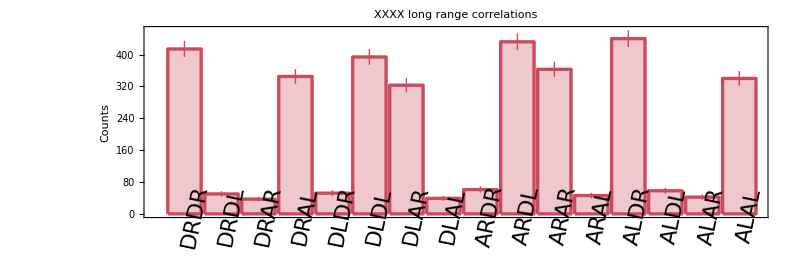

```mathematica
BarChart[Flatten[Accumulate[countsXYXXXYpostSelectAll]⟦-1⟧]
,ChartLabels->Placed[XXXX00labels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"XXXX long range correlations"]
```

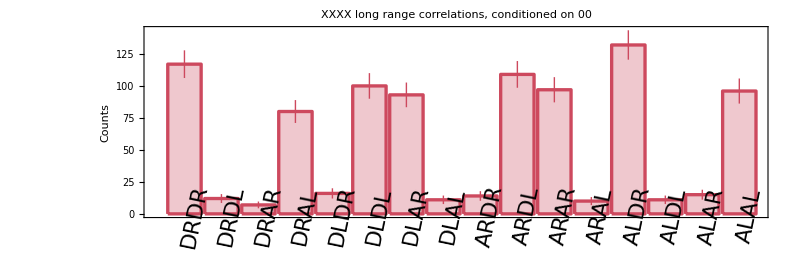

```mathematica
BarChart[Flatten[Accumulate[countsXYXXXYpostSelect00]⟦-1⟧]
,ChartLabels->Placed[XXXX00labels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"XXXX long range correlations, conditioned on 00"]
```

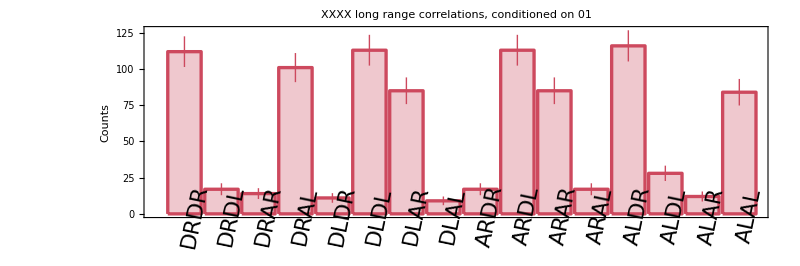

```mathematica
BarChart[Flatten[Accumulate[countsXYXXXYpostSelect01]⟦-1⟧]
,ChartLabels->Placed[XXXX01labels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"XXXX long range correlations, conditioned on 01"]
```

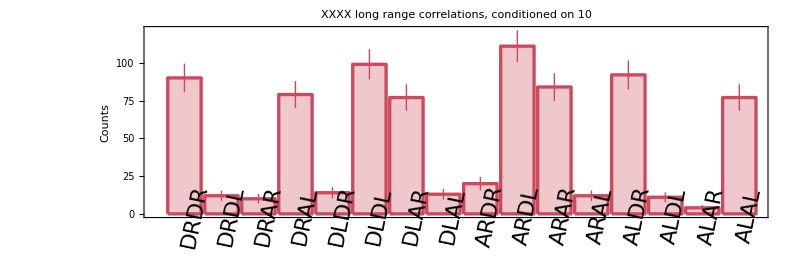

```mathematica
BarChart[Flatten[Accumulate[countsXYXXXYpostSelect10]⟦-1⟧]
,ChartLabels->Placed[XXXX10labels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"XXXX long range correlations, conditioned on 10"]
```

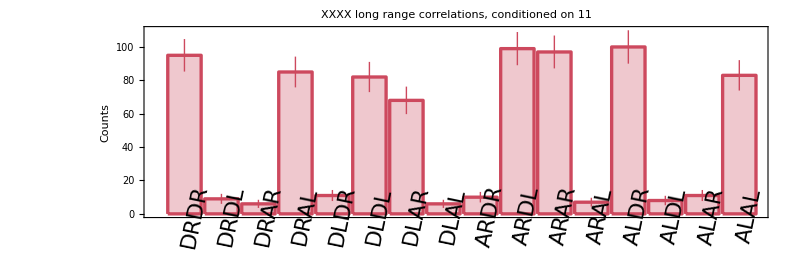

```mathematica
BarChart[Flatten[Accumulate[countsXYXXXYpostSelect11]⟦-1⟧]
,ChartLabels->Placed[XXXX11labels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"XXXX long range correlations, conditioned on 11"]
```

### Rates of CKA via GHZ state

#### Correct normalisation of data

We are going to carry through two versions of the same result, one with error and one without error. This is because the Around[ ] functionality does not behave well when parsed into other functions, in particular Max[ ]. These need to be normalized appropriately.

```mathematica
accumulatedDataZZXXZZ=Accumulate@countsZZXXZZpostSelectAllvalue;
accumulatedDataZZXXZZerror=countsZZXXZZpostSelectAll;
```

```mathematica
accumulatedDataXYXXXY=Accumulate@countsXYXXXYpostSelectAllvalue;
accumulatedDataXYXXXYerror=countsXYXXXYpostSelectAll;
```

```mathematica
(* normalise the data *)
accumulatedDataZZXXZZnorm=N@accumulatedDataZZXXZZ⟦#⟧/Total[accumulatedDataZZXXZZ⟦#⟧]&/@Range@Length@accumulatedDataZZXXZZ;
accumulatedDataZZXXZZnormError=N@accumulatedDataZZXXZZerror/Total[accumulatedDataZZXXZZerror,2];

accumulatedDataXYXXXYnorm=N@accumulatedDataXYXXXY⟦#⟧/Total[accumulatedDataXYXXXY⟦#⟧]&/@Range@Length@accumulatedDataXYXXXY;
accumulatedDataXYXXXYnormError=N@accumulatedDataXYXXXYerror/Total[accumulatedDataXYXXXYerror,2];
```

#### Q_Z

```mathematica
(* Disparity in first and second index *)
QAB1=N@Total[Table[#⟦i⟧,{i,{5,6,7,8,9,10,11,12}}]]&/@accumulatedDataZZXXZZnorm;
QAB1Error=N@Total[Table[#⟦i⟧,{i,{5,6,7,8,9,10,11,12}}]]&/@accumulatedDataZZXXZZnormError;
```

```mathematica
(* Disparity in first and third index *)
QAB2=N@Total[Table[#⟦i⟧,{i,{3,4,7,8,9,10,13,14}}]]&/@accumulatedDataZZXXZZnorm;
QAB2Error=N@Total[Table[#⟦i⟧,{i,{3,4,7,8,9,10,13,14}}]]&/@accumulatedDataZZXXZZnormError;
```

```mathematica
(* Disparity in first and fourth index *)
QAB3=N@Total[Table[#⟦i⟧,{i,{2,4,6,8,9,11,13,15}}]]&/@accumulatedDataZZXXZZnorm;
QAB3Error=N@Total[Table[#⟦i⟧,{i,{2,4,6,8,9,11,13,15}}]]&/@accumulatedDataZZXXZZnormError;
```

```mathematica
(* Max does not appear to work with Around function,but can use Max to find the index of the data point that is maximum *)
maxValues=Max[{QAB1⟦#⟧,QAB2⟦#⟧,QAB3⟦#⟧}]&/@Range@Length@QAB1;
```

```mathematica
(* Some of the values have the same max values so we need to make sure we only take one position corresponding to a max value *)
maxValuesPosition=Position[{QAB1⟦#⟧,QAB2⟦#⟧,QAB3⟦#⟧},maxValues⟦#⟧]&/@Range@Length@QAB1;
maxValuesPosition=Flatten[#⟦1⟧&/@maxValuesPosition];
```

```mathematica
(*Note QzAll and QzAllError are the two versions of the same result carried through,one with error and one without *)
QzAll={QAB1⟦#⟧,QAB2⟦#⟧,QAB3⟦#⟧}&/@Range@Length@QAB1;
QzAllError={QAB1Error,QAB2Error,QAB3Error};
```

```mathematica
(* position of the maximum error in the Z basis *)
QzAllErrorPosition=Flatten@Position[Flatten[QzAllError]⟦;;,1⟧,Max[Flatten[QzAllError]⟦;;,1⟧]];
```

```mathematica
(* note that this  is the Qz value for each round of results. So if you want the Qz after accumulating all of the data, you need to take the final result of this array i.e. Qz⟦-1⟧ is the value we desire, but you might be interested to see how Qz changes as more data is gathered *)
Qz=QzAll⟦#⟧⟦maxValuesPosition⟦#⟧⟧&/@Range@Length@maxValuesPosition;
```

```mathematica
(* Qz, error *)
QzError=QzAllError⟦QzAllErrorPosition⟧;
{QzAllError⟦QzAllErrorPosition⟧⟦1,1,1⟧,QzAllError⟦QzAllErrorPosition⟧⟦1,1,2⟧}
```

{0.0796788,0.00500306}

#### Q_X

Evaluating Qx is done by computing by evaluating (1 - (QxPositive - QxNegative)/ (QxPositive + QxNegative)) / 2

```mathematica
(* based on the parity of the projection being made. Positive parity *)
Qxpositive=N@Total[Table[#⟦i⟧,{i,{1,4,6,7,10,11,13,16}}]]&/@accumulatedDataXYXXXYnormError
```

{0.8880.017}

```mathematica
(* based on the parity of the projection being made. Negative parity *)
Qxnegative=N@Total[Table[#⟦i⟧,{i,{2,3,5,8,9,12,14,15}}]]&/@accumulatedDataXYXXXYnormError
```

{0.1120.006}

```mathematica
(* Qx, error *)
QxError=((1-(Qxpositive⟦#⟧-Qxnegative⟦#⟧)/(Qxnegative⟦#⟧+Qxpositive⟦#⟧))/2)&/@Range[Length@Qxpositive];
Qx=%⟦1,1⟧;
{QxError⟦1,1⟧,QxError⟦1,2⟧}
```

{0.112049,0.0113303}

#### AKR

```mathematica
(* RESULT *)
```

```mathematica
akr=1-entropy[Qx]-entropy[Qz⟦-1⟧]
```

0.0928883

#### Errors

Adding Monte Carlo simulation here based on randomly sampling the data, this time randomly assigned to a value which is within the range defined by the Poissonian uncertainty.

QBER

```mathematica
upperBound=QzError⟦1,1,1⟧+QzError⟦1,1,2⟧;
lowerBound=QzError⟦1,1,1⟧-QzError⟦1,1,2⟧;
```

```mathematica
errorArrayQBER=Range[lowerBound,upperBound,(upperBound-lowerBound)/1999];
errorArrayQBERsample=Table[RandomSample[errorArrayQBER,1],{i,1,2000}];
```

Qx

```mathematica
upperBound=QxError⟦1,1⟧+QxError⟦1,2⟧;
lowerBound=QxError⟦1,1⟧-QxError⟦1,2⟧;
```

```mathematica
errorArrayQx=Range[lowerBound,upperBound,(upperBound-lowerBound)/1999];
```

```mathematica
errorArrayQxsample=Table[RandomSample[errorArrayQx,1],{i,1,2000}];
```

AKR

```mathematica
akrArray=1-entropy[errorArrayQxsample⟦#⟧]-entropy[errorArrayQBERsample⟦#⟧]&/@Range[2000];
```

```mathematica
akrStandardDeviation=StandardDeviation[Flatten@akrArray]
akrValue=Mean[Flatten@akrArray]
```

0.0220441

0.0932058

#### Summary

```mathematica
(* RESULT *)
```

```mathematica
{{"QBER","+-","Qx","+-","AKR","+-"},{QzError⟦-1⟧⟦1,1⟧,QzError⟦-1⟧⟦1,2⟧,QxError⟦1,1⟧,QxError⟦1,2⟧,akr,akrStandardDeviation}}//TableForm
```

QBER | +- | Qx | +- | AKR | +-
0.0796788 | 0.00500306 | 0.112049 | 0.0113303 | 0.0928883 | 0.0220441

## Conference key agreement via sets of Bell states

Similar to how there are conditional operations that require bit flips on the state to attain correct GHZ state correlations, the same occurs for Bell pairs. This is to coherently disentangle those users (qubits) not sharing the state, from the state without affecting the Bell correlations. There are three Bell states which we obtain from two sets of observables. The first set of observables allow us to measured two Bell states in the Z and X basis simultaneously. A final set of observables lets us see the correlations of the remaining Bell state. If this is not clear, then have a look at Figure 2 of the paper.

### Data handling

#### Separating measurements

```mathematica
(*Bell state 12 and 56*)
settingsXXXZXX=settings⟦3⟧;
settingsYYXZYY=settings⟦4⟧;
(*Bell state 25*)
settingsXYXYZY=settings⟦5⟧;
settingsXZXYXY=settings⟦6⟧;
```

#### Re-labeling measurements to computational basis form

```mathematica
(* expressing projections in computational basis form *)
computationalBasis=Join[

StringReplace[#,{"h"->"0","v"->"1","d"->"0","a"->"1","r"->"0","l"->"1"}]&/@settingsXYXYZY⟦;;,{1,2,3,4,5,6}⟧⟦#⟧

]&/@Range[64];
```

#### Positions of 0000, 0001, 0010, 0011, 0100, 1000, 1100 in different combinations of qubits

The subsection title explains what is going on here

```mathematica
positionPostSelect3456=Position[computationalBasis⟦;;,{3,4,5,6}⟧,#]&/@Tuples[{"0","1"},4];
```

```mathematica
positionPostSelect1234=Position[computationalBasis⟦;;,{1,2,3,4}⟧,#]&/@Tuples[{"0","1"},4];
```

```mathematica
positionPostSelect1346=Position[computationalBasis⟦;;,{1,3,4,6}⟧,#]&/@Tuples[{"0","1"},4];
```

#### Post selecting

A rather horrible way to do this, but it works

```mathematica
postSelect00003456=positionPostSelect3456⟦1⟧;
postSelect00013456=positionPostSelect3456⟦2⟧;
postSelect00103456=positionPostSelect3456⟦3⟧;
postSelect00113456=positionPostSelect3456⟦4⟧;
postSelect01003456=positionPostSelect3456⟦5⟧;
postSelect01013456=positionPostSelect3456⟦6⟧;
postSelect01103456=positionPostSelect3456⟦7⟧;
postSelect01113456=positionPostSelect3456⟦8⟧;
postSelect10003456=positionPostSelect3456⟦9⟧;
postSelect10013456=positionPostSelect3456⟦10⟧;
postSelect10103456=positionPostSelect3456⟦11⟧;
postSelect10113456=positionPostSelect3456⟦12⟧;
postSelect11003456=positionPostSelect3456⟦13⟧;
postSelect11013456=positionPostSelect3456⟦14⟧;
postSelect11103456=positionPostSelect3456⟦15⟧;
postSelect11113456=positionPostSelect3456⟦16⟧;
```

```mathematica
postSelect00001234=positionPostSelect1234⟦1⟧;
postSelect00011234=positionPostSelect1234⟦2⟧;
postSelect00101234=positionPostSelect1234⟦3⟧;
postSelect00111234=positionPostSelect1234⟦4⟧;
postSelect01001234=positionPostSelect1234⟦5⟧;
postSelect01011234=positionPostSelect1234⟦6⟧;
postSelect01101234=positionPostSelect1234⟦7⟧;
postSelect01111234=positionPostSelect1234⟦8⟧;
postSelect10001234=positionPostSelect1234⟦9⟧;
postSelect10011234=positionPostSelect1234⟦10⟧;
postSelect10101234=positionPostSelect1234⟦11⟧;
postSelect10111234=positionPostSelect1234⟦12⟧;
postSelect11001234=positionPostSelect1234⟦13⟧;
postSelect11011234=positionPostSelect1234⟦14⟧;
postSelect11101234=positionPostSelect1234⟦15⟧;
postSelect11111234=positionPostSelect1234⟦16⟧;
```

```mathematica
postSelect…0000…1346=positionPostSelect1346⟦1⟧;
postSelect…0001…1346=positionPostSelect1346⟦2⟧;
postSelect…0010…1346=positionPostSelect1346⟦3⟧;
postSelect…0011…1346=positionPostSelect1346⟦4⟧;
postSelect…0100…1346=positionPostSelect1346⟦5⟧;
postSelect…0101…1346=positionPostSelect1346⟦6⟧;
postSelect…0110…1346=positionPostSelect1346⟦7⟧;
postSelect…0111…1346=positionPostSelect1346⟦8⟧;
postSelect…1000…1346=positionPostSelect1346⟦9⟧;
postSelect…1001…1346=positionPostSelect1346⟦10⟧;
postSelect…1010…1346=positionPostSelect1346⟦11⟧;
postSelect…1011…1346=positionPostSelect1346⟦12⟧;
postSelect…1100…1346=positionPostSelect1346⟦13⟧;
postSelect…1101…1346=positionPostSelect1346⟦14⟧;
postSelect…1110…1346=positionPostSelect1346⟦15⟧;
postSelect…1111…1346=positionPostSelect1346⟦16⟧;
```

### Bell ZZ_(1,2) XXXZXX

#### ZZ_(1,2) flip conditioned on 00 and 10

Obtaining the index for the conditional formatting. Recall that we require a flip on qubits 2 and 6 whenever we measure 01 and 11 in qubits 3 and 4.

```mathematica
ZZ0000Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect00003456;
ZZ0001Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect00013456;
ZZ0010Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect00103456;
ZZ0011Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect00113456;
```

```mathematica
ZZ0100Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect01003456;
ZZ0101Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect01013456;
ZZ0110Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect01103456;
ZZ0111Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect01113456;
```

```mathematica
ZZ1000Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect10003456;
ZZ1001Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect10013456;
ZZ1010Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect10103456;
ZZ1011Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect10113456;
```

```mathematica
ZZ1100Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect11003456;
ZZ1101Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect11013456;
ZZ1110Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect11103456;
ZZ1111Bell12=settingsXXXZXX⟦#⟧&/@Flatten@postSelect11113456;
```

This time defining a function for perform flips

```mathematica
FlipQubit26[meas_]:=
Join[
meas⟦;;,{1}⟧⟦#⟧,
StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@meas⟦;;,{2}⟧⟦#⟧,
meas⟦;;,{3,4,5}⟧⟦#⟧,
StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@meas⟦;;,{6}⟧⟦#⟧
]&/@Range[Length@meas]
```

Using function defined above to perform flips

```mathematica
ZZ0000Bell12flip=FlipQubit26[ZZ0000Bell12];
ZZ0001Bell12flip=FlipQubit26[ZZ0001Bell12];
ZZ0010Bell12flip=FlipQubit26[ZZ0010Bell12];
ZZ0011Bell12flip=FlipQubit26[ZZ0011Bell12];
```

```mathematica
ZZ1000Bell12flip=FlipQubit26[ZZ1000Bell12];
ZZ1001Bell12flip=FlipQubit26[ZZ1001Bell12];
ZZ1010Bell12flip=FlipQubit26[ZZ1010Bell12];
ZZ1011Bell12flip=FlipQubit26[ZZ1011Bell12];
```

```mathematica
(* positions of the data we desire *)
ZZ0000Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0000Bell12flip,2]
ZZ0001Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0001Bell12flip,2]
ZZ0010Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0010Bell12flip,2]
ZZ0011Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0011Bell12flip,2]

ZZ0100Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0100Bell12,2]
ZZ0101Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0101Bell12,2]
ZZ0110Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0110Bell12,2]
ZZ0111Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0111Bell12,2]

ZZ1000Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1000Bell12flip,2]
ZZ1001Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1010Bell12flip,2]
ZZ1010Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1001Bell12flip,2]
ZZ1011Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1011Bell12flip,2]

ZZ1100Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1100Bell12,2]
ZZ1101Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1101Bell12,2]
ZZ1110Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1110Bell12,2]
ZZ1111Bell12position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1111Bell12,2]
```

{18,2,50,34}

{17,1,49,33}

{20,4,52,36}

{19,3,51,35}

{5,21,37,53}

{6,22,38,54}

{7,23,39,55}

{8,24,40,56}

{26,10,58,42}

{28,12,60,44}

{25,9,57,41}

{27,11,59,43}

{13,29,45,61}

{14,30,46,62}

{15,31,47,63}

{16,32,48,64}

#### Counts

00_(3,4)

```mathematica
countsXXXZXXpostSelect0000=Table[#⟦i⟧,{i,ZZ0000Bell12position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect0001=Table[#⟦i⟧,{i,ZZ0001Bell12position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect0010=Table[#⟦i⟧,{i,ZZ0010Bell12position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect0011=Table[#⟦i⟧,{i,ZZ0011Bell12position}]&/@countsXXXZXXpoissonian;

countsXXXZXXpostSelect0000value=Table[#⟦i⟧,{i,ZZ0000Bell12position}]&/@countsXXXZXX;
countsXXXZXXpostSelect0001value=Table[#⟦i⟧,{i,ZZ0001Bell12position}]&/@countsXXXZXX;
countsXXXZXXpostSelect0010value=Table[#⟦i⟧,{i,ZZ0010Bell12position}]&/@countsXXXZXX;
countsXXXZXXpostSelect0011value=Table[#⟦i⟧,{i,ZZ0011Bell12position}]&/@countsXXXZXX;
```

01_(3,4)

```mathematica
countsXXXZXXpostSelect0100=Table[#⟦i⟧,{i,ZZ0100Bell12position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect0101=Table[#⟦i⟧,{i,ZZ0101Bell12position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect0110=Table[#⟦i⟧,{i,ZZ0110Bell12position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect0111=Table[#⟦i⟧,{i,ZZ0111Bell12position}]&/@countsXXXZXXpoissonian;

countsXXXZXXpostSelect0100value=Table[#⟦i⟧,{i,ZZ0100Bell12position}]&/@countsXXXZXX;
countsXXXZXXpostSelect0101value=Table[#⟦i⟧,{i,ZZ0101Bell12position}]&/@countsXXXZXX;
countsXXXZXXpostSelect0110value=Table[#⟦i⟧,{i,ZZ0110Bell12position}]&/@countsXXXZXX;
countsXXXZXXpostSelect0111value=Table[#⟦i⟧,{i,ZZ0111Bell12position}]&/@countsXXXZXX;
```

10_(3,4)

```mathematica
countsXXXZXXpostSelect1000=Table[#⟦i⟧,{i,ZZ1000Bell12position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect1001=Table[#⟦i⟧,{i,ZZ1001Bell12position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect1010=Table[#⟦i⟧,{i,ZZ1010Bell12position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect1011=Table[#⟦i⟧,{i,ZZ1011Bell12position}]&/@countsXXXZXXpoissonian;

countsXXXZXXpostSelect1000value=Table[#⟦i⟧,{i,ZZ1000Bell12position}]&/@countsXXXZXX;
countsXXXZXXpostSelect1001value=Table[#⟦i⟧,{i,ZZ1001Bell12position}]&/@countsXXXZXX;
countsXXXZXXpostSelect1010value=Table[#⟦i⟧,{i,ZZ1010Bell12position}]&/@countsXXXZXX;
countsXXXZXXpostSelect1011value=Table[#⟦i⟧,{i,ZZ1011Bell12position}]&/@countsXXXZXX;
```

11_(3,4)

```mathematica
countsXXXZXXpostSelect1100=Table[#⟦i⟧,{i,ZZ1100Bell12position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect1101=Table[#⟦i⟧,{i,ZZ1101Bell12position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect1110=Table[#⟦i⟧,{i,ZZ1110Bell12position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect1111=Table[#⟦i⟧,{i,ZZ1111Bell12position}]&/@countsXXXZXXpoissonian;

countsXXXZXXpostSelect1100value=Table[#⟦i⟧,{i,ZZ1100Bell12position}]&/@countsXXXZXX;
countsXXXZXXpostSelect1101value=Table[#⟦i⟧,{i,ZZ1101Bell12position}]&/@countsXXXZXX;
countsXXXZXXpostSelect1110value=Table[#⟦i⟧,{i,ZZ1110Bell12position}]&/@countsXXXZXX;
countsXXXZXXpostSelect1111value=Table[#⟦i⟧,{i,ZZ1111Bell12position}]&/@countsXXXZXX;
```

Now that we shuffled the data around to define variables associated to all the different combination of post selections, now we can sum the appropriate counts together. Bear in mind that the plots following all this shuffling around will let us know if the process has been done correctly.

```mathematica
(* with error *)
```

```mathematica
countsXXXZXXpostSelectAll=(countsXXXZXXpostSelect0000+countsXXXZXXpostSelect0001+countsXXXZXXpostSelect0010+countsXXXZXXpostSelect0011+countsXXXZXXpostSelect0100+countsXXXZXXpostSelect0101+countsXXXZXXpostSelect0110+countsXXXZXXpostSelect0111+countsXXXZXXpostSelect1000+countsXXXZXXpostSelect1001+countsXXXZXXpostSelect1010+countsXXXZXXpostSelect1011+countsXXXZXXpostSelect1100+countsXXXZXXpostSelect1101+countsXXXZXXpostSelect1110+countsXXXZXXpostSelect1111);
```

```mathematica
countsXXXZXXpostSelect00=countsXXXZXXpostSelect0000+countsXXXZXXpostSelect0001+countsXXXZXXpostSelect0010+countsXXXZXXpostSelect0011;
countsXXXZXXpostSelect01=countsXXXZXXpostSelect0100+countsXXXZXXpostSelect0101+countsXXXZXXpostSelect0110+countsXXXZXXpostSelect0111;
countsXXXZXXpostSelect10=countsXXXZXXpostSelect1000+countsXXXZXXpostSelect1001+countsXXXZXXpostSelect1010+countsXXXZXXpostSelect1011;
countsXXXZXXpostSelect11=countsXXXZXXpostSelect1100+countsXXXZXXpostSelect1101+countsXXXZXXpostSelect1110+countsXXXZXXpostSelect1111;
```

```mathematica
(* without error *)
```

```mathematica
countsXXXZXXpostSelectAllvalue=(countsXXXZXXpostSelect0000value+countsXXXZXXpostSelect0001value+countsXXXZXXpostSelect0010value+countsXXXZXXpostSelect0011value)+(countsXXXZXXpostSelect0100value+countsXXXZXXpostSelect0101value+countsXXXZXXpostSelect0110value+countsXXXZXXpostSelect0111value)+(countsXXXZXXpostSelect1000value+countsXXXZXXpostSelect1001value+countsXXXZXXpostSelect1010value+countsXXXZXXpostSelect1011value)+(countsXXXZXXpostSelect1100value+countsXXXZXXpostSelect1101value+countsXXXZXXpostSelect1110value+countsXXXZXXpostSelect1111value);
```

```mathematica
countsXXXZXXpostSelect00value=countsXXXZXXpostSelect0000value+countsXXXZXXpostSelect0001value+countsXXXZXXpostSelect0010value+countsXXXZXXpostSelect0011value;
countsXXXZXXpostSelect01value=countsXXXZXXpostSelect0100value+countsXXXZXXpostSelect0101value+countsXXXZXXpostSelect0110value+countsXXXZXXpostSelect0111value;
countsXXXZXXpostSelect10value=countsXXXZXXpostSelect1000value+countsXXXZXXpostSelect1001value+countsXXXZXXpostSelect1010value+countsXXXZXXpostSelect1011value;
countsXXXZXXpostSelect11value=countsXXXZXXpostSelect1100value+countsXXXZXXpostSelect1101value+countsXXXZXXpostSelect1110value+countsXXXZXXpostSelect1111value;
```

#### Labels for plotting Bell state populations

```mathematica
bellLabels=Tuples[{"H","V"},2];
bellLabels=StringReplace[ToString[#],{","->""," "->"","{"->"","}"->""}]&/@%;
```

#### ZZ_(1,2)

```mathematica
(* some useful variables for generating plots *)
scale=Total[Accumulate[countsXXXZXXpostSelectAll]⟦-1⟧];
scale=scale["Value"];
phiplus=1/√2(Kron[h,h]+Kron[v,v]);
projections=Kronk/@Tuples[{h,v},2];
theoryPopulationsGHZ=Flatten[(#†.phiplus)&/@projections]*scale/√2;
stackedData={Flatten@theoryPopulationsGHZ,Flatten[Accumulate[countsXXXZXXpostSelectAll]⟦-1⟧]}†;
```

```mathematica
BarChartSettings={ImageSize->400
,LabelStyle->Directive[FontFamily->"Menlo",FontSize->22,Black]
,ChartStyle->Directive[rocketColors⟦2⟧,Opacity[0.3],EdgeForm[{rocketColors⟦2⟧,Thickness[0.003],Opacity[1]}]]
,IntervalMarkers->"Fences"
,AspectRatio->1/2
,Frame->True
,IntervalMarkersStyle->Directive[rocketColors⟦2⟧,Thick]
,FrameLabel->{"",Style["Counts",FontFamily->"Times New Roman"]}
};
```

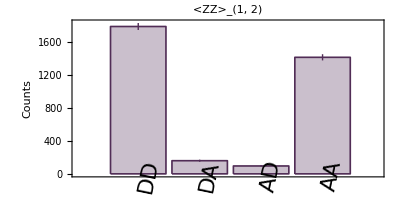

```mathematica
BarChart[Flatten[Accumulate[countsXXXZXXpostSelectAll]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(1, 2)"]
```

Conditional plots

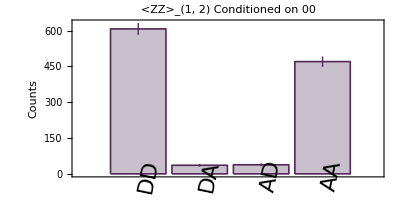

```mathematica
BarChart[Flatten[Accumulate[countsXXXZXXpostSelect00]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(1, 2) Conditioned on 00"]
```

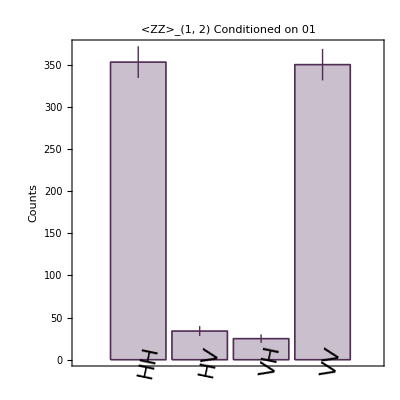

```mathematica
BarChart[Flatten[Accumulate[countsXXXZXXpostSelect01]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(1, 2) Conditioned on 01"]
```

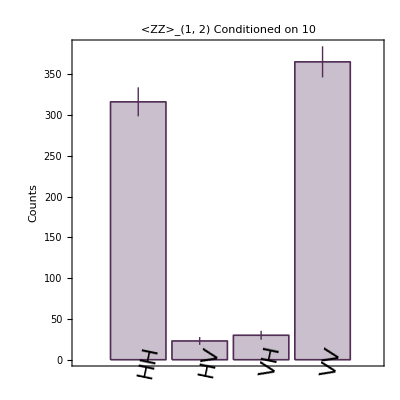

```mathematica
BarChart[Flatten[Accumulate[countsXXXZXXpostSelect10]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(1, 2) Conditioned on 10"]
```

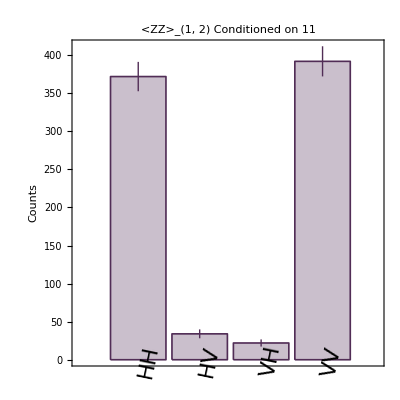

```mathematica
BarChart[Flatten[Accumulate[countsXXXZXXpostSelect11]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(1, 2) Conditioned on 11"]
```

### Bell XX_(1,2) YYXZYY

#### XX_(1,2) data, flip conditioned on 01 and 11

01 and 11 flip

Obtaining the index for the conditional formatting. Recall that we require a flip on qubits 5 and 6 whenever we measure 01 and 11 in qubits 3 and 4.

```mathematica
XX0000Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect00003456;
XX0001Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect00013456;
XX0010Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect00103456;
XX0011Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect00113456;
```

```mathematica
XX0100Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect01003456;
XX0101Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect01013456;
XX0110Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect01103456;
XX0111Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect01113456;
```

```mathematica
XX1000Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect10003456;
XX1001Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect10013456;
XX1010Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect10103456;
XX1011Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect10113456;
```

```mathematica
XX1100Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect11003456;
XX1101Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect11013456;
XX1110Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect11103456;
XX1111Bell12=settingsYYXZYY⟦#⟧&/@Flatten@postSelect11113456;
```

Function for performing flips

```mathematica
FlipQubit26[meas_]:=
Join[
meas⟦;;,{1}⟧⟦#⟧,
StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@meas⟦;;,{2}⟧⟦#⟧,
meas⟦;;,{3,4,5}⟧⟦#⟧,
StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@meas⟦;;,{6}⟧⟦#⟧
]&/@Range[Length@meas]
```

Using function defined above to perform flips

```mathematica
XX0000Bell12flip=FlipQubit26[XX0000Bell12];
XX0001Bell12flip=FlipQubit26[XX0001Bell12];
XX0010Bell12flip=FlipQubit26[XX0010Bell12];
XX0011Bell12flip=FlipQubit26[XX0011Bell12];
```

```mathematica
XX0100Bell12flip=FlipQubit26[XX0100Bell12];
XX0101Bell12flip=FlipQubit26[XX0101Bell12];
XX0110Bell12flip=FlipQubit26[XX0110Bell12];
XX0111Bell12flip=FlipQubit26[XX0111Bell12];
```

```mathematica
XX1000Bell12flip=FlipQubit26@XX1000Bell12;
XX1001Bell12flip=FlipQubit26@XX1001Bell12;
XX1010Bell12flip=FlipQubit26@XX1010Bell12;
XX1011Bell12flip=FlipQubit26@XX1011Bell12;
```

```mathematica
XX1100Bell12flip=FlipQubit26@XX1100Bell12;
XX1101Bell12flip=FlipQubit26@XX1101Bell12;
XX1110Bell12flip=FlipQubit26@XX1110Bell12;
XX1111Bell12flip=FlipQubit26@XX1111Bell12;
```

```mathematica
(* positions of the data we desire *)
XX0000Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX0000Bell12,2]
XX0001Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX0001Bell12,2]
XX0010Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX0010Bell12,2]
XX0011Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX0011Bell12,2]

XX0100Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX0100Bell12flip,2]
XX0101Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX0101Bell12flip,2]
XX0110Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX0110Bell12flip,2]
XX0111Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX0111Bell12flip,2]

XX1000Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX1000Bell12,2]
XX1001Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX1010Bell12,2]
XX1010Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX1001Bell12,2]
XX1011Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX1011Bell12,2]

XX1100Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX1100Bell12flip,2]
XX1101Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX1101Bell12flip,2]
XX1110Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX1110Bell12flip,2]
XX1111Bell12position=Flatten[Position[settingsYYXZYY,#]&/@XX1111Bell12flip,2]
```

{1,17,33,49}

{2,18,34,50}

{3,19,35,51}

{4,20,36,52}

{22,6,54,38}

{21,5,53,37}

{24,8,56,40}

{23,7,55,39}

{9,25,41,57}

{11,27,43,59}

{10,26,42,58}

{12,28,44,60}

{30,14,62,46}

{29,13,61,45}

{32,16,64,48}

{31,15,63,47}

#### Counts

00_(3,4)

```mathematica
countsYYXZYYpostSelect0000=Table[#⟦i⟧,{i,XX0000Bell12position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect0001=Table[#⟦i⟧,{i,XX0001Bell12position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect0010=Table[#⟦i⟧,{i,XX0010Bell12position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect0011=Table[#⟦i⟧,{i,XX0011Bell12position}]&/@countsYYXZYYpoissonian;

countsYYXZYYpostSelect0000value=Table[#⟦i⟧,{i,XX0000Bell12position}]&/@countsYYXZYY;
countsYYXZYYpostSelect0001value=Table[#⟦i⟧,{i,XX0001Bell12position}]&/@countsYYXZYY;
countsYYXZYYpostSelect0010value=Table[#⟦i⟧,{i,XX0010Bell12position}]&/@countsYYXZYY;
countsYYXZYYpostSelect0011value=Table[#⟦i⟧,{i,XX0011Bell12position}]&/@countsYYXZYY;
```

01_(3,4)

```mathematica
countsYYXZYYpostSelect0100=Table[#⟦i⟧,{i,XX0100Bell12position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect0101=Table[#⟦i⟧,{i,XX0101Bell12position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect0110=Table[#⟦i⟧,{i,XX0110Bell12position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect0111=Table[#⟦i⟧,{i,XX0111Bell12position}]&/@countsYYXZYYpoissonian;

countsYYXZYYpostSelect0100value=Table[#⟦i⟧,{i,XX0100Bell12position}]&/@countsYYXZYY;
countsYYXZYYpostSelect0101value=Table[#⟦i⟧,{i,XX0101Bell12position}]&/@countsYYXZYY;
countsYYXZYYpostSelect0110value=Table[#⟦i⟧,{i,XX0110Bell12position}]&/@countsYYXZYY;
countsYYXZYYpostSelect0111value=Table[#⟦i⟧,{i,XX0111Bell12position}]&/@countsYYXZYY;
```

10_(3,4)

```mathematica
countsYYXZYYpostSelect1000=Table[#⟦i⟧,{i,XX1000Bell12position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect1001=Table[#⟦i⟧,{i,XX1001Bell12position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect1010=Table[#⟦i⟧,{i,XX1010Bell12position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect1011=Table[#⟦i⟧,{i,XX1011Bell12position}]&/@countsYYXZYYpoissonian;

countsYYXZYYpostSelect1000value=Table[#⟦i⟧,{i,XX1000Bell12position}]&/@countsYYXZYY;
countsYYXZYYpostSelect1001value=Table[#⟦i⟧,{i,XX1001Bell12position}]&/@countsYYXZYY;
countsYYXZYYpostSelect1010value=Table[#⟦i⟧,{i,XX1010Bell12position}]&/@countsYYXZYY;
countsYYXZYYpostSelect1011value=Table[#⟦i⟧,{i,XX1011Bell12position}]&/@countsYYXZYY;
```

11_(3,4)

```mathematica
countsYYXZYYpostSelect1100=Table[#⟦i⟧,{i,XX1100Bell12position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect1101=Table[#⟦i⟧,{i,XX1101Bell12position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect1110=Table[#⟦i⟧,{i,XX1110Bell12position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect1111=Table[#⟦i⟧,{i,XX1111Bell12position}]&/@countsYYXZYYpoissonian;

countsYYXZYYpostSelect1100value=Table[#⟦i⟧,{i,XX1100Bell12position}]&/@countsYYXZYY;
countsYYXZYYpostSelect1101value=Table[#⟦i⟧,{i,XX1101Bell12position}]&/@countsYYXZYY;
countsYYXZYYpostSelect1110value=Table[#⟦i⟧,{i,XX1110Bell12position}]&/@countsYYXZYY;
countsYYXZYYpostSelect1111value=Table[#⟦i⟧,{i,XX1111Bell12position}]&/@countsYYXZYY;
```

Now that we shuffled the data around to define variables associated to all the different combination of post selections, now we can sum the appropriate counts together. Bear in mind that the plots following all this shuffling around will let us know if the process has been done correctly.

```mathematica
(* with error *)
```

```mathematica
countsYYXZYYpostSelectAll=countsYYXZYYpostSelect0000+countsYYXZYYpostSelect0001+countsYYXZYYpostSelect0010+countsYYXZYYpostSelect0011+countsYYXZYYpostSelect0100+countsYYXZYYpostSelect0101+countsYYXZYYpostSelect0110+countsYYXZYYpostSelect0111+countsYYXZYYpostSelect1000+countsYYXZYYpostSelect1001+countsYYXZYYpostSelect1010+countsYYXZYYpostSelect1011+countsYYXZYYpostSelect1100+countsYYXZYYpostSelect1101+countsYYXZYYpostSelect1110+countsYYXZYYpostSelect1111;
```

```mathematica
countsYYXZYYpostSelect00=countsYYXZYYpostSelect0000+countsYYXZYYpostSelect0001+countsYYXZYYpostSelect0010+countsYYXZYYpostSelect0011;
countsYYXZYYpostSelect01=countsYYXZYYpostSelect0100+countsYYXZYYpostSelect0101+countsYYXZYYpostSelect0110+countsYYXZYYpostSelect0111;
countsYYXZYYpostSelect10=countsYYXZYYpostSelect1000+countsYYXZYYpostSelect1001+countsYYXZYYpostSelect1010+countsYYXZYYpostSelect1011;
countsYYXZYYpostSelect11=countsYYXZYYpostSelect1100+countsYYXZYYpostSelect1101+countsYYXZYYpostSelect1110+countsYYXZYYpostSelect1111;
```

```mathematica
(* without error *)
```

```mathematica
countsYYXZYYpostSelect00value=countsYYXZYYpostSelect0000value+countsYYXZYYpostSelect0001value+countsYYXZYYpostSelect0010value+countsYYXZYYpostSelect0011value;
countsYYXZYYpostSelect01value=countsYYXZYYpostSelect0100value+countsYYXZYYpostSelect0101value+countsYYXZYYpostSelect0110value+countsYYXZYYpostSelect0111value;
countsYYXZYYpostSelect10value=countsYYXZYYpostSelect1000value+countsYYXZYYpostSelect1001value+countsYYXZYYpostSelect1010value+countsYYXZYYpostSelect1011value;
countsYYXZYYpostSelect11value=countsYYXZYYpostSelect1100value+countsYYXZYYpostSelect1101value+countsYYXZYYpostSelect1110value+countsYYXZYYpostSelect1111value;
```

```mathematica
countsYYXZYYpostSelectAllvalue=(countsYYXZYYpostSelect0000value+countsYYXZYYpostSelect0001value+countsYYXZYYpostSelect0010value+countsYYXZYYpostSelect0011value)+(countsYYXZYYpostSelect0100value+countsYYXZYYpostSelect0101value+countsYYXZYYpostSelect0110value+countsYYXZYYpostSelect0111value)+(countsYYXZYYpostSelect1000value+countsYYXZYYpostSelect1001value+countsYYXZYYpostSelect1010value+countsYYXZYYpostSelect1011value)+(countsYYXZYYpostSelect1100value+countsYYXZYYpostSelect1101value+countsYYXZYYpostSelect1110value+countsYYXZYYpostSelect1111value);
```

#### Labels for plotting Bell state populations

```mathematica
bellLabels=Tuples[{"D","A"},2];
bellLabels=StringReplace[ToString[#],{","->""," "->"","{"->"","}"->""}]&/@%
```

{DD,DA,AD,AA}

#### XX_(1,2)

```mathematica
(* some useful variables for generating plots *)
scale=Total[Accumulate[countsYYXZYYpostSelectAll]⟦-1⟧];
scale=scale["Value"];
phiplus=1/√2(Kron[h,h]+Kron[v,v]);
projections=Kronk/@Tuples[{h,v},2];
theoryPopulationsGHZ=Flatten[(#†.phiplus)&/@projections]*scale/√2;
stackedData={Flatten@theoryPopulationsGHZ,Flatten[Accumulate[countsYYXZYYpostSelectAll]⟦-1⟧]}†;
```

```mathematica
BarChartSettings={ImageSize->400
,LabelStyle->Directive[FontFamily->"Menlo",FontSize->22,Black]
,ChartStyle->Directive[rocketColors⟦5⟧,Opacity[0.3],EdgeForm[{rocketColors⟦5⟧,Thickness[0.003],Opacity[1]}]]
,IntervalMarkers->"Fences"
,AspectRatio->1/2
,Frame->True
,IntervalMarkersStyle->Directive[rocketColors⟦5⟧,Thick]
,FrameLabel->{"",Style["Counts",FontFamily->"Times New Roman"]}
};
```

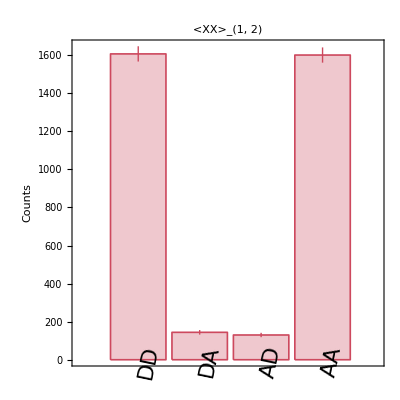

```mathematica
BarChart[Flatten[Accumulate[countsYYXZYYpostSelectAll]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<XX>_(1, 2)"]
```

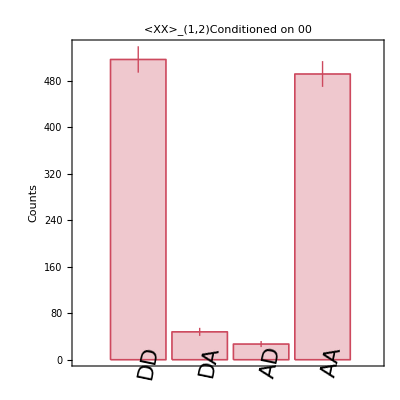

```mathematica
BarChart[Flatten[Accumulate[countsYYXZYYpostSelect00]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<XX>_(1,2)Conditioned on 00"]
```

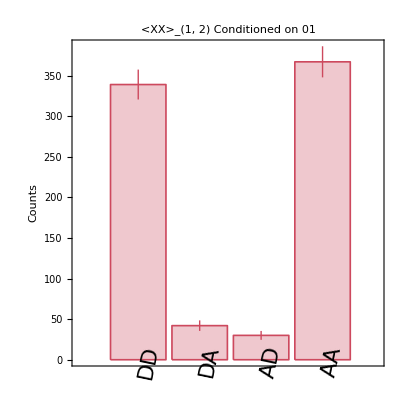

```mathematica
BarChart[Flatten[Accumulate[countsYYXZYYpostSelect01]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<XX>_(1, 2) Conditioned on 01"]
```

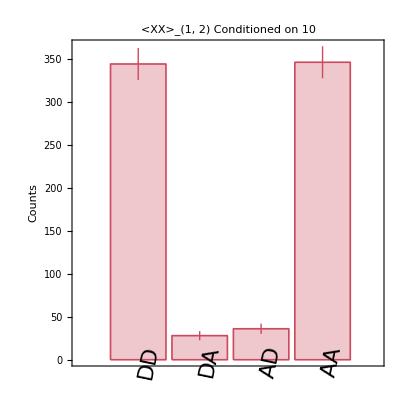

```mathematica
BarChart[Flatten[Accumulate[countsYYXZYYpostSelect10]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<XX>_(1, 2) Conditioned on 10"]
```

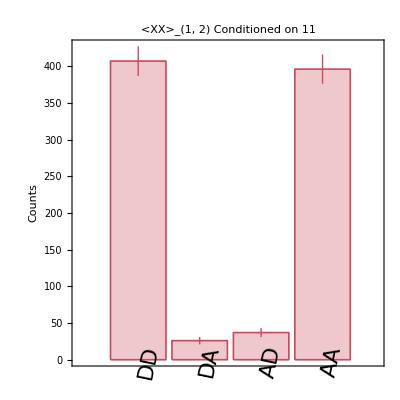

```mathematica
BarChart[Flatten[Accumulate[countsYYXZYYpostSelect11]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<XX>_(1, 2) Conditioned on 11"]
```

### AKR Bell_(1,2)

#### Correct normalisation of data

```mathematica
accumulatedDataXXXZXX=Accumulate@countsXXXZXXpostSelectAllvalue;
accumulatedDataXXXZXXerror=Accumulate@countsXXXZXXpostSelectAll;
```

```mathematica
accumulatedDataYYXZYY=Accumulate@countsYYXZYYpostSelectAllvalue;
accumulatedDataYYXZYYerror=Accumulate@countsYYXZYYpostSelectAll;
```

```mathematica
accumulatedDataXXXZXXnorm=N@accumulatedDataXXXZXX⟦#⟧/Total[accumulatedDataXXXZXX⟦#⟧]&/@Range@Length@accumulatedDataXXXZXX;
accumulatedDataXXXZXXnormError=N@accumulatedDataXXXZXXerror⟦#⟧/Total[accumulatedDataXXXZXXerror⟦#⟧]&/@Range@Length@accumulatedDataXXXZXXerror;

accumulatedDataYYXZYYnorm=N@accumulatedDataYYXZYY⟦#⟧/Total[accumulatedDataYYXZYY⟦#⟧]&/@Range@Length@accumulatedDataYYXZYY;
accumulatedDataYYXZYYnormError=N@accumulatedDataYYXZYYerror⟦#⟧/Total[accumulatedDataYYXZYYerror⟦#⟧]&/@Range@Length@accumulatedDataYYXZYYerror;
```

#### Q_Z

Disparity in first and second index

```mathematica
QAB1=N@Total[Table[#⟦i⟧,{i,{2,3}}]]&/@accumulatedDataXXXZXXnorm;
QAB1Error=N@Total[Table[#⟦i⟧,{i,{2,3}}]]&/@accumulatedDataXXXZXXnormError;
```

```mathematica
(* again, we select the last element of this array as its the Qz of the full data set *)
QAB1⟦-1⟧
```

0.0755697

```mathematica
QzBell12=QAB1;
```

#### Q_X

```mathematica
Qxpositive=N@Total[Table[#⟦i⟧,{i,{1,4}}]]&/@accumulatedDataYYXZYYnorm;
QxpositiveError=N@Total[Table[#⟦i⟧,{i,{1,4}}]]&/@accumulatedDataYYXZYYnormError;
```

```mathematica
Qxnegative=N@Total[Table[#⟦i⟧,{i,{2,3}}]]&/@accumulatedDataYYXZYYnorm;
QxnegativeError=N@Total[Table[#⟦i⟧,{i,{2,3}}]]&/@accumulatedDataYYXZYYnormError;
```

Evaluating Qx is done by computing by evaluating (1 - (QxPositive - QxNegative)/ (QxPositive + QxNegative)) / 2

```mathematica
QxBell12=((1-(Qxpositive⟦#⟧-Qxnegative⟦#⟧)/(Qxnegative⟦#⟧+Qxpositive⟦#⟧))/2)&/@Range[Length@Qxpositive];
QxBell12Error=((1-(QxpositiveError-QxnegativeError)/(QxnegativeError+QxpositiveError))/2);
```

#### AKR

```mathematica
{QxBell12,QzBell12};
```

```mathematica
entropy[x_]:=(-x*Log[2,x])-((1-x)*Log[2,1-x])
```

```mathematica
akrBell12=Table[1-entropy[QxBell12⟦i⟧]-entropy[QzBell12⟦i⟧],{i,Range[Length@QxBell12]}];
```

```mathematica
(* RESULT *)
```

```mathematica
akrBell12⟦-1⟧
```

0.216079

Adding Monte Carlo simultation here based on sampling between the ranges defined by the poissonian uncertainty.

QBER

```mathematica
upperBound=QAB1Error⟦1,1⟧+QAB1Error⟦1,2⟧;
lowerBound=QAB1Error⟦1,1⟧-QAB1Error⟦1,2⟧;
```

```mathematica
errorArrayQBER=Range[lowerBound,upperBound,(upperBound-lowerBound)/1999];
errorArrayQBERsample=Table[RandomSample[errorArrayQBER,1],{i,1,2000}];
```

Qx

```mathematica
upperBound=QxBell12Error⟦1,1⟧+QxBell12Error⟦1,2⟧;
lowerBound=QxBell12Error⟦1,1⟧-QxBell12Error⟦1,2⟧;
```

```mathematica
errorArrayQx=Range[lowerBound,upperBound,(upperBound-lowerBound)/1999];
```

```mathematica
errorArrayQxsample=Table[RandomSample[errorArrayQx,1],{i,1,2000}];
```

AKR

```mathematica
akrArray=1-entropy[errorArrayQxsample⟦#⟧]-entropy[errorArrayQBERsample⟦#⟧]&/@Range[2000];
```

```mathematica
akrStandardDeviation=StandardDeviation[Flatten@akrArray]
akrValue=Mean[Flatten@akrArray]
```

0.0290081

0.217579

#### Summary

```mathematica
(* RESULT BELL 1,2 *)
```

```mathematica
{{"QBER","+-","Qx","+-","AKR","+-"},{QAB1Error⟦1,1⟧,QAB1Error⟦1,2⟧,QxBell12Error⟦1,1⟧,QxBell12Error⟦1,2⟧,akrBell12⟦-1⟧,akrStandardDeviation}}//TableForm
```

QBER | +- | Qx | +- | AKR | +-
0.0755697 | 0.00475614 | 0.0786904 | 0.0132387 | 0.216079 | 0.0290081

### Bell ZZ_(5,6) XXXZXX

#### ZZ_(5,6) data, flip conditioned on 00 and 10

Obtaining the index for the conditional formatting. Recall that we require a flip on qubits 2 and 6 whenever we measure 01 and 11 in qubits 3 and 4.

```mathematica
ZZ0000Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect00001234;
ZZ0001Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect00011234;
ZZ0010Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect00101234;
ZZ0011Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect00111234;
```

```mathematica
ZZ0100Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect01001234;
ZZ0101Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect01011234;
ZZ0110Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect01101234;
ZZ0111Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect01111234;
```

```mathematica
ZZ1000Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect10001234;
ZZ1001Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect10011234;
ZZ1010Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect10101234;
ZZ1011Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect10111234;
```

```mathematica
ZZ1100Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect11001234;
ZZ1101Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect11011234;
ZZ1110Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect11101234;
ZZ1111Bell56=settingsXXXZXX⟦#⟧&/@Flatten@postSelect11111234;
```

Function for performing flips

```mathematica
FlipQubit26[meas_]:=
Join[
meas⟦;;,{1}⟧⟦#⟧,
StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@meas⟦;;,{2}⟧⟦#⟧,
meas⟦;;,{3,4,5}⟧⟦#⟧,
StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@meas⟦;;,{6}⟧⟦#⟧
]&/@Range[Length@meas]
```

Using function defined above to perform flips

```mathematica
ZZ0000Bell56flip=FlipQubit26[ZZ0000Bell56]
ZZ0100Bell56flip=FlipQubit26[ZZ0100Bell56]
ZZ1000Bell56flip=FlipQubit26[ZZ1000Bell56]
ZZ1100Bell56flip=FlipQubit26[ZZ1100Bell56]
```

{{d,a,d,h,d,a},{d,a,d,h,d,d},{d,a,d,h,a,a},{d,a,d,h,a,d}}

{{d,d,d,h,d,a},{d,d,d,h,d,d},{d,d,d,h,a,a},{d,d,d,h,a,d}}

{{a,a,d,h,d,a},{a,a,d,h,d,d},{a,a,d,h,a,a},{a,a,d,h,a,d}}

{{a,d,d,h,d,a},{a,d,d,h,d,d},{a,d,d,h,a,a},{a,d,d,h,a,d}}

```mathematica
ZZ0010Bell56flip=FlipQubit26@ZZ0010Bell56
ZZ0110Bell56flip=FlipQubit26@ZZ0110Bell56
ZZ1010Bell56flip=FlipQubit26@ZZ1010Bell56
ZZ1110Bell56flip=FlipQubit26@ZZ1110Bell56
```

{{d,a,a,h,d,a},{d,a,a,h,d,d},{d,a,a,h,a,a},{d,a,a,h,a,d}}

{{d,d,a,h,d,a},{d,d,a,h,d,d},{d,d,a,h,a,a},{d,d,a,h,a,d}}

{{a,a,a,h,d,a},{a,a,a,h,d,d},{a,a,a,h,a,a},{a,a,a,h,a,d}}

{{a,d,a,h,d,a},{a,d,a,h,d,d},{a,d,a,h,a,a},{a,d,a,h,a,d}}

```mathematica
ZZ0000Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0000Bell56flip,2]
ZZ0001Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0001Bell56,2]
ZZ0010Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0010Bell56flip,2]
ZZ0011Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0011Bell56,2]

ZZ0100Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0100Bell56flip,2]
ZZ0101Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0101Bell56,2]
ZZ0110Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0110Bell56flip,2]
ZZ0111Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ0111Bell56,2]

ZZ1000Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1000Bell56flip,2]
ZZ1001Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1001Bell56,2]
ZZ1010Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1010Bell56flip,2]
ZZ1011Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1011Bell56,2]

ZZ1100Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1100Bell56flip,2]
ZZ1101Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1101Bell56,2]
ZZ1110Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1110Bell56flip,2]
ZZ1111Bell56position=Flatten[Position[settingsXXXZXX,#]&/@ZZ1111Bell56,2]
```

{18,17,20,19}

{5,6,7,8}

{26,25,28,27}

{13,14,15,16}

{2,1,4,3}

{21,22,23,24}

{10,9,12,11}

{29,30,31,32}

{50,49,52,51}

{37,38,39,40}

{58,57,60,59}

{45,46,47,48}

{34,33,36,35}

{53,54,55,56}

{42,41,44,43}

{61,62,63,64}

#### Counts

```mathematica
Dimensions[countsXXXZXXpoissonian]
```

{1,64}

00_(3,4)

```mathematica
countsXXXZXXpostSelect0000=Table[#⟦i⟧,{i,ZZ0000Bell56position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect0000value=Table[#⟦i⟧,{i,ZZ0000Bell56position}]&/@countsXXXZXX;

countsXXXZXXpostSelect0100=Table[#⟦i⟧,{i,ZZ0100Bell56position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect0100value=Table[#⟦i⟧,{i,ZZ0100Bell56position}]&/@countsXXXZXX;

countsXXXZXXpostSelect1000=Table[#⟦i⟧,{i,ZZ1000Bell56position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect1000value=Table[#⟦i⟧,{i,ZZ1000Bell56position}]&/@countsXXXZXX;

countsXXXZXXpostSelect1100=Table[#⟦i⟧,{i,ZZ1100Bell56position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect1100value=Table[#⟦i⟧,{i,ZZ1100Bell56position}]&/@countsXXXZXX;
```

01_(3,4)

```mathematica
countsXXXZXXpostSelect0001=Table[#⟦i⟧,{i,ZZ0001Bell56position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect0001value=Table[#⟦i⟧,{i,ZZ0001Bell56position}]&/@countsXXXZXX;

countsXXXZXXpostSelect0101=Table[#⟦i⟧,{i,ZZ0101Bell56position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect0101value=Table[#⟦i⟧,{i,ZZ0101Bell56position}]&/@countsXXXZXX;

countsXXXZXXpostSelect1001=Table[#⟦i⟧,{i,ZZ1001Bell56position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect1001value=Table[#⟦i⟧,{i,ZZ1001Bell56position}]&/@countsXXXZXX;

countsXXXZXXpostSelect1101=Table[#⟦i⟧,{i,ZZ1101Bell56position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect1101value=Table[#⟦i⟧,{i,ZZ1101Bell56position}]&/@countsXXXZXX;
```

10_(3,4)

```mathematica
countsXXXZXXpostSelect0010=Table[#⟦i⟧,{i,ZZ0010Bell56position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect0010value=Table[#⟦i⟧,{i,ZZ0010Bell56position}]&/@countsXXXZXX;

countsXXXZXXpostSelect0110=Table[#⟦i⟧,{i,ZZ0110Bell56position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect0110value=Table[#⟦i⟧,{i,ZZ0110Bell56position}]&/@countsXXXZXX;

countsXXXZXXpostSelect1010=Table[#⟦i⟧,{i,ZZ1010Bell56position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect1010value=Table[#⟦i⟧,{i,ZZ1010Bell56position}]&/@countsXXXZXX;

countsXXXZXXpostSelect1110=Table[#⟦i⟧,{i,ZZ1110Bell56position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect1110value=Table[#⟦i⟧,{i,ZZ1110Bell56position}]&/@countsXXXZXX;
```

11_(3,4)

```mathematica
countsXXXZXXpostSelect0011=Table[#⟦i⟧,{i,ZZ0011Bell56position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect0011value=Table[#⟦i⟧,{i,ZZ0011Bell56position}]&/@countsXXXZXX;

countsXXXZXXpostSelect0111=Table[#⟦i⟧,{i,ZZ0111Bell56position}]&/@countsXXXZXXpoissonian;countsXXXZXXpostSelect0111value=Table[#⟦i⟧,{i,ZZ0111Bell56position}]&/@countsXXXZXX;

countsXXXZXXpostSelect1011=Table[#⟦i⟧,{i,ZZ1011Bell56position}]&/@countsXXXZXXpoissonian;
countsXXXZXXpostSelect1011value=Table[#⟦i⟧,{i,ZZ1011Bell56position}]&/@countsXXXZXX;

countsXXXZXXpostSelect1111=Table[#⟦i⟧,{i,ZZ1111Bell56position}]&/@countsXXXZXXpoissonian;countsXXXZXXpostSelect1111value=Table[#⟦i⟧,{i,ZZ1111Bell56position}]&/@countsXXXZXX;
```

This is currently not a correct way to sum the counts.

```mathematica
countsXXXZXXpostSelectAll=countsXXXZXXpostSelect0000+countsXXXZXXpostSelect0001+countsXXXZXXpostSelect0010+countsXXXZXXpostSelect0011+countsXXXZXXpostSelect0100+countsXXXZXXpostSelect0101+countsXXXZXXpostSelect0110+countsXXXZXXpostSelect0111+countsXXXZXXpostSelect1000+countsXXXZXXpostSelect1001+countsXXXZXXpostSelect1010+countsXXXZXXpostSelect1011+countsXXXZXXpostSelect1100+countsXXXZXXpostSelect1101+countsXXXZXXpostSelect1110+countsXXXZXXpostSelect1111
```

{{1793.42.,160.13.,96.10.,1418.38.}}

```mathematica
countsXXXZXXpostSelect00=countsXXXZXXpostSelect0000+countsXXXZXXpostSelect0100+countsXXXZXXpostSelect1000+countsXXXZXXpostSelect1100
countsXXXZXXpostSelect01=countsXXXZXXpostSelect0001+countsXXXZXXpostSelect0101+countsXXXZXXpostSelect1001+countsXXXZXXpostSelect1101
countsXXXZXXpostSelect10=countsXXXZXXpostSelect0010+countsXXXZXXpostSelect0110+countsXXXZXXpostSelect1010+countsXXXZXXpostSelect1110
countsXXXZXXpostSelect11=countsXXXZXXpostSelect0011+countsXXXZXXpostSelect0111+countsXXXZXXpostSelect1011+countsXXXZXXpostSelect1111
```

{{607.25.,36.6.,38.6.,470.22.}}

{{377.19.,39.6.,15.4.,331.18.}}

{{403.20.,42.6.,26.5.,263.16.}}

{{406.20.,43.7.,17.4.,354.19.}}

```mathematica
countsXXXZXXpostSelectAllvalue=countsXXXZXXpostSelect0000value+countsXXXZXXpostSelect0001value+countsXXXZXXpostSelect0010value+countsXXXZXXpostSelect0011value+countsXXXZXXpostSelect0100value+countsXXXZXXpostSelect0101value+countsXXXZXXpostSelect0110value+countsXXXZXXpostSelect0111value+countsXXXZXXpostSelect1000value+countsXXXZXXpostSelect1001value+countsXXXZXXpostSelect1010value+countsXXXZXXpostSelect1011value+countsXXXZXXpostSelect1100value+countsXXXZXXpostSelect1101value+countsXXXZXXpostSelect1110value+countsXXXZXXpostSelect1111value
```

{{1.,0.,0.,1.},{1.,0.,0.,2.},{2.,0.,0.,5.},{0.,0.,0.,1.},{1.,0.,0.,3.},{1.,1.,1.,0.},{3.,0.,0.,5.},{2.,0.,1.,1.},{1.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,2.},{5.,0.,0.,1.},{4.,0.,0.,4.},{1.,0.,0.,0.},{2.,1.,0.,1.},{0.,0.,0.,4.},{2.,0.,0.,4.},{0.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,1.,2.},{5.,0.,1.,2.},{2.,1.,0.,1.},{3.,3.,1.,4.},{5.,1.,0.,6.},{2.,0.,0.,3.},{4.,0.,0.,2.},{2.,0.,0.,2.},{0.,0.,0.,1.},{4.,0.,0.,0.},{3.,1.,0.,1.},{3.,0.,1.,2.},{2.,1.,0.,4.},{3.,0.,0.,2.},{3.,0.,0.,0.},{2.,0.,0.,3.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,1.,2.},{3.,0.,0.,2.},{1.,0.,0.,2.},{2.,1.,1.,1.},{2.,0.,0.,3.},{3.,0.,0.,2.},{1.,0.,1.,4.},{1.,0.,1.,4.},{1.,0.,0.,1.},{3.,1.,0.,7.},{3.,0.,0.,2.},{2.,2.,0.,6.},{3.,0.,0.,3.},{0.,0.,0.,3.},{5.,0.,0.,1.},{4.,0.,0.,3.},{4.,0.,0.,3.},{2.,0.,0.,7.},{4.,0.,0.,2.},{1.,1.,0.,4.},{5.,0.,0.,0.},{0.,0.,0.,2.},{3.,0.,1.,1.},{3.,0.,0.,4.},{1.,0.,0.,1.},{4.,0.,0.,1.},{0.,0.,0.,2.},{3.,1.,0.,5.},{1.,0.,0.,4.},{4.,0.,0.,1.},{3.,0.,0.,4.},{1.,0.,0.,4.},{1.,0.,0.,1.},{3.,0.,0.,1.},{4.,0.,0.,2.},{1.,1.,0.,0.},{1.,0.,0.,3.},{1.,0.,0.,3.},{2.,0.,1.,4.},{5.,1.,0.,6.},{4.,0.,0.,1.},{5.,0.,0.,1.},{2.,0.,0.,0.},{6.,0.,0.,5.},{4.,1.,0.,1.},{3.,0.,0.,0.},{5.,0.,0.,2.},{2.,0.,0.,2.},{4.,0.,0.,3.},{1.,0.,0.,1.},{1.,2.,0.,4.},{2.,0.,0.,2.},{4.,0.,1.,1.},{1.,0.,0.,1.},{4.,0.,0.,0.},{3.,0.,1.,1.},{3.,0.,0.,1.},{4.,0.,0.,6.},{0.,0.,1.,2.},{1.,0.,0.,1.},{3.,0.,0.,1.},{1.,0.,0.,3.},{2.,0.,0.,1.},{1.,0.,0.,3.},{0.,0.,0.,4.},{2.,0.,0.,1.},{5.,0.,0.,1.},{3.,0.,0.,3.},{2.,0.,0.,4.},{1.,0.,0.,0.},{0.,0.,1.,3.},{4.,0.,0.,0.},{3.,0.,0.,2.},{3.,0.,0.,5.},{6.,0.,0.,1.},{6.,0.,1.,2.},{2.,1.,0.,4.},{1.,1.,0.,2.},{2.,0.,1.,3.},{1.,0.,0.,1.},{2.,0.,0.,1.},{5.,0.,0.,2.},{1.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,3.},{4.,0.,1.,1.},{3.,0.,1.,3.},{0.,1.,0.,2.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,3.},{0.,0.,0.,1.},{1.,0.,0.,0.},{5.,0.,0.,5.},{4.,2.,0.,5.},{4.,1.,0.,3.},{1.,1.,1.,3.},{5.,0.,0.,4.},{4.,0.,0.,2.},{4.,0.,0.,1.},{1.,0.,0.,3.},{2.,0.,0.,2.},{0.,0.,0.,2.},{2.,0.,0.,5.},{0.,1.,0.,1.},{1.,0.,0.,1.},{9.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,2.},{3.,0.,0.,4.},{0.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,1.},{4.,0.,0.,1.},{4.,0.,1.,0.},{1.,0.,1.,2.},{5.,0.,1.,0.},{1.,0.,1.,5.},{4.,2.,0.,2.},{3.,0.,1.,0.},{1.,0.,0.,2.},{0.,0.,0.,3.},{2.,0.,0.,1.},{3.,0.,0.,1.},{3.,0.,0.,2.},{4.,0.,0.,2.},{0.,0.,0.,1.},{11.,0.,0.,4.},{7.,0.,0.,2.},{3.,0.,1.,3.},{1.,0.,0.,1.},{0.,0.,1.,2.},{4.,0.,0.,0.},{3.,0.,0.,2.},{0.,1.,0.,1.},{1.,0.,0.,0.},{3.,1.,0.,4.},{3.,0.,0.,3.},{5.,0.,0.,1.},{5.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{2.,1.,0.,1.},{4.,1.,0.,2.},{4.,1.,0.,1.},{0.,1.,0.,0.},{3.,1.,1.,2.},{4.,1.,0.,0.},{2.,0.,0.,0.},{5.,0.,0.,2.},{2.,0.,0.,1.},{2.,0.,0.,0.},{6.,1.,0.,5.},{3.,1.,1.,2.},{0.,0.,0.,0.},{3.,0.,0.,3.},{4.,0.,1.,2.},{2.,1.,0.,7.},{2.,0.,0.,2.},{2.,0.,0.,2.},{3.,0.,0.,2.},{1.,0.,0.,3.},{3.,0.,0.,2.},{4.,0.,0.,1.},{3.,0.,0.,4.},{3.,0.,0.,1.},{4.,0.,0.,1.},{1.,0.,0.,2.},{3.,1.,0.,4.},{1.,2.,0.,1.},{4.,1.,1.,3.},{3.,0.,0.,2.},{2.,0.,1.,0.},{4.,1.,0.,0.},{2.,0.,0.,1.},{5.,1.,0.,1.},{3.,0.,0.,0.},{5.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,3.},{3.,1.,0.,4.},{4.,0.,0.,3.},{2.,0.,0.,2.},{3.,0.,0.,1.},{3.,0.,0.,1.},{6.,0.,0.,1.},{2.,0.,0.,2.},{2.,0.,1.,1.},{2.,0.,0.,6.},{3.,0.,0.,2.},{0.,0.,0.,2.},{4.,0.,0.,3.},{4.,0.,0.,3.},{4.,0.,0.,3.},{1.,1.,0.,1.},{4.,0.,0.,2.},{3.,0.,0.,4.},{4.,0.,0.,3.},{3.,0.,0.,1.},{1.,0.,0.,3.},{2.,0.,0.,2.},{2.,0.,0.,6.},{2.,0.,0.,1.},{1.,0.,0.,2.},{2.,0.,0.,2.},{5.,1.,0.,2.},{4.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,5.},{2.,0.,0.,3.},{1.,1.,0.,1.},{2.,0.,0.,1.},{4.,0.,0.,1.},{1.,0.,0.,2.},{4.,0.,0.,3.},{2.,1.,0.,1.},{3.,0.,1.,1.},{2.,0.,0.,2.},{3.,0.,0.,3.},{3.,0.,1.,1.},{1.,0.,0.,3.},{1.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,1.,0.,0.},{4.,0.,0.,0.},{2.,0.,0.,2.},{2.,0.,0.,1.},{3.,0.,1.,2.},{1.,0.,1.,3.},{0.,0.,0.,3.},{3.,0.,0.,1.},{2.,0.,0.,1.},{7.,0.,0.,2.},{3.,0.,0.,3.},{3.,0.,0.,1.},{1.,1.,0.,1.},{1.,0.,0.,4.},{0.,0.,1.,3.},{0.,0.,0.,5.},{0.,1.,0.,1.},{3.,0.,0.,1.},{2.,0.,0.,5.},{3.,0.,0.,2.},{3.,1.,0.,2.},{3.,0.,0.,3.},{0.,1.,0.,1.},{2.,0.,0.,2.},{3.,0.,1.,0.},{2.,0.,0.,3.},{2.,1.,0.,2.},{3.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,1.},{4.,0.,0.,2.},{5.,0.,2.,2.},{2.,0.,0.,2.},{1.,0.,1.,3.},{4.,0.,0.,2.},{5.,0.,0.,1.},{3.,1.,1.,2.},{1.,0.,1.,2.},{3.,0.,0.,1.},{5.,0.,0.,0.},{5.,0.,0.,3.},{3.,0.,0.,1.},{1.,0.,0.,6.},{3.,0.,0.,1.},{2.,0.,0.,2.},{4.,0.,0.,2.},{5.,0.,0.,0.},{2.,0.,1.,5.},{4.,0.,0.,2.},{3.,0.,0.,3.},{2.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,3.},{3.,0.,0.,2.},{2.,0.,0.,3.},{2.,0.,0.,4.},{0.,1.,0.,3.},{1.,1.,0.,1.},{4.,0.,0.,1.},{1.,1.,0.,3.},{2.,0.,0.,1.},{4.,0.,0.,2.},{2.,0.,0.,2.},{0.,0.,2.,4.},{3.,0.,0.,0.},{1.,0.,0.,2.},{3.,0.,0.,3.},{1.,0.,0.,0.},{3.,0.,0.,1.},{3.,0.,1.,0.},{3.,0.,0.,2.},{3.,0.,0.,1.},{3.,1.,0.,2.},{1.,0.,0.,1.},{2.,0.,0.,2.},{2.,0.,0.,2.},{2.,1.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,2.},{4.,1.,0.,0.},{1.,1.,0.,0.},{3.,0.,0.,4.},{1.,0.,0.,4.},{2.,0.,0.,1.},{3.,1.,1.,3.},{3.,1.,0.,1.},{5.,0.,0.,1.},{5.,1.,1.,3.},{3.,0.,0.,2.},{1.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,4.},{5.,0.,0.,5.},{3.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,2.},{3.,0.,0.,1.},{6.,0.,0.,0.},{4.,0.,0.,1.},{4.,0.,0.,3.},{2.,0.,0.,2.},{1.,0.,0.,2.},{6.,0.,0.,0.},{1.,0.,0.,1.},{5.,0.,0.,2.},{4.,0.,0.,2.},{4.,0.,1.,1.},{3.,0.,0.,3.},{2.,0.,0.,1.},{4.,1.,1.,1.},{4.,0.,0.,1.},{4.,0.,0.,3.},{1.,0.,0.,3.},{1.,0.,0.,1.},{1.,0.,0.,3.},{1.,1.,0.,2.},{2.,0.,0.,2.},{3.,0.,0.,1.},{4.,0.,0.,2.},{3.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,1.},{3.,0.,0.,1.},{1.,0.,1.,4.},{0.,0.,0.,1.},{2.,0.,1.,2.},{0.,0.,0.,1.},{2.,1.,0.,0.},{2.,0.,0.,3.},{1.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{3.,0.,0.,1.},{1.,1.,0.,2.},{1.,0.,0.,3.},{0.,0.,0.,0.},{3.,0.,0.,2.},{4.,0.,0.,2.},{2.,0.,0.,3.},{1.,1.,0.,1.},{2.,1.,0.,1.},{1.,0.,1.,1.},{3.,0.,0.,0.},{3.,0.,0.,3.},{1.,1.,0.,3.},{2.,0.,0.,3.},{0.,0.,0.,3.},{2.,0.,0.,1.},{2.,0.,1.,3.},{4.,0.,0.,2.},{4.,0.,1.,2.},{0.,1.,0.,2.},{2.,0.,0.,1.},{3.,2.,0.,1.},{3.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,1.,1.},{1.,0.,0.,3.},{2.,0.,0.,3.},{1.,0.,0.,1.},{2.,1.,0.,2.},{3.,0.,0.,5.},{1.,0.,0.,2.},{1.,0.,1.,2.},{1.,0.,0.,3.},{2.,0.,1.,2.},{3.,0.,0.,4.},{5.,0.,1.,1.},{2.,0.,0.,3.},{2.,0.,0.,6.},{4.,0.,0.,1.},{2.,0.,0.,5.},{0.,0.,0.,2.},{5.,1.,0.,0.},{1.,0.,0.,3.},{4.,0.,0.,1.},{4.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,2.},{2.,0.,0.,0.},{4.,0.,0.,3.},{4.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,2.},{2.,0.,0.,3.},{1.,0.,0.,4.},{1.,0.,0.,4.},{1.,0.,0.,4.},{3.,0.,0.,2.},{1.,0.,0.,2.},{1.,1.,0.,0.},{4.,1.,0.,2.},{3.,0.,0.,2.},{2.,0.,0.,2.},{0.,1.,0.,1.},{1.,0.,0.,0.},{3.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{3.,0.,0.,2.},{2.,0.,0.,2.},{4.,0.,1.,2.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,3.},{2.,2.,1.,1.},{4.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,1.},{3.,0.,0.,0.},{3.,1.,0.,0.},{2.,0.,1.,0.},{0.,1.,0.,2.},{4.,0.,0.,3.},{3.,0.,0.,1.},{2.,0.,0.,1.},{5.,0.,0.,1.},{1.,0.,1.,3.},{1.,1.,0.,2.},{5.,0.,1.,2.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,2.},{2.,0.,0.,2.},{2.,0.,0.,2.},{3.,0.,0.,2.},{2.,0.,1.,3.},{9.,1.,0.,2.},{5.,1.,0.,2.},{2.,0.,0.,2.},{6.,0.,0.,2.},{1.,0.,0.,1.},{3.,0.,1.,4.},{2.,1.,0.,0.},{4.,1.,0.,2.},{5.,0.,0.,2.},{3.,0.,1.,2.},{2.,0.,0.,2.},{4.,0.,0.,2.},{0.,0.,0.,4.},{2.,0.,0.,1.},{2.,1.,0.,1.},{2.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,0.},{4.,0.,0.,0.},{4.,1.,0.,1.},{2.,0.,1.,2.},{4.,0.,0.,2.},{2.,0.,0.,2.},{6.,0.,0.,6.},{2.,1.,0.,2.},{0.,0.,0.,5.},{3.,0.,0.,2.},{2.,0.,0.,2.},{3.,1.,0.,2.},{2.,0.,0.,0.},{3.,0.,0.,3.},{1.,0.,0.,1.},{3.,0.,0.,3.},{1.,0.,1.,2.},{0.,1.,1.,4.},{2.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,2.},{1.,0.,0.,1.},{4.,0.,0.,5.},{0.,0.,0.,0.},{3.,1.,0.,2.},{1.,0.,0.,2.},{1.,1.,0.,0.},{3.,0.,0.,2.},{1.,1.,0.,3.},{4.,0.,0.,1.},{1.,0.,0.,4.},{1.,0.,0.,3.},{2.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,4.},{3.,0.,0.,1.},{5.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,3.},{2.,0.,0.,1.},{2.,1.,0.,2.},{1.,0.,0.,2.},{2.,0.,0.,0.},{4.,0.,0.,4.},{1.,0.,0.,0.},{0.,2.,0.,0.},{1.,0.,0.,2.},{3.,0.,0.,2.},{3.,0.,0.,1.},{2.,2.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,2.,0.,3.},{5.,0.,0.,1.},{0.,0.,0.,4.},{0.,0.,0.,2.},{2.,0.,0.,1.},{1.,0.,1.,2.},{5.,0.,0.,2.},{3.,0.,1.,2.},{1.,2.,0.,3.},{6.,0.,0.,2.},{1.,1.,0.,3.},{4.,0.,0.,1.},{2.,0.,0.,2.},{2.,0.,0.,3.},{3.,0.,0.,0.},{0.,1.,0.,4.},{3.,1.,0.,3.},{1.,0.,0.,1.},{2.,1.,0.,1.},{1.,0.,0.,2.},{2.,0.,0.,2.},{0.,0.,0.,0.},{3.,0.,0.,1.},{2.,1.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,1.,0.,1.},{3.,0.,0.,2.},{3.,0.,0.,1.},{2.,0.,1.,5.},{4.,0.,0.,2.},{1.,0.,0.,2.},{1.,0.,0.,2.},{0.,0.,1.,4.},{0.,1.,0.,4.},{1.,0.,0.,1.},{2.,0.,0.,3.},{6.,0.,0.,2.},{1.,0.,0.,1.},{3.,0.,0.,0.},{0.,1.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,1.},{2.,1.,0.,3.},{1.,0.,0.,0.},{2.,0.,0.,2.},{2.,0.,0.,5.},{1.,0.,0.,1.},{2.,1.,1.,1.},{4.,0.,0.,3.},{3.,0.,0.,2.},{2.,0.,0.,1.},{2.,0.,1.,1.},{4.,0.,0.,0.},{0.,0.,0.,3.},{2.,2.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,4.},{0.,0.,0.,1.},{2.,2.,0.,2.},{3.,0.,1.,1.},{3.,0.,0.,0.},{2.,0.,1.,0.},{1.,0.,0.,1.},{3.,0.,0.,3.},{3.,0.,0.,1.},{2.,1.,0.,0.},{2.,0.,0.,4.},{4.,1.,0.,3.},{4.,1.,0.,0.},{2.,0.,0.,2.},{1.,0.,0.,2.},{2.,0.,0.,3.},{3.,0.,0.,2.},{2.,0.,0.,0.},{3.,1.,0.,3.},{0.,1.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{3.,0.,0.,0.},{8.,0.,0.,1.},{1.,0.,1.,1.},{2.,0.,0.,1.},{0.,0.,0.,3.},{1.,0.,0.,1.},{4.,0.,0.,1.},{6.,1.,0.,1.},{3.,1.,0.,1.},{3.,0.,0.,1.},{3.,0.,0.,1.},{2.,1.,0.,1.},{2.,1.,0.,2.},{2.,0.,0.,0.},{3.,1.,0.,1.},{2.,0.,1.,0.},{2.,0.,0.,0.},{2.,0.,0.,3.},{1.,0.,0.,1.},{2.,0.,0.,2.},{4.,0.,0.,1.},{2.,0.,0.,2.},{2.,1.,0.,1.},{0.,1.,0.,2.},{2.,1.,0.,1.},{1.,0.,1.,2.},{1.,0.,1.,2.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,2.},{6.,0.,0.,3.},{3.,0.,0.,1.},{1.,0.,0.,3.},{0.,0.,1.,1.},{1.,0.,0.,0.},{3.,1.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,2.},{2.,0.,0.,0.},{2.,0.,0.,1.},{4.,0.,0.,3.},{2.,0.,0.,0.},{1.,1.,1.,0.},{0.,0.,0.,3.},{1.,0.,0.,0.},{2.,1.,0.,0.},{4.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,1.},{3.,1.,0.,2.},{0.,1.,0.,2.},{3.,0.,0.,1.},{2.,0.,0.,3.},{0.,0.,0.,3.},{2.,0.,0.,2.},{1.,0.,0.,3.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{5.,1.,0.,1.},{3.,1.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{3.,0.,0.,2.},{2.,0.,1.,0.},{3.,0.,0.,2.},{4.,0.,1.,1.},{3.,0.,0.,1.},{1.,1.,0.,0.},{0.,1.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,3.},{4.,1.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,1.},{4.,0.,0.,3.},{0.,0.,0.,1.},{4.,1.,0.,3.},{1.,1.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,0.,1.},{3.,0.,0.,2.},{2.,0.,1.,0.},{1.,0.,0.,5.},{4.,0.,0.,0.},{3.,1.,0.,3.},{4.,0.,1.,2.},{0.,0.,0.,1.},{3.,0.,0.,2.},{4.,0.,0.,3.},{1.,0.,0.,3.},{0.,0.,0.,2.},{2.,1.,0.,1.},{4.,0.,0.,0.},{3.,1.,0.,0.},{2.,0.,0.,0.},{4.,1.,0.,2.},{3.,0.,0.,0.},{2.,0.,0.,2.},{3.,0.,0.,0.},{1.,1.,0.,2.},{1.,0.,1.,2.},{1.,0.,0.,4.},{4.,0.,0.,3.},{1.,0.,0.,2.},{3.,0.,0.,1.},{1.,0.,0.,2.},{4.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,1.},{2.,1.,1.,3.},{4.,1.,0.,3.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,1.},{1.,1.,0.,2.},{3.,0.,0.,0.},{1.,0.,0.,4.},{3.,1.,0.,2.},{4.,0.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,0.},{3.,0.,0.,1.},{2.,0.,0.,5.},{4.,0.,1.,5.},{2.,0.,0.,0.},{3.,0.,0.,1.},{3.,0.,0.,3.},{3.,0.,0.,1.},{2.,0.,1.,0.},{4.,0.,0.,3.},{3.,0.,0.,1.},{3.,0.,0.,0.}}

```mathematica
countsXXXZXXpostSelect00value=countsXXXZXXpostSelect0000value+countsXXXZXXpostSelect0100value+countsXXXZXXpostSelect1000value+countsXXXZXXpostSelect1100value

countsXXXZXXpostSelect01value=countsXXXZXXpostSelect0001value+countsXXXZXXpostSelect0101value+countsXXXZXXpostSelect1001value+countsXXXZXXpostSelect1101value

countsXXXZXXpostSelect10value=countsXXXZXXpostSelect0010value+countsXXXZXXpostSelect0110value+countsXXXZXXpostSelect1010value+countsXXXZXXpostSelect1110value

countsXXXZXXpostSelect11value=countsXXXZXXpostSelect0011value+countsXXXZXXpostSelect0111value+countsXXXZXXpostSelect1011value+countsXXXZXXpostSelect1111value
```

{{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,4.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,1.,0.},{1.,0.,0.,1.},{1.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,1.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,1.,0.,0.},{2.,0.,0.,2.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{4.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,1.,1.},{0.,1.,0.,2.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,1.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,1.},{1.,0.,0.,0.},{1.,1.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,3.},{1.,0.,0.,2.},{3.,0.,0.,2.},{0.,1.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{2.,1.,0.,3.},{0.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,2.},{1.,0.,0.,1.},{2.,1.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,0.},{0.,1.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,1.,1.},{0.,0.,0.,0.},{3.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,3.},{3.,0.,0.,1.},{5.,0.,1.,1.},{1.,0.,0.,3.},{1.,0.,0.,1.},{0.,0.,1.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,2.},{1.,0.,0.,1.},{2.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,1.},{1.,0.,0.,1.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,1.,1.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,1.,1.},{1.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,2.},{1.,0.,0.,2.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,1.,0.},{4.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,3.},{1.,0.,0.,1.},{1.,0.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,1.,0.,3.},{0.,0.,0.,1.},{2.,0.,1.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{4.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,3.},{0.,0.,0.,0.},{2.,0.,0.,2.},{0.,1.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{4.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,1.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,2.},{0.,0.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,2.},{0.,1.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,1.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{3.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,5.},{1.,0.,0.,1.},{1.,0.,0.,1.},{3.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,1.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,1.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{4.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{3.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,1.,0.,0.},{1.,0.,1.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,1.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,1.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,2.},{1.,0.,0.,3.},{0.,0.,1.,1.},{1.,0.,0.,2.},{2.,0.,1.,1.},{1.,0.,0.,2.},{2.,0.,0.,2.},{2.,0.,0.,0.},{1.,0.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,1.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,1.,0.},{5.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{2.,1.,0.,1.},{1.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{5.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,1.},{0.,1.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{2.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{4.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,1.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,3.},{1.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{3.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,3.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,1.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,3.},{2.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,1.,1.},{0.,0.,0.,1.},{2.,0.,0.,3.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.}}

{{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,3.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{2.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,3.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,2.},{2.,2.,0.,2.},{0.,0.,0.,0.},{0.,0.,1.,2.},{1.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,1.},{1.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,3.},{1.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,1.},{1.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,1.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,3.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{3.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,1.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,2.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,3.},{0.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,2.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{5.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,1.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{2.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}

{{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,1.,0.},{0.,1.,0.,0.},{1.,0.,0.,1.},{1.,1.,0.,2.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,2.},{0.,0.,0.,0.},{2.,0.,0.,2.},{1.,0.,0.,0.},{0.,1.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,3.},{0.,1.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{2.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{4.,0.,1.,0.},{0.,0.,0.,1.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,1.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,2.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,1.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,2.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,1.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{4.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,1.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,2.,0.,0.},{3.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{2.,1.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,1.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.}}

{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,1.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{3.,0.,0.,1.},{0.,0.,1.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{2.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,4.},{1.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,3.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,1.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,1.},{1.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,1.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{1.,1.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{2.,1.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{4.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{3.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{3.,0.,1.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,1.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,1.,0.,0.},{2.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,1.,0.,2.},{0.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,1.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,1.,2.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,1.,2.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{3.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,1.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.}}

```mathematica
Total[countsXXXZXXpostSelect00value]
Total[countsXXXZXXpostSelect00]

Total[countsXXXZXXpostSelect01value]
Total[countsXXXZXXpostSelect01]

Total[countsXXXZXXpostSelect10value]
Total[countsXXXZXXpostSelect10]

Total[countsXXXZXXpostSelect11value]
Total[countsXXXZXXpostSelect11]
```

{607.,36.,38.,470.}

{607.25.,36.6.,38.6.,470.22.}

{377.,39.,15.,331.}

{377.19.,39.6.,15.4.,331.18.}

{403.,42.,26.,263.}

{403.20.,42.6.,26.5.,263.16.}

{406.,43.,17.,354.}

{406.20.,43.7.,17.4.,354.19.}

#### Labels for plotting Bell state populations

```mathematica
bellLabels=Tuples[{"H","V"},2];
bellLabels=StringReplace[ToString[#],{","->""," "->"","{"->"","}"->""}]&/@%
```

{HH,HV,VH,VV}

#### ZZ_(5,6)

```mathematica
scale=Total[Accumulate[countsXXXZXXpostSelectAll]⟦-1⟧];
scale=scale["Value"];
phiplus=1/√2(Kron[h,h]+Kron[v,v]);
projections=Kronk/@Tuples[{h,v},2];
theoryPopulationsGHZ=Flatten[(#†.phiplus)&/@projections]*scale/√2;
stackedData={Flatten@theoryPopulationsGHZ,Flatten[Accumulate[countsXXXZXXpostSelectAll]⟦-1⟧]}†;
```

```mathematica
BarChartSettings={ImageSize->400
,LabelStyle->Directive[FontFamily->"Menlo",FontSize->22,Black]
,ChartStyle->Directive[rocketColors⟦2⟧,Opacity[0.3],EdgeForm[{rocketColors⟦2⟧,Thickness[0.003],Opacity[1]}]]
,IntervalMarkers->"Fences"
,AspectRatio->1/2
,Frame->True
,IntervalMarkersStyle->Directive[rocketColors⟦2⟧,Thick]
,FrameLabel->{"",Style["Counts",FontFamily->"Times New Roman"]}
};
```

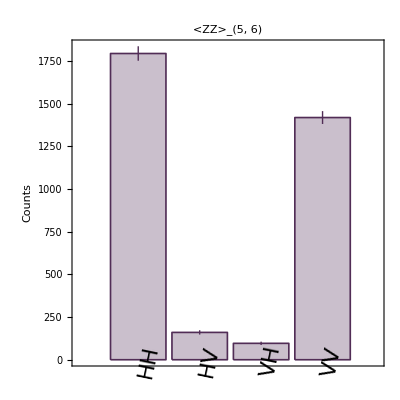

```mathematica
BarChart[Flatten[Accumulate[countsXXXZXXpostSelectAll]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(5, 6)"]
```

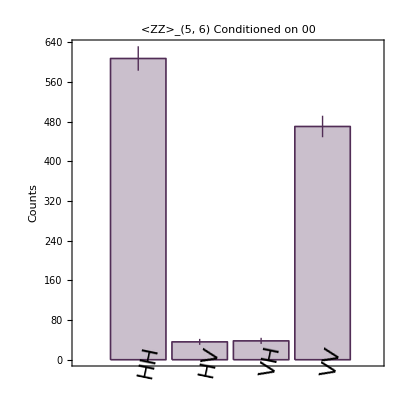

```mathematica
BarChart[Flatten[Accumulate[countsXXXZXXpostSelect00]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(5, 6) Conditioned on 00"]
```

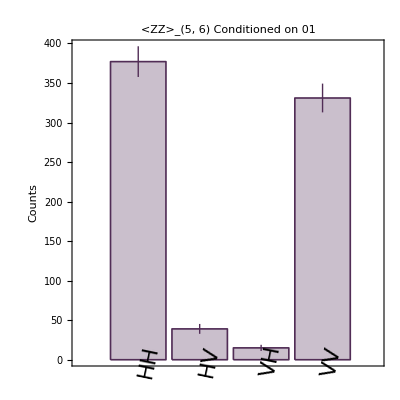

```mathematica
BarChart[Flatten[Accumulate[countsXXXZXXpostSelect01]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(5, 6) Conditioned on 01"]
```

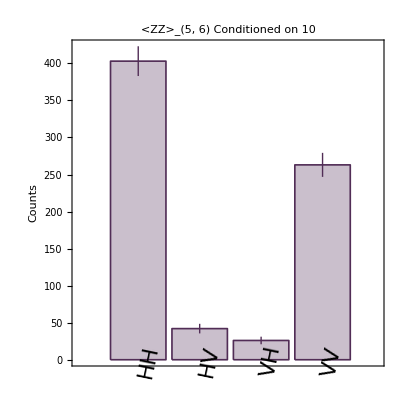

```mathematica
BarChart[Flatten[Accumulate[countsXXXZXXpostSelect10]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(5, 6) Conditioned on 10"]
```

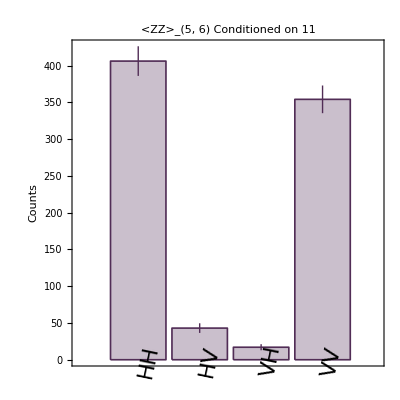

```mathematica
BarChart[Flatten[Accumulate[countsXXXZXXpostSelect11]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(5, 6) Conditioned on 11"]
```

### Bell XX_(5,6) YYXZYY

#### XX_(5,6) data

```mathematica
XX0000Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect00001234;
XX0001Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect00011234;
XX0010Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect00101234;
XX0011Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect00111234;
```

```mathematica
XX0100Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect01001234;
XX0101Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect01011234;
XX0110Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect01101234;
XX0111Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect01111234;
```

```mathematica
XX1000Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect10001234;
XX1001Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect10011234;
XX1010Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect10101234;
XX1011Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect10111234;
```

```mathematica
XX1100Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect11001234;
XX1101Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect11011234;
XX1110Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect11101234;
XX1111Bell56=settingsYYXZYY⟦#⟧&/@Flatten@postSelect11111234;
```

Function for performing flips

```mathematica
FlipQubit26[meas_]:=
Join[
meas⟦;;,{1}⟧⟦#⟧,
StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@meas⟦;;,{2}⟧⟦#⟧,
meas⟦;;,{3,4,5}⟧⟦#⟧,
StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@meas⟦;;,{6}⟧⟦#⟧
]&/@Range[Length@meas]
```

Using function defined above to perform flips

```mathematica
XX0000Bell56flip=FlipQubit26[XX0000Bell56]
XX0100Bell56flip=FlipQubit26[XX0100Bell56]
XX1000Bell56flip=FlipQubit26[XX1000Bell56]
XX1100Bell56flip=FlipQubit26[XX1100Bell56]
```

{{r,l,d,h,r,l},{r,l,d,h,r,r},{r,l,d,h,l,l},{r,l,d,h,l,r}}

{{r,r,d,h,r,l},{r,r,d,h,r,r},{r,r,d,h,l,l},{r,r,d,h,l,r}}

{{l,l,d,h,r,l},{l,l,d,h,r,r},{l,l,d,h,l,l},{l,l,d,h,l,r}}

{{l,r,d,h,r,l},{l,r,d,h,r,r},{l,r,d,h,l,l},{l,r,d,h,l,r}}

```mathematica
XX0001Bell56flip=FlipQubit26[XX0001Bell56]
XX0101Bell56flip=FlipQubit26[XX0101Bell56]
XX1001Bell56flip=FlipQubit26[XX1001Bell56]
XX1101Bell56flip=FlipQubit26[XX1101Bell56]
```

{{r,l,d,v,r,l},{r,l,d,v,r,r},{r,l,d,v,l,l},{r,l,d,v,l,r}}

{{r,r,d,v,r,l},{r,r,d,v,r,r},{r,r,d,v,l,l},{r,r,d,v,l,r}}

{{l,l,d,v,r,l},{l,l,d,v,r,r},{l,l,d,v,l,l},{l,l,d,v,l,r}}

{{l,r,d,v,r,l},{l,r,d,v,r,r},{l,r,d,v,l,l},{l,r,d,v,l,r}}

```mathematica
XX0010Bell56flip=FlipQubit26@XX0010Bell56
XX0110Bell56flip=FlipQubit26@XX0110Bell56
XX1010Bell56flip=FlipQubit26@XX1010Bell56
XX1110Bell56flip=FlipQubit26@XX1110Bell56
```

{{r,l,a,h,r,l},{r,l,a,h,r,r},{r,l,a,h,l,l},{r,l,a,h,l,r}}

{{r,r,a,h,r,l},{r,r,a,h,r,r},{r,r,a,h,l,l},{r,r,a,h,l,r}}

{{l,l,a,h,r,l},{l,l,a,h,r,r},{l,l,a,h,l,l},{l,l,a,h,l,r}}

{{l,r,a,h,r,l},{l,r,a,h,r,r},{l,r,a,h,l,l},{l,r,a,h,l,r}}

```mathematica
XX0011Bell56flip=FlipQubit26@XX0011Bell56
XX0111Bell56flip=FlipQubit26@XX0111Bell56
XX1011Bell56flip=FlipQubit26@XX1011Bell56
XX1111Bell56flip=FlipQubit26@XX1111Bell56
```

{{r,l,a,v,r,l},{r,l,a,v,r,r},{r,l,a,v,l,l},{r,l,a,v,l,r}}

{{r,r,a,v,r,l},{r,r,a,v,r,r},{r,r,a,v,l,l},{r,r,a,v,l,r}}

{{l,l,a,v,r,l},{l,l,a,v,r,r},{l,l,a,v,l,l},{l,l,a,v,l,r}}

{{l,r,a,v,r,l},{l,r,a,v,r,r},{l,r,a,v,l,l},{l,r,a,v,l,r}}

```mathematica
XX0000Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX0000Bell56,2]
XX0001Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX0001Bell56flip,2]
XX0010Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX0010Bell56,2]
XX0011Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX0011Bell56flip,2]

XX0100Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX0100Bell56,2]
XX0101Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX0101Bell56flip,2]
XX0110Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX0110Bell56,2]
XX0111Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX0111Bell56flip,2]

XX1000Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX1000Bell56,2]
XX1001Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX1001Bell56flip,2]
XX1010Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX1010Bell56,2]
XX1011Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX1011Bell56flip,2]

XX1100Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX1100Bell56,2]
XX1101Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX1101Bell56flip,2]
XX1110Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX1110Bell56,2]
XX1111Bell56position=Flatten[Position[settingsYYXZYY,#]&/@XX1111Bell56flip,2]
```

{1,2,3,4}

{22,21,24,23}

{9,10,11,12}

{30,29,32,31}

{17,18,19,20}

{6,5,8,7}

{25,26,27,28}

{14,13,16,15}

{33,34,35,36}

{54,53,56,55}

{41,42,43,44}

{62,61,64,63}

{49,50,51,52}

{38,37,40,39}

{57,58,59,60}

{46,45,48,47}

#### Counts

```mathematica
Dimensions[countsXXXZXXpoissonian]
```

{1,64}

00_(3,4)

```mathematica
countsYYXZYYpostSelect0000=Table[#⟦i⟧,{i,XX0000Bell56position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect0000value=Table[#⟦i⟧,{i,XX0000Bell56position}]&/@countsYYXZYY;

countsYYXZYYpostSelect0100=Table[#⟦i⟧,{i,XX0100Bell56position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect0100value=Table[#⟦i⟧,{i,XX0100Bell56position}]&/@countsYYXZYY;

countsYYXZYYpostSelect1000=Table[#⟦i⟧,{i,XX1000Bell56position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect1000value=Table[#⟦i⟧,{i,XX1000Bell56position}]&/@countsYYXZYY;

countsYYXZYYpostSelect1100=Table[#⟦i⟧,{i,XX1100Bell56position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect1100value=Table[#⟦i⟧,{i,XX1100Bell56position}]&/@countsYYXZYY;
```

01_(3,4)

```mathematica
countsYYXZYYpostSelect0001=Table[#⟦i⟧,{i,XX0001Bell56position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect0001value=Table[#⟦i⟧,{i,XX0001Bell56position}]&/@countsYYXZYY;

countsYYXZYYpostSelect0101=Table[#⟦i⟧,{i,XX0101Bell56position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect0101value=Table[#⟦i⟧,{i,XX0101Bell56position}]&/@countsYYXZYY;

countsYYXZYYpostSelect1001=Table[#⟦i⟧,{i,XX1001Bell56position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect1001value=Table[#⟦i⟧,{i,XX1001Bell56position}]&/@countsYYXZYY;

countsYYXZYYpostSelect1101=Table[#⟦i⟧,{i,XX1101Bell56position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect1101value=Table[#⟦i⟧,{i,XX1101Bell56position}]&/@countsYYXZYY;
```

10_(3,4)

```mathematica
countsYYXZYYpostSelect0010=Table[#⟦i⟧,{i,XX0010Bell56position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect0010value=Table[#⟦i⟧,{i,XX0010Bell56position}]&/@countsYYXZYY;

countsYYXZYYpostSelect0110=Table[#⟦i⟧,{i,XX0110Bell56position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect0110value=Table[#⟦i⟧,{i,XX0110Bell56position}]&/@countsYYXZYY;

countsYYXZYYpostSelect1010=Table[#⟦i⟧,{i,XX1010Bell56position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect1010value=Table[#⟦i⟧,{i,XX1010Bell56position}]&/@countsYYXZYY;

countsYYXZYYpostSelect1110=Table[#⟦i⟧,{i,XX1110Bell56position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect1110value=Table[#⟦i⟧,{i,XX1110Bell56position}]&/@countsYYXZYY;
```

11_(3,4)

```mathematica
countsYYXZYYpostSelect0011=Table[#⟦i⟧,{i,XX0011Bell56position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect0011value=Table[#⟦i⟧,{i,XX0011Bell56position}]&/@countsYYXZYY;

countsYYXZYYpostSelect0111=Table[#⟦i⟧,{i,XX0111Bell56position}]&/@countsYYXZYYpoissonian;countsYYXZYYpostSelect0111value=Table[#⟦i⟧,{i,XX0111Bell56position}]&/@countsYYXZYY;

countsYYXZYYpostSelect1011=Table[#⟦i⟧,{i,XX1011Bell56position}]&/@countsYYXZYYpoissonian;
countsYYXZYYpostSelect1011value=Table[#⟦i⟧,{i,XX1011Bell56position}]&/@countsYYXZYY;

countsYYXZYYpostSelect1111=Table[#⟦i⟧,{i,XX1111Bell56position}]&/@countsYYXZYYpoissonian;countsYYXZYYpostSelect1111value=Table[#⟦i⟧,{i,XX1111Bell56position}]&/@countsYYXZYY;
```

This is currently not a correct way to sum the counts.

```mathematica
countsYYXZYYpostSelectAll=countsYYXZYYpostSelect0000+countsYYXZYYpostSelect0001+countsYYXZYYpostSelect0010+countsYYXZYYpostSelect0011+countsYYXZYYpostSelect0100+countsYYXZYYpostSelect0101+countsYYXZYYpostSelect0110+countsYYXZYYpostSelect0111+countsYYXZYYpostSelect1000+countsYYXZYYpostSelect1001+countsYYXZYYpostSelect1010+countsYYXZYYpostSelect1011+countsYYXZYYpostSelect1100+countsYYXZYYpostSelect1101+countsYYXZYYpostSelect1110+countsYYXZYYpostSelect1111
```

{{1810.43.,175.13.,124.11.,1373.37.}}

```mathematica
countsYYXZYYpostSelect00=countsYYXZYYpostSelect0000+countsYYXZYYpostSelect0100+countsYYXZYYpostSelect1000+countsYYXZYYpostSelect1100

countsYYXZYYpostSelect01=countsYYXZYYpostSelect0001+countsYYXZYYpostSelect0101+countsYYXZYYpostSelect1001+countsYYXZYYpostSelect1101

countsYYXZYYpostSelect10=countsYYXZYYpostSelect0010+countsYYXZYYpostSelect0110+countsYYXZYYpostSelect1010+countsYYXZYYpostSelect1110

countsYYXZYYpostSelect11=countsYYXZYYpostSelect0011+countsYYXZYYpostSelect0111+countsYYXZYYpostSelect1011+countsYYXZYYpostSelect1111
```

{{590.24.,54.7.,35.6.,405.20.}}

{{415.20.,45.7.,20.4.,298.17.}}

{{355.19.,38.6.,40.6.,321.18.}}

{{450.21.,38.6.,29.5.,349.19.}}

```mathematica
countsYYXZYYpostSelectAllvalue=countsYYXZYYpostSelect0000value+countsYYXZYYpostSelect0001value+countsYYXZYYpostSelect0010value+countsYYXZYYpostSelect0011value+countsYYXZYYpostSelect0100value+countsYYXZYYpostSelect0101value+countsYYXZYYpostSelect0110value+countsYYXZYYpostSelect0111value+countsYYXZYYpostSelect1000value+countsYYXZYYpostSelect1001value+countsYYXZYYpostSelect1010value+countsYYXZYYpostSelect1011value+countsYYXZYYpostSelect1100value+countsYYXZYYpostSelect1101value+countsYYXZYYpostSelect1110value+countsYYXZYYpostSelect1111value
```

{{1.,1.,1.,1.},{4.,0.,2.,1.},{4.,0.,0.,0.},{1.,1.,0.,1.},{4.,0.,1.,2.},{2.,0.,0.,3.},{2.,0.,0.,2.},{6.,2.,0.,1.},{2.,0.,0.,3.},{0.,0.,0.,1.},{1.,0.,0.,4.},{5.,0.,0.,1.},{7.,0.,0.,3.},{3.,0.,0.,1.},{2.,0.,0.,1.},{4.,0.,1.,2.},{6.,0.,1.,2.},{0.,0.,1.,1.},{1.,0.,0.,5.},{5.,0.,0.,3.},{4.,0.,0.,2.},{2.,0.,0.,2.},{3.,0.,0.,2.},{3.,1.,1.,0.},{1.,0.,0.,2.},{4.,0.,0.,2.},{1.,0.,0.,0.},{3.,0.,0.,2.},{2.,0.,0.,1.},{3.,1.,0.,1.},{4.,0.,0.,4.},{4.,0.,0.,3.},{3.,1.,0.,4.},{3.,0.,1.,3.},{0.,0.,0.,0.},{1.,0.,0.,2.},{2.,0.,0.,1.},{5.,2.,0.,3.},{3.,1.,1.,0.},{3.,0.,0.,3.},{3.,0.,0.,2.},{3.,0.,0.,0.},{3.,0.,0.,2.},{3.,0.,0.,0.},{1.,0.,1.,3.},{2.,0.,0.,4.},{3.,0.,0.,5.},{3.,0.,0.,5.},{4.,0.,0.,3.},{3.,0.,0.,3.},{2.,0.,0.,4.},{2.,0.,1.,1.},{3.,0.,0.,3.},{4.,0.,1.,0.},{1.,0.,0.,1.},{3.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,2.},{1.,1.,0.,3.},{1.,0.,0.,1.},{1.,0.,0.,5.},{1.,1.,0.,5.},{3.,0.,1.,4.},{2.,0.,0.,3.},{3.,1.,0.,2.},{2.,0.,0.,0.},{0.,2.,0.,5.},{2.,0.,0.,1.},{5.,0.,1.,2.},{2.,0.,0.,1.},{3.,0.,0.,2.},{0.,0.,2.,1.},{2.,2.,0.,1.},{4.,0.,0.,3.},{3.,0.,0.,1.},{3.,0.,0.,1.},{0.,0.,0.,2.},{4.,0.,0.,0.},{6.,1.,0.,3.},{3.,0.,0.,1.},{0.,0.,0.,5.},{4.,0.,0.,1.},{4.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,1.},{3.,0.,0.,3.},{2.,0.,0.,3.},{4.,0.,0.,1.},{4.,0.,0.,1.},{3.,0.,2.,0.},{1.,1.,0.,1.},{4.,0.,1.,0.},{5.,0.,0.,1.},{1.,1.,1.,1.},{3.,0.,0.,2.},{2.,0.,0.,3.},{5.,1.,0.,1.},{1.,0.,0.,1.},{3.,0.,0.,2.},{2.,0.,0.,1.},{0.,0.,1.,2.},{2.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{5.,0.,0.,0.},{3.,0.,0.,3.},{2.,0.,0.,4.},{5.,0.,0.,3.},{0.,0.,1.,2.},{3.,0.,0.,1.},{4.,0.,0.,1.},{2.,0.,0.,2.},{3.,0.,0.,2.},{3.,0.,0.,4.},{1.,0.,0.,5.},{5.,0.,0.,1.},{5.,1.,0.,1.},{0.,0.,0.,0.},{6.,0.,0.,0.},{3.,0.,1.,1.},{5.,0.,0.,2.},{2.,0.,0.,1.},{3.,0.,0.,3.},{1.,0.,0.,2.},{1.,0.,0.,3.},{1.,0.,0.,3.},{2.,0.,0.,3.},{4.,0.,0.,1.},{5.,0.,0.,4.},{2.,0.,0.,1.},{1.,0.,0.,4.},{1.,1.,0.,1.},{1.,0.,0.,4.},{4.,1.,0.,2.},{3.,0.,0.,4.},{0.,0.,0.,3.},{2.,0.,0.,3.},{2.,0.,0.,1.},{6.,2.,0.,0.},{2.,1.,0.,3.},{3.,0.,0.,3.},{4.,1.,0.,2.},{1.,2.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{4.,0.,1.,2.},{1.,0.,0.,1.},{1.,0.,0.,2.},{4.,0.,0.,3.},{1.,0.,0.,4.},{4.,0.,0.,3.},{1.,0.,0.,1.},{3.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,1.,0.,1.},{1.,0.,0.,4.},{2.,0.,2.,1.},{3.,0.,0.,1.},{1.,0.,0.,3.},{2.,1.,0.,1.},{4.,0.,0.,3.},{1.,1.,1.,3.},{1.,0.,0.,2.},{3.,0.,0.,0.},{0.,0.,0.,2.},{2.,1.,0.,3.},{2.,0.,0.,3.},{2.,0.,0.,3.},{2.,1.,0.,2.},{3.,0.,0.,2.},{0.,0.,0.,0.},{5.,1.,0.,0.},{2.,0.,0.,1.},{7.,0.,0.,3.},{2.,0.,0.,3.},{1.,0.,1.,2.},{1.,0.,1.,1.},{4.,0.,0.,3.},{3.,0.,0.,2.},{5.,1.,2.,3.},{7.,2.,0.,1.},{2.,0.,1.,4.},{3.,0.,0.,3.},{5.,0.,0.,2.},{4.,0.,0.,1.},{3.,0.,0.,2.},{3.,0.,1.,2.},{5.,0.,0.,0.},{3.,0.,0.,1.},{3.,0.,0.,0.},{2.,1.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,2.},{4.,0.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,4.},{1.,1.,0.,1.},{5.,0.,0.,3.},{2.,0.,0.,0.},{2.,0.,0.,6.},{1.,0.,0.,4.},{0.,0.,0.,4.},{6.,1.,0.,0.},{3.,0.,0.,0.},{2.,0.,0.,3.},{7.,3.,0.,2.},{2.,0.,1.,1.},{4.,0.,0.,4.},{1.,1.,0.,0.},{2.,0.,0.,1.},{2.,0.,2.,1.},{3.,0.,0.,4.},{4.,0.,0.,1.},{5.,0.,0.,4.},{2.,0.,0.,2.},{2.,0.,0.,1.},{1.,0.,0.,1.},{3.,0.,0.,4.},{2.,0.,0.,4.},{1.,0.,1.,1.},{1.,0.,0.,2.},{1.,0.,0.,3.},{5.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,1.},{5.,0.,0.,3.},{3.,0.,1.,1.},{1.,0.,0.,5.},{1.,0.,0.,4.},{3.,0.,0.,2.},{1.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,1.},{4.,0.,0.,1.},{4.,1.,0.,0.},{5.,0.,0.,1.},{2.,1.,0.,3.},{2.,1.,0.,2.},{4.,0.,0.,3.},{3.,0.,0.,1.},{1.,0.,0.,2.},{3.,0.,2.,3.},{4.,1.,0.,3.},{1.,1.,0.,2.},{3.,0.,0.,1.},{1.,0.,0.,0.},{4.,0.,0.,6.},{3.,0.,0.,3.},{1.,0.,0.,2.},{1.,0.,0.,2.},{3.,0.,0.,0.},{4.,1.,0.,0.},{2.,0.,0.,3.},{1.,0.,0.,2.},{0.,1.,0.,2.},{2.,0.,1.,2.},{1.,1.,0.,2.},{6.,0.,0.,3.},{2.,0.,0.,2.},{2.,0.,0.,1.},{3.,0.,0.,4.},{1.,0.,0.,3.},{1.,0.,1.,1.},{4.,0.,0.,4.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,1.,1.,1.},{2.,0.,0.,2.},{1.,0.,0.,2.},{3.,2.,0.,2.},{2.,1.,0.,1.},{3.,0.,0.,2.},{1.,0.,0.,4.},{3.,0.,0.,2.},{6.,0.,0.,4.},{0.,0.,0.,0.},{1.,1.,0.,0.},{6.,0.,1.,3.},{0.,1.,0.,0.},{1.,0.,0.,4.},{3.,0.,0.,1.},{6.,0.,0.,5.},{0.,0.,0.,1.},{3.,1.,0.,2.},{2.,1.,0.,0.},{2.,0.,0.,5.},{2.,0.,0.,2.},{1.,1.,0.,2.},{4.,0.,0.,1.},{4.,0.,0.,1.},{4.,0.,0.,2.},{3.,0.,0.,4.},{0.,0.,0.,0.},{3.,0.,0.,5.},{3.,0.,0.,3.},{3.,0.,0.,1.},{0.,0.,0.,2.},{2.,1.,0.,3.},{3.,0.,1.,1.},{1.,0.,0.,2.},{2.,0.,0.,2.},{1.,0.,0.,7.},{2.,0.,0.,0.},{0.,0.,0.,1.},{6.,0.,0.,6.},{3.,0.,0.,0.},{1.,1.,0.,2.},{2.,0.,0.,0.},{1.,0.,0.,3.},{1.,0.,0.,1.},{4.,0.,0.,2.},{1.,0.,1.,1.},{2.,0.,0.,2.},{2.,0.,2.,3.},{3.,0.,1.,1.},{4.,0.,0.,1.},{2.,0.,0.,3.},{1.,1.,0.,2.},{2.,1.,0.,2.},{1.,0.,0.,2.},{0.,0.,0.,2.},{3.,0.,1.,2.},{2.,0.,0.,1.},{2.,0.,0.,3.},{0.,1.,0.,4.},{1.,0.,1.,1.},{1.,0.,0.,0.},{1.,0.,1.,2.},{1.,0.,1.,1.},{1.,0.,0.,2.},{0.,1.,0.,1.},{3.,0.,0.,3.},{5.,1.,0.,0.},{4.,1.,0.,1.},{4.,0.,0.,0.},{2.,0.,0.,2.},{5.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,1.,1.},{4.,0.,0.,0.},{2.,0.,0.,1.},{3.,0.,0.,0.},{0.,0.,0.,2.},{3.,0.,0.,2.},{3.,0.,0.,3.},{1.,0.,0.,2.},{0.,1.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,2.},{1.,0.,0.,1.},{2.,0.,1.,3.},{0.,1.,0.,3.},{2.,0.,0.,2.},{2.,0.,0.,0.},{4.,0.,0.,3.},{2.,1.,1.,2.},{1.,0.,0.,2.},{3.,0.,0.,2.},{1.,1.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,2.},{0.,1.,0.,2.},{2.,0.,0.,4.},{2.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,0.,1.},{2.,1.,0.,2.},{2.,0.,0.,2.},{1.,0.,1.,1.},{5.,2.,0.,1.},{3.,0.,1.,1.},{0.,1.,0.,1.},{1.,1.,0.,2.},{5.,0.,1.,1.},{3.,0.,0.,6.},{4.,0.,0.,1.},{4.,0.,0.,0.},{0.,0.,0.,2.},{4.,0.,1.,3.},{2.,0.,0.,2.},{2.,0.,0.,3.},{1.,0.,0.,0.},{4.,1.,0.,1.},{2.,1.,0.,1.},{4.,1.,0.,2.},{2.,2.,1.,0.},{3.,0.,0.,2.},{2.,0.,0.,2.},{1.,1.,0.,1.},{2.,0.,0.,2.},{1.,1.,1.,3.},{2.,0.,0.,2.},{1.,0.,0.,2.},{1.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{4.,0.,0.,1.},{2.,0.,1.,1.},{2.,0.,0.,2.},{2.,0.,0.,2.},{4.,1.,1.,2.},{3.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,1.,2.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,1.,2.},{5.,0.,2.,3.},{1.,0.,0.,2.},{1.,0.,0.,1.},{2.,0.,1.,1.},{2.,1.,0.,2.},{3.,2.,0.,2.},{2.,0.,0.,1.},{0.,0.,0.,0.},{4.,0.,0.,3.},{1.,0.,1.,1.},{4.,0.,0.,3.},{3.,0.,0.,5.},{1.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,2.},{2.,0.,0.,1.},{3.,0.,0.,2.},{4.,0.,0.,3.},{2.,0.,0.,1.},{2.,0.,0.,4.},{1.,1.,0.,1.},{2.,1.,0.,4.},{1.,0.,0.,1.},{3.,0.,0.,4.},{3.,1.,0.,3.},{3.,1.,0.,3.},{3.,0.,0.,4.},{1.,1.,0.,1.},{0.,1.,0.,2.},{0.,0.,0.,3.},{3.,0.,0.,2.},{1.,0.,1.,2.},{4.,0.,0.,1.},{3.,0.,0.,1.},{2.,1.,0.,0.},{3.,0.,0.,0.},{3.,0.,0.,3.},{2.,1.,0.,0.},{6.,0.,0.,3.},{1.,0.,0.,0.},{5.,1.,0.,1.},{2.,0.,1.,0.},{0.,0.,0.,0.},{0.,1.,0.,3.},{4.,0.,0.,5.},{1.,0.,1.,0.},{2.,1.,0.,2.},{6.,0.,0.,1.},{2.,0.,0.,3.},{0.,0.,0.,5.},{5.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{4.,0.,0.,5.},{1.,0.,0.,0.},{3.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,2.},{2.,0.,0.,0.},{2.,0.,1.,1.},{3.,0.,0.,0.},{1.,0.,1.,3.},{1.,0.,0.,2.},{3.,0.,0.,2.},{3.,0.,0.,1.},{3.,0.,0.,2.},{0.,0.,0.,0.},{3.,0.,1.,4.},{4.,0.,0.,1.},{3.,2.,0.,2.},{3.,0.,0.,3.},{2.,0.,0.,1.},{3.,1.,0.,1.},{1.,0.,0.,2.},{4.,2.,1.,3.},{4.,0.,0.,2.},{0.,0.,0.,1.},{3.,0.,0.,2.},{3.,0.,0.,3.},{4.,0.,0.,3.},{2.,0.,0.,2.},{2.,0.,0.,1.},{2.,0.,0.,0.},{3.,1.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,2.},{5.,0.,0.,1.},{1.,0.,0.,3.},{0.,0.,0.,0.},{2.,0.,0.,1.},{5.,0.,0.,3.},{0.,0.,0.,3.},{3.,0.,0.,1.},{2.,0.,0.,2.},{4.,0.,0.,2.},{3.,0.,0.,2.},{4.,1.,0.,0.},{5.,0.,0.,2.},{3.,0.,0.,5.},{5.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,1.,1.},{3.,0.,0.,1.},{1.,0.,0.,0.},{3.,1.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,2.},{4.,1.,0.,2.},{3.,4.,0.,2.},{3.,0.,3.,0.},{3.,0.,0.,1.},{2.,0.,0.,4.},{3.,0.,0.,0.},{1.,0.,0.,3.},{1.,0.,0.,2.},{2.,0.,0.,0.},{3.,1.,0.,5.},{0.,0.,0.,5.},{4.,0.,0.,2.},{2.,0.,0.,1.},{3.,0.,0.,1.},{3.,0.,0.,4.},{5.,0.,0.,0.},{1.,0.,0.,3.},{5.,0.,1.,2.},{1.,1.,0.,2.},{3.,0.,0.,1.},{2.,0.,0.,4.},{1.,0.,0.,1.},{9.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,2.},{1.,0.,0.,2.},{0.,1.,0.,3.},{4.,0.,0.,2.},{5.,0.,0.,2.},{3.,1.,0.,1.},{1.,0.,0.,4.},{1.,0.,0.,3.},{6.,0.,0.,2.},{3.,0.,0.,0.},{0.,0.,0.,1.},{4.,0.,0.,1.},{5.,0.,0.,6.},{2.,0.,0.,2.},{2.,0.,0.,0.},{1.,0.,0.,2.},{6.,0.,0.,3.},{3.,0.,0.,0.},{2.,2.,0.,4.},{3.,0.,0.,3.},{0.,0.,0.,1.},{0.,0.,0.,3.},{2.,0.,0.,1.},{1.,1.,1.,0.},{6.,0.,0.,0.},{4.,0.,0.,0.},{4.,0.,0.,1.},{0.,1.,1.,1.},{2.,0.,0.,0.},{3.,1.,0.,0.},{3.,1.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,3.},{2.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,1.,2.},{0.,1.,0.,1.},{3.,0.,0.,2.},{1.,0.,0.,1.},{2.,1.,1.,1.},{1.,0.,0.,1.},{1.,0.,0.,2.},{3.,0.,0.,1.},{1.,0.,0.,3.},{4.,0.,0.,2.},{1.,0.,0.,3.},{4.,0.,1.,1.},{4.,0.,0.,1.},{1.,0.,0.,2.},{2.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,4.},{1.,0.,0.,1.},{3.,0.,1.,1.},{3.,0.,0.,0.},{3.,0.,0.,2.},{1.,0.,0.,0.},{0.,1.,0.,2.},{1.,0.,0.,0.},{2.,0.,0.,3.},{1.,1.,0.,5.},{3.,0.,0.,2.},{0.,0.,0.,1.},{1.,1.,0.,4.},{1.,0.,0.,1.},{1.,1.,0.,6.},{1.,0.,0.,0.},{7.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,1.,6.},{1.,0.,0.,1.},{0.,1.,0.,1.},{1.,0.,1.,1.},{0.,0.,1.,1.},{1.,0.,0.,1.},{2.,0.,0.,5.},{3.,0.,1.,3.},{2.,0.,0.,2.},{4.,1.,1.,2.},{2.,0.,0.,1.},{0.,0.,1.,2.},{1.,0.,0.,1.},{2.,0.,1.,2.},{5.,0.,0.,1.},{2.,0.,0.,1.},{3.,1.,0.,1.},{2.,0.,0.,3.},{2.,0.,0.,1.},{1.,2.,0.,2.},{1.,0.,0.,0.},{3.,0.,1.,0.},{1.,1.,0.,1.},{3.,0.,0.,0.},{3.,1.,0.,1.},{0.,0.,0.,3.},{2.,0.,0.,0.},{4.,0.,0.,3.},{4.,0.,1.,0.},{3.,0.,0.,0.},{1.,0.,0.,2.},{5.,0.,0.,0.},{4.,0.,0.,1.},{3.,0.,0.,3.},{2.,2.,0.,2.},{4.,1.,0.,2.},{2.,0.,0.,2.},{3.,0.,0.,5.},{1.,0.,0.,1.},{2.,1.,0.,2.},{1.,0.,0.,0.},{3.,0.,0.,1.},{1.,0.,0.,0.},{0.,2.,0.,1.},{1.,0.,0.,2.},{3.,1.,0.,3.},{1.,0.,1.,1.},{3.,0.,0.,2.},{2.,0.,0.,1.},{3.,1.,0.,0.},{2.,0.,0.,2.},{1.,0.,0.,3.},{3.,0.,0.,1.},{0.,1.,0.,1.},{1.,0.,1.,4.},{1.,1.,0.,2.},{1.,1.,0.,0.},{5.,0.,0.,1.},{3.,0.,0.,2.},{3.,1.,0.,3.},{2.,1.,0.,1.},{3.,0.,1.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,3.},{3.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,1.,0.},{2.,1.,0.,2.},{5.,0.,0.,0.},{3.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,1.,0.},{3.,0.,0.,3.},{2.,0.,0.,1.},{3.,0.,0.,1.},{3.,0.,0.,1.},{2.,0.,0.,1.},{4.,0.,0.,0.},{4.,0.,0.,1.},{2.,0.,1.,0.},{1.,0.,1.,0.},{3.,0.,0.,5.},{3.,1.,0.,4.},{2.,0.,0.,1.},{4.,0.,0.,1.},{1.,1.,0.,2.},{2.,0.,0.,3.},{2.,0.,0.,0.},{3.,1.,0.,3.},{5.,0.,0.,0.},{4.,0.,0.,1.},{1.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,2.},{2.,0.,0.,2.},{1.,0.,0.,1.},{3.,2.,0.,0.},{1.,0.,0.,0.},{4.,0.,0.,2.},{3.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,0.,1.},{3.,0.,0.,1.},{3.,0.,1.,1.},{4.,0.,0.,0.},{1.,0.,1.,0.},{3.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,3.},{1.,0.,1.,1.},{6.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{4.,0.,0.,1.},{1.,0.,1.,1.},{2.,0.,0.,3.},{4.,0.,0.,1.},{2.,1.,1.,2.},{1.,0.,0.,1.},{4.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,2.},{4.,0.,0.,3.},{4.,0.,0.,2.},{1.,1.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,2.},{1.,1.,0.,0.},{3.,0.,0.,1.},{3.,1.,1.,0.},{1.,0.,0.,0.},{4.,1.,1.,1.},{0.,0.,1.,1.},{4.,0.,0.,2.},{1.,1.,1.,3.},{1.,0.,0.,1.},{2.,0.,1.,0.},{2.,0.,0.,0.},{4.,0.,0.,1.},{2.,0.,0.,2.},{2.,0.,0.,1.},{1.,0.,0.,1.},{4.,0.,0.,0.},{3.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,1.,1.},{3.,0.,0.,2.},{0.,0.,0.,2.},{4.,0.,2.,1.},{3.,0.,1.,0.},{3.,0.,1.,2.},{3.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,1.,1.},{0.,2.,0.,2.},{0.,0.,0.,3.},{1.,0.,0.,2.},{4.,0.,0.,2.},{5.,1.,0.,1.},{2.,1.,0.,1.},{1.,1.,0.,1.},{0.,0.,0.,5.},{0.,0.,0.,0.},{3.,1.,0.,2.},{4.,2.,0.,2.},{2.,0.,0.,0.},{1.,0.,0.,0.},{4.,0.,0.,1.},{3.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,1.},{4.,0.,3.,0.},{1.,0.,0.,0.},{3.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,1.}}

```mathematica
countsYYXZYYpostSelect00value=countsYYXZYYpostSelect0000value+countsYYXZYYpostSelect0100value+countsYYXZYYpostSelect1000value+countsYYXZYYpostSelect1100value

countsYYXZYYpostSelect01value=countsYYXZYYpostSelect0001value+countsYYXZYYpostSelect0101value+countsYYXZYYpostSelect1001value+countsYYXZYYpostSelect1101value

countsYYXZYYpostSelect10value=countsYYXZYYpostSelect0010value+countsYYXZYYpostSelect0110value+countsYYXZYYpostSelect1010value+countsYYXZYYpostSelect1110value

countsYYXZYYpostSelect11value=countsYYXZYYpostSelect0011value+countsYYXZYYpostSelect0111value+countsYYXZYYpostSelect1011value+countsYYXZYYpostSelect1111value
```

{{1.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,2.},{4.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,1.},{1.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,1.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,1.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,1.},{1.,0.,1.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,1.},{0.,0.,1.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,1.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{3.,2.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,1.},{3.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,2.},{1.,0.,0.,0.},{3.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{1.,0.,0.,2.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,1.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,1.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,1.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,4.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,2.},{1.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,0.,3.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,1.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,1.},{2.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,3.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,1.,1.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,1.,1.,1.},{1.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,1.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,2.,0.,0.},{1.,0.,1.,1.},{0.,1.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,1.,2.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{2.,1.,0.,1.},{1.,0.,0.,0.},{3.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,1.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,3.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,1.},{3.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{2.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,1.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,3.},{3.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{3.,0.,0.,0.},{2.,2.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,1.},{1.,1.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{2.,1.,0.,1.},{0.,0.,2.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{4.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,3.},{0.,0.,0.,0.},{4.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,0.},{5.,0.,0.,1.},{1.,0.,0.,0.},{1.,2.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,1.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,4.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,2.},{1.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,1.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,2.},{4.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,2.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,1.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,1.,0.,0.},{5.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,2.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{4.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,2.},{0.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,1.},{1.,0.,0.,1.},{1.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,1.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.}}

{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,1.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,2.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,2.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{4.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,2.,1.},{3.,1.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{4.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{4.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,1.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,4.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,1.},{1.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{2.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,1.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,1.,0.},{1.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{3.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{4.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{3.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{3.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,1.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{2.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,2.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.}}

{{0.,1.,1.,1.},{1.,0.,0.,1.},{3.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,2.},{0.,0.,0.,2.},{3.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,2.},{0.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,2.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,1.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,2.,0.,0.},{0.,0.,1.,0.},{2.,0.,0.,2.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,1.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,2.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,3.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,3.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,1.},{2.,1.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,1.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,1.,1.},{1.,0.,0.,0.},{3.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{2.,0.,0.,2.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,1.},{0.,1.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,1.,0.},{3.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,0.},{0.,0.,0.,4.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,3.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.}}

{{0.,0.,0.,0.},{3.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,2.},{0.,0.,0.,1.},{2.,2.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{2.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,1.,0.},{1.,0.,1.,1.},{0.,0.,1.,1.},{0.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,1.},{2.,0.,1.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{4.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,3.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{3.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,1.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{2.,1.,0.,1.},{1.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{4.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,1.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,1.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,1.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,1.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,0.},{1.,1.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,1.,0.,1.},{2.,0.,0.,1.},{0.,1.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{4.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,2.},{1.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,1.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,2.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,2.},{3.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,0.,5.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,1.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,2.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{0.,1.,0.,0.},{0.,1.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,1.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}

```mathematica
Total[countsYYXZYYpostSelect00value]
Total[countsYYXZYYpostSelect01value]
Total[countsYYXZYYpostSelect10value]
Total[countsYYXZYYpostSelect11value]
```

{590.,54.,35.,405.}

{415.,45.,20.,298.}

{355.,38.,40.,321.}

{450.,38.,29.,349.}

#### Labels for plotting Bell state populations

```mathematica
bellLabels=Tuples[{"D","A"},2];
bellLabels=StringReplace[ToString[#],{","->""," "->"","{"->"","}"->""}]&/@%
```

{DD,DA,AD,AA}

#### XX_(5,6)

```mathematica
scale=Total[Accumulate[countsYYXZYYpostSelectAll]⟦-1⟧];
scale=scale["Value"];
phiplus=1/√2(Kron[h,h]+Kron[v,v]);
projections=Kronk/@Tuples[{h,v},2];
theoryPopulationsGHZ=Flatten[(#†.phiplus)&/@projections]*scale/√2;
stackedData={Flatten@theoryPopulationsGHZ,Flatten[Accumulate[countsYYXZYYpostSelectAll]⟦-1⟧]}†;
```

```mathematica
BarChartSettings={ImageSize->400
,LabelStyle->Directive[FontFamily->"Menlo",FontSize->22,Black]
,ChartStyle->Directive[rocketColors⟦5⟧,Opacity[0.3],EdgeForm[{rocketColors⟦5⟧,Thickness[0.003],Opacity[1]}]]
,IntervalMarkers->"Fences"
,AspectRatio->1/2
,Frame->True
,IntervalMarkersStyle->Directive[rocketColors⟦5⟧,Thick]
,FrameLabel->{"",Style["Counts",FontFamily->"Times New Roman"]}
};
```

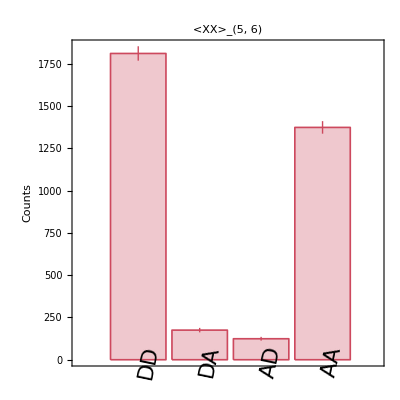

```mathematica
BarChart[Flatten[Accumulate[countsYYXZYYpostSelectAll]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<XX>_(5, 6)"]
```

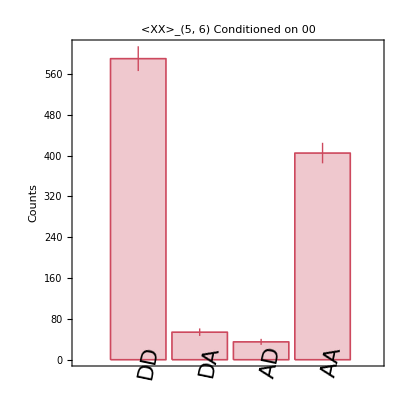

```mathematica
BarChart[Flatten[Accumulate[countsYYXZYYpostSelect00]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<XX>_(5, 6) Conditioned on 00"]
```

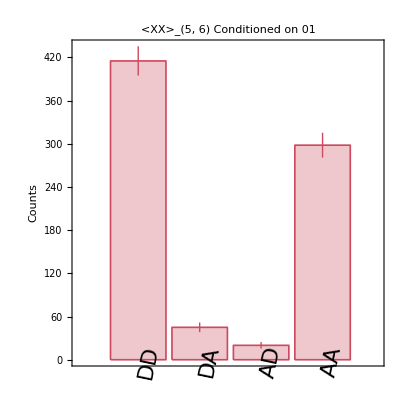

```mathematica
BarChart[Flatten[Accumulate[countsYYXZYYpostSelect01]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<XX>_(5, 6) Conditioned on 01"]
```

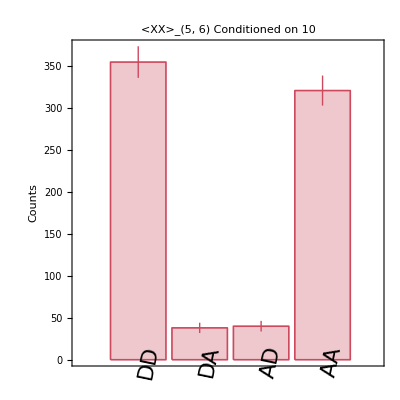

```mathematica
BarChart[Flatten[Accumulate[countsYYXZYYpostSelect10]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<XX>_(5, 6) Conditioned on 10"]
```

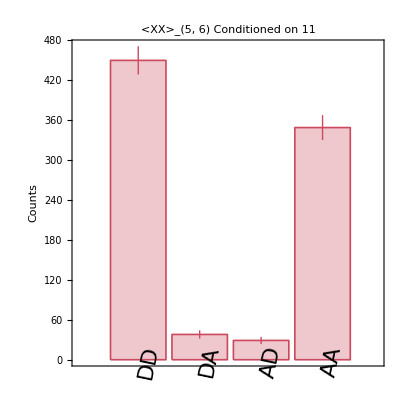

```mathematica
BarChart[Flatten[Accumulate[countsYYXZYYpostSelect11]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<XX>_(5, 6) Conditioned on 11"]
```

### AKR Bell_(5,6)

#### Correct normalisation of data

```mathematica
accumulatedDataXXXZXX=Accumulate@countsXXXZXXpostSelectAllvalue;
accumulatedDataXXXZXXerror=Accumulate@countsXXXZXXpostSelectAll;
```

```mathematica
accumulatedDataYYXZYY=Accumulate@countsYYXZYYpostSelectAllvalue;
accumulatedDataYYXZYYerror=Accumulate@countsYYXZYYpostSelectAll;
```

```mathematica
accumulatedDataXXXZXXnorm=N@accumulatedDataXXXZXX⟦#⟧/Total[accumulatedDataXXXZXX⟦#⟧]&/@Range@Length@accumulatedDataXXXZXX;
accumulatedDataXXXZXXnormError=N@accumulatedDataXXXZXXerror⟦#⟧/Total[accumulatedDataXXXZXXerror⟦#⟧]&/@Range@Length@accumulatedDataXXXZXXerror;

accumulatedDataYYXZYYnorm=N@accumulatedDataYYXZYY⟦#⟧/Total[accumulatedDataYYXZYY⟦#⟧]&/@Range@Length@accumulatedDataYYXZYY;
accumulatedDataYYXZYYnormError=N@accumulatedDataYYXZYYerror⟦#⟧/Total[accumulatedDataYYXZYYerror⟦#⟧]&/@Range@Length@accumulatedDataYYXZYYerror;
```

#### Q_Z

Disparity in first and second index

```mathematica
QAB1=N@Total[Table[#⟦i⟧,{i,{2,3}}]]&/@accumulatedDataXXXZXXnorm;
QAB1Error=N@Total[Table[#⟦i⟧,{i,{2,3}}]]&/@accumulatedDataXXXZXXnormError;
```

```mathematica
QzBell56=QAB1;
```

#### Q_X

```mathematica
Qxpositive=N@Total[Table[#⟦i⟧,{i,{1,4}}]]&/@accumulatedDataYYXZYYnorm;
QxpositiveError=N@Total[Table[#⟦i⟧,{i,{1,4}}]]&/@accumulatedDataYYXZYYnormError;
```

```mathematica
Qxnegative=N@Total[Table[#⟦i⟧,{i,{2,3}}]]&/@accumulatedDataYYXZYYnorm;
QxnegativeError=N@Total[Table[#⟦i⟧,{i,{2,3}}]]&/@accumulatedDataYYXZYYnormError;
```

Evaluating Qx is done by computing by evaluating (1 - (QxPositive - QxNegative)/ (QxPositive + QxNegative)) / 2

```mathematica
QxBell56=((1-(Qxpositive⟦#⟧-Qxnegative⟦#⟧)/(Qxnegative⟦#⟧+Qxpositive⟦#⟧))/2)&/@Range[Length@Qxpositive];
QxBell56Error=((1-(QxpositiveError-QxnegativeError)/(QxnegativeError+QxpositiveError))/2);
```

```mathematica
QxBell56Error
```

{0.0860.013}

#### AKR

```mathematica
{QxBell56⟦-1⟧,QzBell56⟦-1⟧}
```

{0.0858702,0.0738391}

```mathematica
entropy[x_]:=(-x*Log[2,x])-((1-x)*Log[2,1-x])
```

```mathematica
akrBell56=Table[1-entropy[QxBell56⟦i⟧]-entropy[QzBell56⟦i⟧],{i,Range[Length@QxBell56]}];
```

Adding Monte Carlo simultation here based on sampling between the ranges defined by the poissonian uncertainty.

QBER

```mathematica
upperBound=QAB1Error⟦1,1⟧+QAB1Error⟦1,2⟧;
lowerBound=QAB1Error⟦1,1⟧-QAB1Error⟦1,2⟧;
```

```mathematica
errorArrayQBER=Range[lowerBound,upperBound,(upperBound-lowerBound)/1999];
errorArrayQBERsample=Table[RandomSample[errorArrayQBER,1],{i,1,2000}];
```

Qx

```mathematica
upperBound=QxBell56Error⟦1,1⟧+QxBell56Error⟦1,2⟧;
lowerBound=QxBell56Error⟦1,1⟧-QxBell56Error⟦1,2⟧;
```

```mathematica
errorArrayQx=Range[lowerBound,upperBound,(upperBound-lowerBound)/1999];
```

```mathematica
errorArrayQxsample=Table[RandomSample[errorArrayQx,1],{i,1,2000}];
```

AKR

```mathematica
akrArray=1-entropy[errorArrayQxsample⟦#⟧]-entropy[errorArrayQBERsample⟦#⟧]&/@Range[2000];
```

```mathematica
akrStandardDeviation=StandardDeviation[Flatten@akrArray]
akrValue=Mean[Flatten@akrArray]
```

0.0278836

0.196994

#### Summary

```mathematica
(* RESULT BELL 5,6 *)
```

```mathematica
{{"QBER","Qx","AKR","+-"},{QzBell56⟦-1⟧,QxBell56⟦-1⟧,akrBell56⟦-1⟧,akrStandardDeviation}}//TableForm
```

QBER | Qx | AKR | +-
0.0738391 | 0.0858702 | 0.197378 | 0.0278836

```mathematica
{{"QBER","+-","Qx","+-","AKR","+-"},{QAB1Error⟦1,1⟧,QAB1Error⟦1,2⟧,QxBell56Error⟦1,1⟧,QxBell56Error⟦1,2⟧,akrBell56⟦-1⟧,akrStandardDeviation}}//TableForm
```

QBER | +- | Qx | +- | AKR | +-
0.0738391 | 0.00470459 | 0.0858702 | 0.0131546 | 0.197378 | 0.0278836

### Bell ZZ_(2,5) XYXYZY

#### ZZ_(2,5) data

```mathematica
ZZ…0000…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…0000…1346;
ZZ…0001…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…0001…1346;
ZZ…0010…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…0010…1346;
ZZ…0011…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…0011…1346;
ZZ…0100…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…0100…1346;
ZZ…0101…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…0101…1346;
ZZ…0110…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…0110…1346;
ZZ…0111…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…0111…1346;
ZZ…1000…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…1000…1346;
ZZ…1001…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…1001…1346;
ZZ…1010…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…1010…1346;
ZZ…1011…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…1011…1346;
ZZ…1100…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…1100…1346;
ZZ…1101…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…1101…1346;
ZZ…1110…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…1110…1346;
ZZ…1111…Bell25=settingsXYXYZY⟦#⟧&/@Flatten@postSelect…1111…1346;
```

Function for performing flips

```mathematica
FlipQubit[meas_]:=
Join[
meas⟦;;,{1,2,3}⟧⟦#⟧,
StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@meas⟦;;,{4}⟧⟦#⟧,
meas⟦;;,{5,6}⟧⟦#⟧
]&/@Range[Length@meas]
```

```mathematica
FlipQubit5[meas_]:=
Join[
meas⟦;;,{1,2,3,4}⟧⟦#⟧,
StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@meas⟦;;,{5}⟧⟦#⟧,
meas⟦;;,{6}⟧⟦#⟧
]&/@Range[Length@meas]
```

Using function defined above to perform flips

Flip 00_(3,4)

```mathematica
ZZ…0000…Bell25flip=FlipQubit5[FlipQubit@ZZ…0000…Bell25]
ZZ…0001…Bell25flip=FlipQubit5[FlipQubit@ZZ…0001…Bell25]
ZZ…1000…Bell25flip=FlipQubit@ZZ…1000…Bell25
ZZ…1001…Bell25flip=FlipQubit@ZZ…1001…Bell25
```

{{d,r,d,l,v,r},{d,r,d,l,h,r},{d,l,d,l,v,r},{d,l,d,l,h,r}}

{{d,r,d,l,v,l},{d,r,d,l,h,l},{d,l,d,l,v,l},{d,l,d,l,h,l}}

{{a,r,d,l,h,r},{a,r,d,l,v,r},{a,l,d,l,h,r},{a,l,d,l,v,r}}

{{a,r,d,l,h,l},{a,r,d,l,v,l},{a,l,d,l,h,l},{a,l,d,l,v,l}}

Flip 01_(3,4)

```mathematica
ZZ…0010…Bell25flip=FlipQubit@ZZ…0010…Bell25
ZZ…0011…Bell25flip=FlipQubit@ZZ…0011…Bell25
ZZ…1010…Bell25flip=FlipQubit5[FlipQubit@ZZ…1010…Bell25]
ZZ…1011…Bell25flip=FlipQubit5[FlipQubit@ZZ…1011…Bell25]
```

{{d,r,d,r,h,r},{d,r,d,r,v,r},{d,l,d,r,h,r},{d,l,d,r,v,r}}

{{d,r,d,r,h,l},{d,r,d,r,v,l},{d,l,d,r,h,l},{d,l,d,r,v,l}}

{{a,r,d,r,v,r},{a,r,d,r,h,r},{a,l,d,r,v,r},{a,l,d,r,h,r}}

{{a,r,d,r,v,l},{a,r,d,r,h,l},{a,l,d,r,v,l},{a,l,d,r,h,l}}

Flip 10_(3,4)

```mathematica
ZZ…0100…Bell25flip=FlipQubit@ZZ…0100…Bell25
ZZ…0101…Bell25flip=FlipQubit@ZZ…0101…Bell25
ZZ…1100…Bell25flip=FlipQubit5[FlipQubit@ZZ…1100…Bell25]
ZZ…1101…Bell25flip=FlipQubit5[FlipQubit@ZZ…1101…Bell25]
```

{{d,r,a,l,h,r},{d,r,a,l,v,r},{d,l,a,l,h,r},{d,l,a,l,v,r}}

{{d,r,a,l,h,l},{d,r,a,l,v,l},{d,l,a,l,h,l},{d,l,a,l,v,l}}

{{a,r,a,l,v,r},{a,r,a,l,h,r},{a,l,a,l,v,r},{a,l,a,l,h,r}}

{{a,r,a,l,v,l},{a,r,a,l,h,l},{a,l,a,l,v,l},{a,l,a,l,h,l}}

Flip 11_(3,4)

```mathematica
ZZ…0110…Bell25flip=FlipQubit5[FlipQubit@ZZ…0110…Bell25]
ZZ…0111…Bell25flip=FlipQubit5[FlipQubit@ZZ…0111…Bell25]
ZZ…1110…Bell25flip=FlipQubit@ZZ…1110…Bell25
ZZ…1111…Bell25flip=FlipQubit@ZZ…1111…Bell25
```

{{d,r,a,r,v,r},{d,r,a,r,h,r},{d,l,a,r,v,r},{d,l,a,r,h,r}}

{{d,r,a,r,v,l},{d,r,a,r,h,l},{d,l,a,r,v,l},{d,l,a,r,h,l}}

{{a,r,a,r,h,r},{a,r,a,r,v,r},{a,l,a,r,h,r},{a,l,a,r,v,r}}

{{a,r,a,r,h,l},{a,r,a,r,v,l},{a,l,a,r,h,l},{a,l,a,r,v,l}}

```mathematica
ZZ…0000…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…0000…Bell25flip,2]
ZZ…0001…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…0001…Bell25flip,2]
ZZ…0010…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…0010…Bell25flip,2]
ZZ…0011…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…0011…Bell25flip,2]
ZZ…0100…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…0100…Bell25flip,2]
ZZ…0101…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…0101…Bell25flip,2]
ZZ…0110…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…0110…Bell25flip,2]
ZZ…0111…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…0111…Bell25flip,2]
ZZ…1000…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…1000…Bell25flip,2]
ZZ…1001…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…1001…Bell25flip,2]
ZZ…1010…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…1010…Bell25flip,2]
ZZ…1011…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…1011…Bell25flip,2]
ZZ…1100…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…1100…Bell25flip,2]
ZZ…1101…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…1101…Bell25flip,2]
ZZ…1110…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…1110…Bell25flip,2]
ZZ…1111…Bell25position=Flatten[Position[settingsXYXYZY,#]&/@ZZ…1111…Bell25flip,2]
```

{7,5,23,21}

{8,6,24,22}

{1,3,17,19}

{2,4,18,20}

{13,15,29,31}

{14,16,30,32}

{11,9,27,25}

{12,10,28,26}

{37,39,53,55}

{38,40,54,56}

{35,33,51,49}

{36,34,52,50}

{47,45,63,61}

{48,46,64,62}

{41,43,57,59}

{42,44,58,60}

#### Counts

```mathematica
Dimensions[countsXXXZXXpoissonian]
```

{1,64}

```mathematica
countsXYXYZYpostSelect0000=Table[#⟦i⟧,{i,ZZ…0000…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect0000value=Table[#⟦i⟧,{i,ZZ…0000…Bell25position}]&/@countsXYXYZY;

countsXYXYZYpostSelect0100=Table[#⟦i⟧,{i,ZZ…0100…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect0100value=Table[#⟦i⟧,{i,ZZ…0100…Bell25position}]&/@countsXYXYZY;

countsXYXYZYpostSelect1000=Table[#⟦i⟧,{i,ZZ…1000…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect1000value=Table[#⟦i⟧,{i,ZZ…1000…Bell25position}]&/@countsXYXYZY;

countsXYXYZYpostSelect1100=Table[#⟦i⟧,{i,ZZ…1100…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect1100value=Table[#⟦i⟧,{i,ZZ…1100…Bell25position}]&/@countsXYXYZY;
```

Looking at all the outcomes of the above definitions

```mathematica
Total@countsXYXYZYpostSelect0000
Total@countsXYXYZYpostSelect1100
```

{99.10.,8.02.8,7.02.6,120.11.}

{72.8.,16.4.,9.03.0,104.10.}

```mathematica
Total@countsXYXYZYpostSelect0100
Total@countsXYXYZYpostSelect1000
```

{92.10.,11.03.3,9.03.0,71.8.}

{135.12.,8.02.8,20.4.,95.10.}

```mathematica
countsXYXYZYpostSelect0001=Table[#⟦i⟧,{i,ZZ…0001…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect0001value=Table[#⟦i⟧,{i,ZZ…0001…Bell25position}]&/@countsXYXYZY;

countsXYXYZYpostSelect0101=Table[#⟦i⟧,{i,ZZ…0101…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect0101value=Table[#⟦i⟧,{i,ZZ…0101…Bell25position}]&/@countsXYXYZY;

countsXYXYZYpostSelect1001=Table[#⟦i⟧,{i,ZZ…1001…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect1001value=Table[#⟦i⟧,{i,ZZ…1001…Bell25position}]&/@countsXYXYZY;

countsXYXYZYpostSelect1101=Table[#⟦i⟧,{i,ZZ…1101…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect1101value=Table[#⟦i⟧,{i,ZZ…1101…Bell25position}]&/@countsXYXYZY;
```

Looking at all the outcomes of the above definitions

```mathematica
Total@countsXYXYZYpostSelect0001
Total@countsXYXYZYpostSelect1101
```

{96.10.,13.4.,6.02.4,91.10.}

{84.9.,11.03.3,7.02.6,94.10.}

```mathematica
Total@countsXYXYZYpostSelect0101
Total@countsXYXYZYpostSelect1001
```

{93.10.,10.03.2,13.4.,93.10.}

{132.11.,13.4.,23.5.,111.11.}

```mathematica
countsXYXYZYpostSelect0010=Table[#⟦i⟧,{i,ZZ…0010…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect0010value=Table[#⟦i⟧,{i,ZZ…0010…Bell25position}]&/@countsXYXYZY;

countsXYXYZYpostSelect0110=Table[#⟦i⟧,{i,ZZ…0110…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect0110value=Table[#⟦i⟧,{i,ZZ…0110…Bell25position}]&/@countsXYXYZY;

countsXYXYZYpostSelect1010=Table[#⟦i⟧,{i,ZZ…1010…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect1010value=Table[#⟦i⟧,{i,ZZ…1010…Bell25position}]&/@countsXYXYZY;

countsXYXYZYpostSelect1110=Table[#⟦i⟧,{i,ZZ…1110…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect1110value=Table[#⟦i⟧,{i,ZZ…1110…Bell25position}]&/@countsXYXYZY;
```

Looking at all the outcomes of the above definitions

```mathematica
Total@countsXYXYZYpostSelect0010
Total@countsXYXYZYpostSelect1110
```

{129.11.,12.03.5,18.4.,88.9.}

{120.11.,8.02.8,8.02.8,73.9.}

```mathematica
Total@countsXYXYZYpostSelect0110
Total@countsXYXYZYpostSelect1010
```

{82.9.,12.03.5,17.4.,105.10.}

{100.10.,9.03.0,8.02.8,111.11.}

```mathematica
countsXYXYZYpostSelect0011=Table[#⟦i⟧,{i,ZZ…0011…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect0011value=Table[#⟦i⟧,{i,ZZ…0011…Bell25position}]&/@countsXYXYZY;

countsXYXYZYpostSelect0111=Table[#⟦i⟧,{i,ZZ…0111…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect0111value=Table[#⟦i⟧,{i,ZZ…0111…Bell25position}]&/@countsXYXYZY;

countsXYXYZYpostSelect1011=Table[#⟦i⟧,{i,ZZ…1011…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect1011value=Table[#⟦i⟧,{i,ZZ…1011…Bell25position}]&/@countsXYXYZY;

countsXYXYZYpostSelect1111=Table[#⟦i⟧,{i,ZZ…1111…Bell25position}]&/@countsXYXYZYpoissonian;
countsXYXYZYpostSelect1111value=Table[#⟦i⟧,{i,ZZ…1111…Bell25position}]&/@countsXYXYZY;
```

Looking at all the outcomes of the above definitions

```mathematica
Total@countsXYXYZYpostSelect0011
Total@countsXYXYZYpostSelect1111
```

{110.10.,8.02.8,12.03.5,95.10.}

{105.10.,11.03.3,9.03.0,77.9.}

```mathematica
Total@countsXYXYZYpostSelect0111
Total@countsXYXYZYpostSelect1011
```

{93.10.,16.4.,10.03.2,103.10.}

{110.10.,12.03.5,9.03.0,121.11.}

Summing all the counts

```mathematica
countsXYXYZYpostSelectAll=countsXYXYZYpostSelect0000+countsXYXYZYpostSelect0001+countsXYXYZYpostSelect0010+countsXYXYZYpostSelect0011+countsXYXYZYpostSelect0100+countsXYXYZYpostSelect0101+countsXYXYZYpostSelect0110+countsXYXYZYpostSelect0111+countsXYXYZYpostSelect1000+countsXYXYZYpostSelect1001+countsXYXYZYpostSelect1010+countsXYXYZYpostSelect1011+countsXYXYZYpostSelect1100+countsXYXYZYpostSelect1101+countsXYXYZYpostSelect1110+countsXYXYZYpostSelect1111
```

{{1652.41.,178.13.,185.14.,1552.39.}}

```mathematica
countsXYXYZYpostSelectAllvalue=countsXYXYZYpostSelect0000value+countsXYXYZYpostSelect0001value+countsXYXYZYpostSelect0010value+countsXYXYZYpostSelect0011value+countsXYXYZYpostSelect0100value+countsXYXYZYpostSelect0101value+countsXYXYZYpostSelect0110value+countsXYXYZYpostSelect0111value+countsXYXYZYpostSelect1000value+countsXYXYZYpostSelect1001value+countsXYXYZYpostSelect1010value+countsXYXYZYpostSelect1011value+countsXYXYZYpostSelect1100value+countsXYXYZYpostSelect1101value+countsXYXYZYpostSelect1110value+countsXYXYZYpostSelect1111value
```

{{0.,1.,0.,3.},{2.,1.,0.,2.},{5.,0.,0.,4.},{1.,0.,0.,1.},{7.,0.,1.,3.},{2.,1.,0.,3.},{3.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,2.},{3.,0.,0.,2.},{4.,0.,0.,1.},{3.,0.,0.,2.},{4.,0.,0.,1.},{2.,1.,0.,4.},{0.,0.,0.,2.},{2.,0.,0.,3.},{4.,0.,1.,6.},{7.,0.,0.,2.},{3.,0.,0.,2.},{2.,0.,1.,3.},{3.,0.,0.,3.},{2.,0.,1.,4.},{0.,0.,1.,2.},{5.,1.,0.,0.},{3.,0.,1.,1.},{1.,0.,1.,4.},{2.,0.,1.,4.},{1.,0.,0.,1.},{3.,0.,0.,1.},{3.,1.,1.,3.},{4.,2.,1.,0.},{1.,0.,0.,2.},{4.,1.,2.,0.},{2.,0.,1.,3.},{2.,0.,0.,2.},{2.,0.,0.,2.},{2.,0.,0.,3.},{3.,0.,0.,4.},{3.,0.,0.,2.},{0.,0.,0.,2.},{3.,1.,1.,2.},{4.,0.,0.,5.},{1.,0.,1.,3.},{2.,0.,0.,1.},{3.,1.,0.,0.},{2.,0.,0.,3.},{4.,1.,0.,3.},{3.,0.,0.,0.},{7.,0.,0.,2.},{3.,1.,0.,2.},{3.,1.,0.,2.},{2.,0.,0.,2.},{2.,0.,2.,0.},{2.,0.,0.,4.},{4.,1.,0.,3.},{2.,0.,0.,2.},{3.,0.,0.,3.},{2.,1.,0.,4.},{0.,1.,0.,2.},{6.,0.,1.,2.},{3.,0.,0.,3.},{3.,0.,0.,2.},{2.,0.,1.,2.},{3.,0.,0.,2.},{2.,0.,0.,2.},{3.,0.,1.,0.},{1.,0.,0.,2.},{3.,2.,0.,2.},{0.,0.,0.,3.},{1.,0.,0.,0.},{3.,0.,0.,4.},{2.,0.,1.,5.},{1.,0.,0.,6.},{6.,0.,0.,4.},{2.,1.,0.,2.},{0.,0.,0.,4.},{1.,0.,0.,2.},{0.,0.,1.,3.},{0.,0.,1.,3.},{2.,1.,0.,4.},{2.,0.,0.,2.},{2.,0.,0.,1.},{3.,0.,1.,4.},{1.,1.,0.,0.},{1.,1.,0.,0.},{2.,0.,0.,5.},{2.,0.,0.,0.},{1.,0.,0.,2.},{3.,1.,1.,5.},{3.,0.,1.,4.},{2.,0.,0.,3.},{2.,0.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,1.},{11.,1.,0.,5.},{4.,0.,1.,2.},{2.,2.,0.,4.},{4.,1.,0.,3.},{1.,0.,0.,3.},{4.,0.,2.,1.},{1.,0.,0.,2.},{2.,0.,0.,2.},{2.,0.,0.,2.},{4.,0.,0.,1.},{3.,0.,0.,2.},{1.,0.,0.,2.},{2.,0.,2.,1.},{1.,0.,0.,2.},{1.,0.,1.,2.},{2.,0.,0.,4.},{1.,0.,0.,1.},{1.,0.,0.,0.},{5.,0.,0.,1.},{2.,0.,0.,3.},{3.,0.,0.,1.},{6.,0.,0.,1.},{2.,0.,1.,1.},{3.,0.,0.,1.},{2.,0.,1.,1.},{2.,1.,0.,1.},{1.,1.,1.,3.},{0.,0.,0.,1.},{3.,1.,0.,3.},{1.,0.,1.,3.},{3.,0.,2.,1.},{3.,0.,0.,4.},{6.,0.,0.,1.},{4.,2.,0.,2.},{2.,0.,0.,4.},{2.,0.,0.,7.},{2.,1.,0.,5.},{1.,1.,1.,2.},{1.,1.,1.,2.},{4.,2.,0.,0.},{2.,1.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,4.},{2.,0.,0.,3.},{1.,0.,1.,2.},{4.,0.,0.,4.},{1.,2.,0.,2.},{3.,1.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,1.},{1.,1.,1.,3.},{1.,1.,0.,1.},{2.,0.,1.,4.},{3.,0.,0.,1.},{2.,0.,0.,3.},{1.,0.,0.,1.},{4.,0.,0.,2.},{5.,0.,1.,4.},{5.,0.,0.,7.},{0.,0.,0.,2.},{2.,1.,1.,2.},{0.,1.,0.,0.},{4.,0.,0.,2.},{1.,0.,0.,4.},{2.,0.,0.,2.},{0.,0.,0.,1.},{4.,0.,1.,0.},{2.,0.,0.,1.},{1.,0.,0.,2.},{4.,1.,0.,2.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,1.,2.},{1.,0.,0.,3.},{3.,0.,0.,4.},{2.,0.,2.,2.},{1.,0.,0.,1.},{2.,0.,1.,5.},{6.,1.,1.,2.},{3.,0.,0.,1.},{3.,2.,0.,2.},{4.,2.,1.,4.},{4.,1.,0.,2.},{3.,0.,0.,4.},{5.,1.,0.,3.},{2.,0.,0.,0.},{4.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,5.},{4.,1.,0.,3.},{1.,0.,1.,4.},{1.,0.,0.,2.},{3.,0.,0.,1.},{1.,1.,0.,1.},{3.,0.,1.,2.},{3.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,4.},{6.,0.,0.,2.},{2.,2.,0.,2.},{1.,0.,1.,1.},{1.,0.,0.,6.},{4.,0.,0.,4.},{1.,1.,0.,3.},{2.,0.,0.,3.},{2.,0.,0.,2.},{0.,0.,1.,1.},{0.,0.,0.,2.},{2.,0.,1.,2.},{4.,0.,0.,2.},{2.,0.,1.,2.},{1.,0.,0.,3.},{4.,0.,0.,3.},{1.,0.,0.,3.},{0.,0.,0.,4.},{3.,0.,0.,1.},{6.,0.,2.,3.},{1.,1.,0.,4.},{4.,0.,0.,1.},{3.,0.,1.,1.},{0.,1.,1.,1.},{0.,1.,0.,4.},{1.,0.,0.,2.},{3.,1.,0.,1.},{0.,0.,0.,2.},{2.,1.,0.,1.},{0.,0.,0.,2.},{2.,1.,0.,5.},{2.,0.,0.,1.},{0.,0.,0.,4.},{2.,0.,0.,2.},{3.,0.,1.,3.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,1.,2.},{3.,0.,0.,2.},{4.,0.,1.,1.},{3.,0.,0.,3.},{2.,0.,0.,0.},{2.,0.,0.,0.},{6.,0.,0.,3.},{2.,0.,0.,1.},{4.,0.,0.,1.},{0.,0.,1.,3.},{3.,0.,0.,4.},{3.,0.,0.,2.},{5.,1.,1.,2.},{2.,3.,1.,2.},{4.,0.,2.,6.},{2.,0.,0.,7.},{3.,0.,0.,2.},{1.,0.,0.,4.},{1.,0.,0.,4.},{3.,1.,0.,2.},{1.,0.,0.,2.},{4.,1.,0.,2.},{1.,0.,0.,3.},{1.,0.,1.,2.},{2.,1.,0.,1.},{1.,0.,1.,3.},{4.,0.,0.,2.},{2.,0.,0.,4.},{2.,1.,0.,3.},{3.,0.,1.,0.},{4.,0.,0.,2.},{2.,0.,0.,5.},{3.,0.,0.,3.},{0.,0.,1.,4.},{5.,0.,0.,1.},{0.,0.,0.,1.},{2.,1.,0.,3.},{1.,0.,0.,3.},{4.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{4.,1.,0.,3.},{2.,1.,0.,2.},{5.,1.,0.,1.},{1.,0.,0.,1.},{4.,0.,0.,0.},{2.,1.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{7.,0.,0.,2.},{2.,1.,0.,1.},{4.,2.,0.,2.},{1.,0.,0.,2.},{3.,0.,0.,2.},{2.,0.,1.,4.},{0.,0.,0.,1.},{1.,0.,0.,3.},{1.,0.,2.,2.},{0.,1.,0.,2.},{2.,0.,0.,1.},{5.,0.,0.,3.},{2.,0.,0.,3.},{1.,0.,0.,1.},{7.,1.,0.,3.},{2.,0.,0.,1.},{1.,0.,0.,3.},{0.,0.,1.,3.},{6.,0.,0.,2.},{3.,0.,0.,0.},{2.,0.,0.,0.},{3.,1.,1.,3.},{0.,0.,0.,3.},{1.,1.,0.,1.},{1.,0.,0.,4.},{1.,0.,0.,2.},{1.,1.,0.,2.},{0.,0.,0.,2.},{1.,0.,0.,1.},{2.,0.,0.,2.},{1.,0.,1.,3.},{0.,0.,0.,1.},{3.,0.,0.,2.},{2.,0.,1.,3.},{2.,0.,0.,2.},{2.,0.,0.,0.},{2.,0.,0.,2.},{2.,0.,0.,3.},{2.,0.,0.,0.},{2.,0.,0.,2.},{3.,0.,0.,3.},{1.,0.,0.,3.},{2.,0.,0.,2.},{4.,1.,0.,3.},{1.,0.,0.,3.},{1.,1.,0.,2.},{5.,0.,0.,7.},{1.,1.,0.,6.},{3.,0.,0.,0.},{4.,0.,1.,1.},{3.,0.,0.,4.},{2.,0.,0.,3.},{0.,0.,0.,0.},{4.,0.,0.,3.},{1.,0.,0.,5.},{1.,0.,0.,1.},{3.,0.,0.,3.},{0.,0.,0.,1.},{3.,0.,0.,5.},{1.,0.,0.,1.},{2.,0.,0.,3.},{1.,0.,0.,2.},{4.,0.,1.,3.},{1.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,1.,2.},{1.,0.,0.,3.},{0.,0.,0.,0.},{3.,0.,0.,1.},{2.,0.,0.,3.},{3.,0.,0.,2.},{0.,0.,0.,2.},{6.,0.,1.,2.},{2.,0.,0.,1.},{4.,0.,0.,2.},{1.,0.,0.,4.},{0.,0.,0.,1.},{3.,0.,1.,3.},{1.,0.,0.,4.},{3.,0.,0.,4.},{3.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,2.},{1.,0.,0.,1.},{1.,1.,1.,0.},{2.,1.,0.,3.},{3.,0.,1.,0.},{8.,0.,0.,0.},{1.,0.,0.,6.},{1.,1.,0.,1.},{4.,0.,0.,2.},{1.,0.,1.,0.},{1.,0.,0.,1.},{2.,1.,0.,3.},{1.,1.,1.,0.},{5.,0.,0.,2.},{2.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,1.,4.},{5.,0.,0.,1.},{2.,0.,0.,4.},{1.,0.,1.,1.},{2.,0.,0.,2.},{1.,1.,0.,2.},{2.,1.,0.,2.},{2.,0.,1.,3.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,4.},{2.,0.,1.,1.},{1.,0.,0.,0.},{1.,1.,0.,3.},{3.,0.,0.,2.},{1.,0.,1.,1.},{1.,0.,0.,0.},{3.,0.,0.,0.},{3.,0.,0.,2.},{2.,0.,0.,4.},{1.,0.,0.,3.},{3.,0.,0.,0.},{1.,0.,1.,2.},{3.,1.,0.,4.},{0.,0.,0.,0.},{4.,0.,0.,1.},{3.,1.,0.,3.},{0.,0.,0.,4.},{2.,1.,0.,5.},{4.,1.,1.,4.},{1.,1.,0.,0.},{3.,0.,2.,3.},{2.,0.,0.,3.},{1.,0.,0.,5.},{0.,0.,1.,3.},{1.,0.,0.,3.},{3.,0.,0.,3.},{2.,0.,1.,0.},{1.,0.,1.,2.},{1.,0.,0.,3.},{1.,0.,1.,4.},{2.,0.,0.,3.},{2.,0.,0.,3.},{2.,1.,0.,0.},{1.,0.,1.,3.},{3.,0.,1.,3.},{3.,0.,1.,0.},{2.,0.,0.,3.},{1.,1.,0.,1.},{3.,0.,1.,1.},{2.,0.,0.,0.},{3.,1.,0.,3.},{0.,0.,1.,1.},{2.,0.,0.,1.},{3.,1.,0.,4.},{1.,0.,0.,0.},{2.,0.,1.,3.},{1.,0.,0.,2.},{1.,0.,0.,4.},{1.,0.,0.,3.},{1.,0.,1.,2.},{2.,0.,1.,3.},{4.,0.,0.,2.},{3.,0.,1.,2.},{3.,0.,1.,1.},{5.,0.,0.,2.},{4.,0.,0.,3.},{3.,0.,0.,1.},{1.,0.,0.,1.},{1.,1.,0.,3.},{4.,0.,0.,1.},{1.,0.,0.,1.},{3.,0.,2.,4.},{3.,0.,0.,2.},{5.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,1.},{2.,1.,1.,2.},{2.,0.,0.,0.},{2.,0.,0.,4.},{2.,0.,0.,1.},{2.,1.,1.,2.},{3.,0.,0.,0.},{1.,0.,0.,5.},{6.,0.,0.,2.},{2.,0.,0.,1.},{3.,0.,0.,1.},{1.,0.,1.,2.},{2.,1.,1.,2.},{1.,0.,0.,2.},{1.,1.,0.,2.},{2.,0.,1.,3.},{2.,0.,0.,1.},{2.,0.,0.,2.},{1.,0.,0.,4.},{0.,0.,0.,0.},{2.,0.,1.,2.},{1.,0.,1.,1.},{0.,0.,0.,1.},{3.,0.,0.,1.},{3.,1.,0.,3.},{3.,0.,0.,0.},{2.,0.,0.,5.},{1.,0.,0.,1.},{5.,0.,0.,2.},{2.,0.,1.,1.},{2.,1.,0.,3.},{2.,1.,0.,3.},{2.,0.,0.,1.},{2.,0.,0.,2.},{4.,0.,0.,1.},{1.,0.,0.,1.},{0.,1.,1.,2.},{3.,0.,1.,0.},{4.,0.,0.,2.},{2.,0.,0.,5.},{4.,0.,0.,3.},{2.,0.,0.,4.},{3.,0.,1.,2.},{5.,0.,0.,1.},{5.,0.,0.,2.},{3.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,3.},{3.,1.,0.,2.},{1.,0.,0.,3.},{0.,0.,0.,3.},{3.,0.,1.,4.},{2.,1.,0.,2.},{3.,0.,0.,1.},{0.,0.,0.,0.},{2.,1.,0.,2.},{2.,1.,1.,2.},{1.,0.,1.,3.},{0.,0.,0.,2.},{3.,0.,0.,1.},{0.,0.,0.,2.},{5.,1.,0.,2.},{1.,0.,0.,1.},{3.,1.,0.,2.},{1.,0.,0.,1.},{3.,0.,0.,2.},{1.,0.,0.,1.},{5.,1.,0.,3.},{2.,0.,0.,1.},{4.,0.,0.,1.},{1.,0.,0.,1.},{0.,1.,0.,2.},{0.,0.,0.,4.},{2.,1.,1.,7.},{3.,1.,0.,0.},{1.,0.,0.,3.},{2.,0.,0.,2.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,1.,1.},{1.,0.,0.,2.},{1.,0.,0.,2.},{0.,0.,0.,3.},{1.,0.,0.,5.},{3.,1.,1.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{2.,1.,0.,1.},{0.,0.,1.,2.},{2.,0.,0.,3.},{2.,0.,0.,1.},{4.,1.,0.,0.},{3.,0.,0.,0.},{1.,1.,0.,4.},{0.,0.,0.,5.},{1.,1.,0.,0.},{2.,0.,0.,2.},{3.,0.,2.,1.},{3.,0.,0.,3.},{1.,0.,0.,0.},{3.,0.,0.,1.},{1.,1.,0.,1.},{1.,1.,0.,0.},{1.,0.,0.,4.},{0.,0.,0.,3.},{0.,0.,1.,4.},{4.,0.,0.,0.},{1.,0.,0.,2.},{3.,0.,0.,1.},{4.,0.,0.,1.},{1.,1.,0.,2.},{5.,1.,0.,0.},{3.,0.,0.,1.},{5.,0.,1.,4.},{0.,0.,0.,1.},{0.,0.,0.,0.},{4.,1.,0.,0.},{3.,1.,0.,3.},{0.,0.,0.,2.},{3.,0.,2.,1.},{2.,0.,0.,1.},{3.,1.,0.,1.},{2.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,1.},{3.,0.,0.,2.},{1.,0.,0.,3.},{1.,0.,0.,3.},{1.,0.,0.,3.},{1.,0.,0.,3.},{3.,1.,0.,0.},{3.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,1.},{2.,0.,0.,1.},{3.,1.,1.,0.},{3.,0.,0.,6.},{2.,0.,0.,2.},{3.,0.,0.,1.},{2.,0.,0.,0.},{2.,1.,1.,1.},{1.,0.,1.,1.},{2.,0.,1.,1.},{5.,0.,1.,0.},{3.,0.,0.,5.},{1.,0.,0.,0.},{2.,0.,0.,2.},{3.,0.,0.,1.},{2.,1.,0.,1.},{4.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,1.},{1.,1.,0.,1.},{2.,0.,0.,2.},{1.,0.,0.,3.},{3.,0.,0.,0.},{4.,0.,0.,2.},{3.,1.,0.,1.},{3.,1.,0.,0.},{1.,0.,0.,2.},{3.,0.,0.,0.},{0.,0.,0.,3.},{4.,0.,0.,1.},{5.,2.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,0.},{1.,1.,0.,3.},{1.,0.,0.,1.},{1.,1.,0.,2.},{2.,1.,0.,4.},{5.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,3.},{4.,0.,1.,2.},{4.,0.,0.,5.},{4.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,2.},{5.,0.,0.,2.},{3.,0.,0.,1.},{2.,0.,0.,2.},{4.,0.,0.,4.},{1.,1.,2.,2.},{0.,0.,0.,3.},{1.,1.,0.,1.},{1.,0.,0.,1.},{4.,1.,0.,3.},{2.,0.,0.,3.},{2.,0.,0.,1.},{6.,0.,0.,0.},{2.,0.,0.,2.},{3.,0.,0.,3.},{3.,0.,1.,0.},{2.,0.,0.,1.},{3.,0.,0.,0.},{2.,0.,0.,4.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,1.,0.},{4.,0.,0.,2.},{2.,1.,0.,1.},{5.,0.,0.,1.},{3.,0.,0.,5.},{1.,0.,1.,2.},{1.,0.,0.,1.},{1.,0.,1.,1.},{0.,0.,0.,2.},{2.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,2.},{4.,0.,0.,1.},{4.,0.,0.,0.},{0.,1.,0.,2.},{0.,1.,2.,2.},{0.,0.,0.,2.},{4.,1.,0.,0.},{2.,0.,1.,3.},{0.,0.,1.,1.},{4.,0.,0.,0.},{0.,0.,1.,0.},{2.,0.,0.,2.},{1.,0.,1.,0.},{4.,0.,0.,4.},{2.,0.,0.,1.},{1.,0.,0.,3.},{0.,0.,0.,2.},{4.,0.,0.,1.},{3.,0.,0.,2.},{4.,1.,0.,1.},{1.,0.,0.,1.},{2.,0.,2.,1.},{1.,0.,0.,1.},{2.,0.,1.,2.},{2.,0.,0.,1.},{3.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,4.},{3.,0.,1.,1.},{4.,0.,1.,1.},{3.,0.,1.,0.},{1.,0.,0.,0.},{3.,0.,0.,1.},{1.,0.,0.,1.},{2.,1.,0.,1.},{4.,1.,0.,2.},{2.,0.,0.,1.},{1.,0.,1.,1.},{2.,0.,0.,1.},{4.,0.,0.,3.},{1.,0.,0.,0.},{2.,0.,0.,0.},{4.,1.,1.,4.},{3.,1.,0.,0.},{1.,0.,0.,1.},{4.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,3.},{0.,0.,1.,2.},{1.,0.,0.,5.},{2.,0.,0.,2.},{2.,1.,0.,1.},{2.,0.,0.,5.},{2.,0.,0.,3.},{2.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,1.,1.},{4.,1.,0.,4.},{1.,0.,0.,1.},{1.,1.,0.,3.},{1.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,4.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{3.,1.,1.,0.},{0.,0.,0.,1.},{2.,0.,1.,3.},{1.,0.,0.,0.},{2.,0.,0.,4.},{1.,0.,0.,1.},{2.,1.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{4.,1.,0.,2.},{0.,0.,1.,2.},{3.,0.,0.,3.},{2.,1.,0.,1.},{1.,0.,0.,1.},{2.,1.,0.,0.},{0.,1.,0.,2.},{1.,0.,0.,5.},{1.,0.,0.,3.},{1.,0.,1.,2.},{1.,0.,0.,1.},{1.,0.,1.,1.},{2.,0.,0.,0.},{1.,0.,0.,2.},{3.,0.,1.,0.},{2.,0.,1.,3.},{3.,0.,0.,1.},{3.,0.,1.,1.},{0.,0.,0.,3.},{0.,1.,0.,1.},{1.,1.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,2.},{1.,0.,0.,3.},{3.,0.,0.,3.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,1.,0.},{2.,0.,1.,5.},{1.,0.,1.,2.},{0.,1.,0.,2.},{2.,0.,0.,3.},{0.,0.,1.,4.},{1.,1.,0.,3.},{1.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,1.,4.},{0.,1.,0.,1.},{3.,0.,1.,3.},{2.,0.,0.,1.},{1.,0.,0.,2.},{3.,0.,1.,3.},{1.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,4.},{1.,0.,0.,0.},{3.,0.,0.,0.},{2.,0.,0.,3.}}

```mathematica
countsXYXYZYpostSelect00=countsXYXYZYpostSelect0000+countsXYXYZYpostSelect0001+countsXYXYZYpostSelect1000+countsXYXYZYpostSelect1001

countsXYXYZYpostSelect01=countsXYXYZYpostSelect0010+countsXYXYZYpostSelect0011+countsXYXYZYpostSelect1010+countsXYXYZYpostSelect1011

countsXYXYZYpostSelect10=countsXYXYZYpostSelect0100+countsXYXYZYpostSelect0101+countsXYXYZYpostSelect1100+countsXYXYZYpostSelect1101

countsXYXYZYpostSelect11=countsXYXYZYpostSelect0110+countsXYXYZYpostSelect0111+countsXYXYZYpostSelect1110+countsXYXYZYpostSelect1111
```

{{462.21.,42.6.,56.7.,417.20.}}

{{449.21.,41.6.,47.7.,415.20.}}

{{341.18.,48.7.,38.6.,362.19.}}

{{400.20.,47.7.,44.7.,358.19.}}

```mathematica
(* testing the count positions *)
countsXYXYZYpostSelect00=countsXYXYZYpostSelect0000+countsXYXYZYpostSelect0001+countsXYXYZYpostSelect1000+countsXYXYZYpostSelect1001;
Accumulate@%
```

{{462.21.,42.6.,56.7.,417.20.}}

```mathematica
countsXYXYZYpostSelect00value=countsXYXYZYpostSelect0000value+countsXYXYZYpostSelect0001value+countsXYXYZYpostSelect1000value+countsXYXYZYpostSelect1001value

countsXYXYZYpostSelect01value=countsXYXYZYpostSelect0010value+countsXYXYZYpostSelect0011value+countsXYXYZYpostSelect1010value+countsXYXYZYpostSelect1011value

countsXYXYZYpostSelect10value=countsXYXYZYpostSelect0100value+countsXYXYZYpostSelect0101value+countsXYXYZYpostSelect1100value+countsXYXYZYpostSelect1101value

countsXYXYZYpostSelect11value=countsXYXYZYpostSelect0110value+countsXYXYZYpostSelect0111value+countsXYXYZYpostSelect1110value+countsXXXZXXpostSelect1111value
```

{{0.,1.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,2.},{0.,0.,0.,0.},{3.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,1.,0.},{2.,0.,0.,1.},{2.,0.,0.,2.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,1.,3.},{0.,0.,1.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,1.,0.},{0.,0.,1.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{3.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,1.,0.},{2.,0.,0.,1.},{1.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,2.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,1.,1.},{1.,0.,0.,2.},{1.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,3.},{2.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,2.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,1.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,1.},{1.,0.,0.,3.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,2.},{2.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{3.,1.,1.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{2.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,1.,0.},{1.,1.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,1.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{2.,0.,0.,0.},{2.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,1.,3.},{1.,0.,0.,2.},{2.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{3.,1.,0.,1.},{2.,0.,0.,1.},{2.,1.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,1.,0.,0.},{1.,1.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{3.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,1.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{3.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,1.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{4.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{4.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,1.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,1.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,2.},{3.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,3.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,3.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{2.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,1.,1.},{1.,1.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,1.,1.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,1.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,1.,0.},{2.,0.,0.,1.},{2.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,1.,1.},{1.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,1.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,1.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,3.},{0.,0.,0.,0.},{1.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,2.},{1.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,2.},{0.,0.,1.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,2.},{0.,1.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.}}

{{0.,0.,0.,3.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,1.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,3.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,1.,1.},{1.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,1.,0.,0.},{2.,1.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,1.,0.,0.},{3.,0.,1.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,3.},{0.,0.,0.,3.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,2.},{1.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,1.,1.},{1.,0.,1.,0.},{2.,0.,0.,1.},{3.,0.,0.,1.},{3.,1.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,3.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{1.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,1.,1.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,1.},{0.,0.,0.,2.},{2.,0.,0.,1.},{0.,0.,1.,1.},{1.,0.,0.,0.},{0.,0.,1.,3.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,1.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{4.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{2.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,1.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,1.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,1.,0.},{2.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{4.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,3.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,2.,3.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{4.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,1.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,1.},{1.,1.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,2.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{1.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,2.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,1.},{2.,1.,0.,0.},{4.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{3.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.}}

{{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,1.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,1.,0.,0.},{1.,1.,1.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,1.},{0.,1.,0.,3.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,1.,1.},{0.,0.,1.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,1.,0.,1.},{2.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,2.,0.,1.},{1.,1.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,0.},{3.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,1.,1.,0.},{1.,0.,1.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{3.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{3.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,1.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,1.},{3.,0.,0.,3.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,2.},{0.,0.,0.,0.},{1.,0.,1.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{4.,1.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,3.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,1.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{3.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,1.,0.},{1.,0.,0.,3.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,3.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,3.},{1.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{3.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,1.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}

{{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,3.},{1.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,1.,0.},{0.,0.,0.,1.},{0.,1.,0.,2.},{1.,0.,0.,0.},{2.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,1.},{2.,0.,1.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,3.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,1.,2.},{0.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,1.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,3.},{0.,0.,1.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,2.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,1.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,1.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,1.,0.,0.},{0.,0.,1.,1.},{0.,0.,1.,2.},{0.,0.,0.,0.},{2.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,1.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{1.,1.,1.,0.},{0.,1.,0.,1.},{1.,0.,0.,0.},{3.,2.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,1.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,3.},{0.,0.,0.,1.},{1.,0.,1.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,1.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,1.},{0.,1.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,2.},{2.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,1.,1.},{1.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,1.},{0.,0.,0.,3.},{1.,1.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,2.},{0.,1.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,1.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,1.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,2.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,2.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,1.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,3.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,1.,0.,2.},{1.,1.,1.,1.},{1.,1.,0.,1.},{3.,0.,0.,2.},{0.,0.,1.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,3.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,3.},{1.,0.,0.,2.},{0.,0.,0.,2.},{0.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,1.,1.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,1.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,1.,2.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,2.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,1.,0.,0.},{2.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,2.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,1.,2.},{2.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,3.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{1.,1.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{2.,1.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,1.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{3.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,1.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,1.}}

```mathematica
Total[countsXYXYZYpostSelect00]
Total[countsXYXYZYpostSelect01]
Total[countsXYXYZYpostSelect10]
Total[countsXYXYZYpostSelect11]
```

{462.21.,42.6.,56.7.,417.20.}

{449.21.,41.6.,47.7.,415.20.}

{341.18.,48.7.,38.6.,362.19.}

{400.20.,47.7.,44.7.,358.19.}

#### Labels for plotting Bell state populations

```mathematica
bellLabels=Tuples[{"H","V"},2];
bellLabels=StringReplace[ToString[#],{","->""," "->"","{"->"","}"->""}]&/@%
```

{HH,HV,VH,VV}

#### ZZ_(2,5)

```mathematica
scale=Total[Accumulate[countsXYXYZYpostSelectAll]⟦-1⟧];
scale=scale["Value"];
phiplus=1/√2(Kron[h,h]+Kron[v,v]);
Flatten[(#†.phiplus)&/@projections];
projections=Kronk/@Tuples[{h,v},2];
theoryPopulationsGHZ=Flatten[(#†.phiplus)&/@projections]*scale/√2;
stackedData={Flatten@theoryPopulationsGHZ,Flatten[Accumulate[countsXYXYZYpostSelectAll]⟦-1⟧]}†;
```

```mathematica
BarChartSettings={ImageSize->400
,LabelStyle->Directive[FontFamily->"Menlo",FontSize->22,Black]
,ChartStyle->Directive[rocketColors⟦2⟧,Opacity[0.3],EdgeForm[{rocketColors⟦2⟧,Thickness[0.003],Opacity[1]}]]
,IntervalMarkers->"Fences"
,AspectRatio->1/2
,Frame->True
,IntervalMarkersStyle->Directive[rocketColors⟦2⟧,Thick]
,FrameLabel->{"",Style["Counts",FontFamily->"Times New Roman"]}
};
```

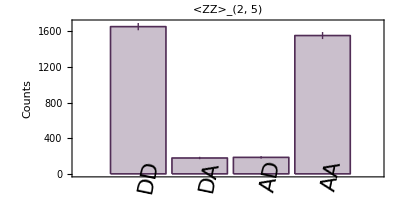

```mathematica
BarChart[Flatten[Accumulate[countsXYXYZYpostSelectAll]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(2, 5)"]
```

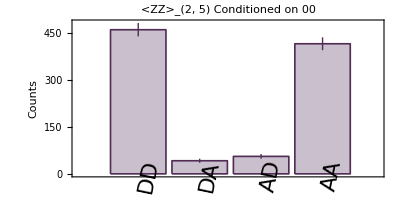

```mathematica
BarChart[Flatten[Accumulate[countsXYXYZYpostSelect00]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(2, 5) Conditioned on 00"]
```

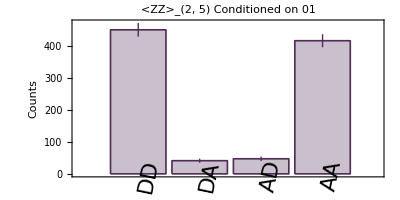

```mathematica
BarChart[Flatten[Accumulate[countsXYXYZYpostSelect01]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(2, 5) Conditioned on 01"]
```

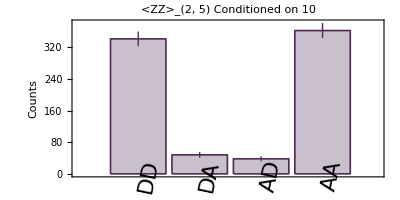

```mathematica
BarChart[Flatten[Accumulate[countsXYXYZYpostSelect10]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(2, 5) Conditioned on 10"]
```

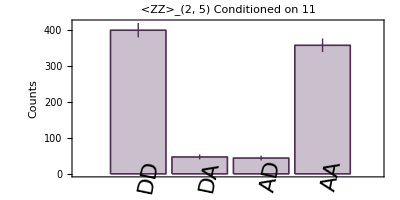

```mathematica
BarChart[Flatten[Accumulate[countsXYXYZYpostSelect11]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(2, 5) Conditioned on 11"]
```

### Bell XX_(2,5) XZXYXY

#### XX_(2,5) data

```mathematica
XX0000Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…0000…1346;
XX0001Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…0001…1346;
XX0010Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…0010…1346;
XX0011Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…0011…1346;
XX0100Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…0100…1346;
XX0101Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…0101…1346;
XX0110Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…0110…1346;
XX0111Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…0111…1346;
XX1000Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…1000…1346;
XX1001Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…1001…1346;
XX1010Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…1010…1346;
XX1011Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…1011…1346;
XX1100Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…1100…1346;
XX1101Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…1101…1346;
XX1110Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…1110…1346;
XX1111Bell25=settingsXZXYXY⟦#⟧&/@Flatten@postSelect…1111…1346;
```

Function for performing flips

```mathematica
FlipQubit[meas_]:=
Join[
meas⟦;;,{1,2,3}⟧⟦#⟧,
StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@meas⟦;;,{4}⟧⟦#⟧,
meas⟦;;,{5,6}⟧⟦#⟧
]&/@Range[Length@meas]
```

```mathematica
FlipQubit5[meas_]:=
Join[
meas⟦;;,{1,2,3,4}⟧⟦#⟧,
StringReplace[#,{"h"->"v","v"->"h","d"->"a","a"->"d","r"->"l","l"->"r"}]&/@meas⟦;;,{5}⟧⟦#⟧,
meas⟦;;,{6}⟧⟦#⟧
]&/@Range[Length@meas]
```

```mathematica
XX0000Bell25flip=FlipQubit5[FlipQubit@XX0000Bell25]
XX0001Bell25flip=FlipQubit@XX0001Bell25
XX0010Bell25flip=FlipQubit@XX0010Bell25
XX0011Bell25flip=FlipQubit5[FlipQubit@XX0011Bell25]
```

{{d,h,d,l,a,r},{d,h,d,l,d,r},{d,v,d,l,a,r},{d,v,d,l,d,r}}

{{d,h,d,l,d,l},{d,h,d,l,a,l},{d,v,d,l,d,l},{d,v,d,l,a,l}}

{{d,h,d,r,d,r},{d,h,d,r,a,r},{d,v,d,r,d,r},{d,v,d,r,a,r}}

{{d,h,d,r,a,l},{d,h,d,r,d,l},{d,v,d,r,a,l},{d,v,d,r,d,l}}

```mathematica
XX0100Bell25flip=FlipQubit@XX0100Bell25 
XX0101Bell25flip=FlipQubit5[FlipQubit@XX0101Bell25]
XX0110Bell25flip=FlipQubit5[FlipQubit@XX0110Bell25]
XX0111Bell25flip=FlipQubit@XX0111Bell25
```

{{d,h,a,l,d,r},{d,h,a,l,a,r},{d,v,a,l,d,r},{d,v,a,l,a,r}}

{{d,h,a,l,a,l},{d,h,a,l,d,l},{d,v,a,l,a,l},{d,v,a,l,d,l}}

{{d,h,a,r,a,r},{d,h,a,r,d,r},{d,v,a,r,a,r},{d,v,a,r,d,r}}

{{d,h,a,r,d,l},{d,h,a,r,a,l},{d,v,a,r,d,l},{d,v,a,r,a,l}}

```mathematica
XX1000Bell25flip=FlipQubit5[FlipQubit@XX1000Bell25]
XX1001Bell25flip=FlipQubit@XX1001Bell25
XX1010Bell25flip=FlipQubit@XX1010Bell25
XX1011Bell25flip=FlipQubit5[FlipQubit@XX1011Bell25]
```

{{a,h,d,l,a,r},{a,h,d,l,d,r},{a,v,d,l,a,r},{a,v,d,l,d,r}}

{{a,h,d,l,d,l},{a,h,d,l,a,l},{a,v,d,l,d,l},{a,v,d,l,a,l}}

{{a,h,d,r,d,r},{a,h,d,r,a,r},{a,v,d,r,d,r},{a,v,d,r,a,r}}

{{a,h,d,r,a,l},{a,h,d,r,d,l},{a,v,d,r,a,l},{a,v,d,r,d,l}}

```mathematica
XX1100Bell25flip=FlipQubit@XX1100Bell25
XX1101Bell25flip=FlipQubit5[FlipQubit@XX1101Bell25]
XX1110Bell25flip=FlipQubit5[FlipQubit@XX1110Bell25]
XX1111Bell25flip=FlipQubit@XX1111Bell25
```

{{a,h,a,l,d,r},{a,h,a,l,a,r},{a,v,a,l,d,r},{a,v,a,l,a,r}}

{{a,h,a,l,a,l},{a,h,a,l,d,l},{a,v,a,l,a,l},{a,v,a,l,d,l}}

{{a,h,a,r,a,r},{a,h,a,r,d,r},{a,v,a,r,a,r},{a,v,a,r,d,r}}

{{a,h,a,r,d,l},{a,h,a,r,a,l},{a,v,a,r,d,l},{a,v,a,r,a,l}}

Using function defined above to perform flips

```mathematica
XX0000Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX0000Bell25flip,2]
XX0001Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX0001Bell25flip,2]
XX0010Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX0010Bell25flip,2]
XX0011Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX0011Bell25flip,2]

XX0100Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX0100Bell25flip,2]
XX0101Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX0101Bell25flip,2]
XX0110Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX0110Bell25flip,2]
XX0111Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX0111Bell25flip,2]

XX1000Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX1000Bell25flip,2]
XX1001Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX1001Bell25flip,2]
XX1010Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX1010Bell25flip,2]
XX1011Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX1011Bell25flip,2]

XX1100Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX1100Bell25flip,2]
XX1101Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX1101Bell25flip,2]
XX1110Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX1110Bell25flip,2]
XX1111Bell25position=Flatten[Position[settingsXZXYXY,#]&/@XX1111Bell25flip,2]
```

{7,5,23,21}

{6,8,22,24}

{1,3,17,19}

{4,2,20,18}

{13,15,29,31}

{16,14,32,30}

{11,9,27,25}

{10,12,26,28}

{39,37,55,53}

{38,40,54,56}

{33,35,49,51}

{36,34,52,50}

{45,47,61,63}

{48,46,64,62}

{43,41,59,57}

{42,44,58,60}

#### Counts

00_(3,4)

```mathematica
countsXZXYXYpostSelect0000=Table[#⟦i⟧,{i,XX0000Bell25position}]&/@countsXZXYXYpoissonian;
countsXZXYXYpostSelect0000value=Table[#⟦i⟧,{i,XX0000Bell25position}]&/@countsXZXYXY;
Total@%

countsXZXYXYpostSelect0100=Table[#⟦i⟧,{i,XX0100Bell25position}]&/@countsXZXYXYpoissonian;
countsXZXYXYpostSelect0100value=Table[#⟦i⟧,{i,XX0100Bell25position}]&/@countsXZXYXY;
Total@%

countsXZXYXYpostSelect1000=Table[#⟦i⟧,{i,XX1000Bell25position}]&/@countsXZXYXYpoissonian;
countsXZXYXYpostSelect1000value=Table[#⟦i⟧,{i,XX1000Bell25position}]&/@countsXZXYXY;
Total@%

countsXZXYXYpostSelect1100=Table[#⟦i⟧,{i,XX1100Bell25position}]&/@countsXZXYXYpoissonian;
countsXZXYXYpostSelect1100value=Table[#⟦i⟧,{i,XX1100Bell25position}]&/@countsXZXYXY;
Total@%
```

{79.,12.,11.,96.}

{105.,8.,7.,58.}

{103.,26.,14.,105.}

{95.,7.,16.,85.}

01_(3,4)

```mathematica
countsXZXYXYpostSelect0001=Table[#⟦i⟧,{i,XX0001Bell25position}]&/@countsXZXYXYpoissonian;
countsXZXYXYpostSelect0001value=Table[#⟦i⟧,{i,XX0001Bell25position}]&/@countsXZXYXY;
Total@%

countsXZXYXYpostSelect0101=Table[#⟦i⟧,{i,XX0101Bell25position}]&/@countsXZXYXYpoissonian;
countsXZXYXYpostSelect0101value=Table[#⟦i⟧,{i,XX0101Bell25position}]&/@countsXZXYXY;
Total@%

countsXZXYXYpostSelect1001=Table[#⟦i⟧,{i,XX1001Bell25position}]&/@countsXZXYXYpoissonian;
countsXZXYXYpostSelect1001value=Table[#⟦i⟧,{i,XX1001Bell25position}]&/@countsXZXYXY;
Total@%

countsXZXYXYpostSelect1101=Table[#⟦i⟧,{i,XX1101Bell25position}]&/@countsXZXYXYpoissonian;
countsXZXYXYpostSelect1101value=Table[#⟦i⟧,{i,XX1101Bell25position}]&/@countsXZXYXY;
Total@%
```

{126.,9.,10.,59.}

{89.,7.,6.,90.}

{106.,6.,9.,55.}

{59.,5.,7.,87.}

10_(3,4)

```mathematica
countsXZXYXYpostSelect0010=Table[#⟦i⟧,{i,XX0010Bell25position}]&/@countsXZXYXYpoissonian;
countsXZXYXYpostSelect0010value=Table[#⟦i⟧,{i,XX0010Bell25position}]&/@countsXZXYXY;
Total@%

countsXZXYXYpostSelect0110=Table[#⟦i⟧,{i,XX0110Bell25position}]&/@countsXZXYXYpoissonian;
countsXZXYXYpostSelect0110value=Table[#⟦i⟧,{i,XX0110Bell25position}]&/@countsXZXYXY;
Total@%

countsXZXYXYpostSelect1010=Table[#⟦i⟧,{i,XX1010Bell25position}]&/@countsXZXYXYpoissonian;
countsXZXYXYpostSelect1010value=Table[#⟦i⟧,{i,XX1010Bell25position}]&/@countsXZXYXY;
Total@%

countsXZXYXYpostSelect1110=Table[#⟦i⟧,{i,XX1110Bell25position}]&/@countsXZXYXYpoissonian;
countsXZXYXYpostSelect1110value=Table[#⟦i⟧,{i,XX1110Bell25position}]&/@countsXZXYXY;
Total@%
```

{119.,13.,10.,61.}

{76.,8.,7.,66.}

{128.,11.,13.,71.}

{75.,11.,1.,95.}

11_(3,4)

```mathematica
countsXZXYXYpostSelect0011=Table[#⟦i⟧,{i,XX0011Bell25position}]&/@countsXZXYXYpoissonian;
countsXZXYXYpostSelect0011value=Table[#⟦i⟧,{i,XX0011Bell25position}]&/@countsXZXYXY;
Total@%

countsXZXYXYpostSelect0111=Table[#⟦i⟧,{i,XX0111Bell25position}]&/@countsXZXYXYpoissonian;countsXZXYXYpostSelect0111value=Table[#⟦i⟧,{i,XX0111Bell25position}]&/@countsXZXYXY;
Total@%

countsXZXYXYpostSelect1011=Table[#⟦i⟧,{i,XX1011Bell25position}]&/@countsXZXYXYpoissonian;
countsXZXYXYpostSelect1011value=Table[#⟦i⟧,{i,XX1011Bell25position}]&/@countsXZXYXY;
Total@countsXZXYXYpostSelect1011value

countsXZXYXYpostSelect1111=Table[#⟦i⟧,{i,XX1111Bell25position}]&/@countsXZXYXYpoissonian;countsXZXYXYpostSelect1111value=Table[#⟦i⟧,{i,XX1111Bell25position}]&/@countsXZXYXY;Total[countsXZXYXYpostSelect1111value]
```

{91.,11.,10.,96.}

{83.,5.,7.,68.}

{93.,14.,6.,83.}

{96.,13.,7.,72.}

This is currently not a correct way to sum the counts.

```mathematica
countsXZXYXYpostSelectAll=countsXZXYXYpostSelect0000+countsXZXYXYpostSelect0001+countsXZXYXYpostSelect0010+countsXZXYXYpostSelect0011+countsXZXYXYpostSelect0100+countsXZXYXYpostSelect0101+countsXZXYXYpostSelect0110+countsXZXYXYpostSelect0111+countsXZXYXYpostSelect1000+countsXZXYXYpostSelect1001+countsXZXYXYpostSelect1010+countsXZXYXYpostSelect1011+countsXZXYXYpostSelect1100+countsXZXYXYpostSelect1101+countsXZXYXYpostSelect1110+countsXZXYXYpostSelect1111
```

{{1523.39.,166.13.,141.12.,1247.35.}}

```mathematica
countsXZXYXYpostSelect00=countsXZXYXYpostSelect0000+countsXZXYXYpostSelect0100+countsXZXYXYpostSelect1000+countsXZXYXYpostSelect1100

countsXZXYXYpostSelect01=countsXZXYXYpostSelect0001+countsXZXYXYpostSelect0101+countsXZXYXYpostSelect1001+countsXZXYXYpostSelect1101

countsXZXYXYpostSelect10=countsXZXYXYpostSelect0010+countsXZXYXYpostSelect0110+countsXZXYXYpostSelect1010+countsXZXYXYpostSelect1110

countsXZXYXYpostSelect11=countsXZXYXYpostSelect0011+countsXZXYXYpostSelect0111+countsXZXYXYpostSelect1011+countsXZXYXYpostSelect1111
```

{{382.20.,53.7.,48.7.,344.19.}}

{{380.19.,27.5.,32.6.,291.17.}}

{{398.20.,43.7.,31.6.,293.17.}}

{{363.19.,43.7.,30.5.,319.18.}}

```mathematica
countsXZXYXYpostSelectAllvalue=countsXZXYXYpostSelect0000value+countsXZXYXYpostSelect0001value+countsXZXYXYpostSelect0010value+countsXZXYXYpostSelect0011value+countsXZXYXYpostSelect0100value+countsXZXYXYpostSelect0101value+countsXZXYXYpostSelect0110value+countsXZXYXYpostSelect0111value+countsXZXYXYpostSelect1000value+countsXZXYXYpostSelect1001value+countsXZXYXYpostSelect1010value+countsXZXYXYpostSelect1011value+countsXZXYXYpostSelect1100value+countsXZXYXYpostSelect1101value+countsXZXYXYpostSelect1110value+countsXZXYXYpostSelect1111value
```

{{5.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,2.},{3.,1.,0.,4.},{1.,1.,1.,0.},{3.,1.,1.,3.},{1.,1.,0.,1.},{2.,1.,0.,1.},{3.,0.,1.,2.},{3.,0.,0.,0.},{3.,0.,1.,3.},{4.,0.,2.,1.},{3.,0.,0.,3.},{2.,0.,0.,1.},{5.,0.,0.,0.},{4.,0.,0.,4.},{1.,0.,1.,1.},{2.,1.,1.,0.},{2.,1.,0.,1.},{2.,0.,0.,0.},{3.,1.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,3.},{0.,0.,0.,1.},{2.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,1.},{3.,0.,0.,1.},{0.,1.,0.,2.},{4.,0.,0.,0.},{2.,0.,0.,1.},{2.,1.,0.,2.},{5.,0.,0.,3.},{4.,0.,0.,4.},{3.,0.,0.,1.},{1.,0.,1.,0.},{2.,0.,0.,0.},{1.,0.,0.,3.},{1.,1.,0.,4.},{2.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,2.},{0.,1.,0.,2.},{2.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,2.},{2.,0.,0.,2.},{2.,0.,0.,5.},{1.,0.,0.,3.},{1.,0.,0.,2.},{2.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,2.},{2.,0.,0.,2.},{1.,0.,0.,1.},{6.,1.,0.,0.},{2.,0.,0.,3.},{4.,0.,0.,3.},{3.,0.,1.,3.},{0.,1.,0.,2.},{2.,0.,1.,2.},{4.,0.,0.,0.},{5.,0.,1.,3.},{2.,0.,1.,4.},{1.,0.,2.,2.},{0.,0.,0.,3.},{1.,0.,0.,1.},{2.,1.,2.,0.},{3.,0.,0.,4.},{0.,0.,0.,4.},{3.,1.,0.,0.},{5.,0.,1.,2.},{3.,0.,0.,0.},{4.,0.,0.,3.},{3.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,1.,3.},{2.,0.,0.,4.},{1.,0.,0.,5.},{1.,0.,0.,2.},{1.,0.,0.,3.},{1.,1.,0.,0.},{2.,0.,0.,0.},{6.,0.,0.,1.},{2.,0.,0.,2.},{2.,0.,0.,2.},{1.,0.,0.,1.},{4.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,3.},{2.,0.,0.,0.},{4.,1.,1.,0.},{4.,0.,0.,1.},{0.,0.,0.,2.},{2.,1.,1.,3.},{3.,1.,0.,2.},{3.,0.,0.,3.},{2.,0.,0.,3.},{6.,0.,0.,2.},{1.,0.,0.,0.},{3.,0.,1.,3.},{0.,0.,1.,0.},{3.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,0.,2.},{3.,0.,0.,3.},{1.,0.,0.,4.},{1.,0.,0.,1.},{3.,0.,0.,1.},{1.,0.,0.,4.},{5.,0.,0.,2.},{3.,0.,0.,2.},{1.,0.,0.,2.},{4.,0.,1.,2.},{5.,1.,0.,0.},{5.,0.,0.,2.},{3.,0.,0.,1.},{0.,0.,0.,1.},{2.,1.,0.,2.},{0.,0.,0.,1.},{2.,1.,0.,0.},{1.,0.,0.,2.},{5.,0.,0.,2.},{4.,0.,0.,1.},{2.,0.,0.,1.},{2.,1.,0.,2.},{1.,1.,0.,2.},{3.,0.,0.,1.},{2.,1.,1.,1.},{6.,0.,0.,1.},{3.,0.,0.,2.},{5.,1.,0.,1.},{2.,0.,0.,1.},{3.,0.,0.,1.},{0.,0.,0.,3.},{2.,0.,1.,0.},{3.,0.,0.,0.},{1.,0.,1.,1.},{1.,0.,0.,3.},{4.,0.,1.,2.},{3.,1.,1.,1.},{5.,0.,2.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,1.,2.},{1.,0.,0.,3.},{2.,0.,0.,2.},{2.,0.,1.,0.},{2.,0.,0.,5.},{0.,0.,0.,3.},{2.,0.,0.,2.},{4.,0.,0.,1.},{2.,0.,1.,2.},{1.,0.,0.,3.},{2.,1.,0.,4.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,2.,0.,0.},{1.,1.,0.,1.},{1.,1.,1.,1.},{3.,0.,0.,1.},{1.,0.,1.,1.},{8.,0.,0.,4.},{0.,0.,0.,5.},{2.,0.,0.,1.},{2.,1.,1.,1.},{4.,0.,0.,2.},{0.,1.,0.,2.},{1.,2.,1.,3.},{3.,0.,0.,2.},{3.,0.,0.,0.},{1.,1.,0.,1.},{2.,0.,0.,2.},{2.,1.,0.,2.},{1.,0.,0.,0.},{2.,0.,0.,3.},{0.,0.,0.,2.},{3.,1.,0.,1.},{1.,0.,0.,3.},{1.,0.,0.,1.},{1.,0.,0.,1.},{5.,0.,0.,1.},{3.,1.,0.,1.},{2.,0.,0.,0.},{2.,1.,0.,2.},{2.,0.,0.,3.},{2.,0.,1.,2.},{1.,1.,0.,0.},{2.,0.,0.,1.},{2.,0.,1.,2.},{2.,0.,0.,5.},{2.,0.,1.,1.},{3.,0.,0.,0.},{3.,0.,0.,1.},{5.,1.,0.,2.},{3.,0.,0.,3.},{3.,0.,1.,2.},{2.,0.,0.,3.},{2.,0.,0.,1.},{5.,1.,0.,1.},{6.,0.,0.,0.},{0.,0.,0.,4.},{1.,0.,0.,1.},{1.,0.,0.,5.},{2.,0.,0.,2.},{1.,1.,1.,0.},{1.,0.,0.,3.},{2.,0.,1.,3.},{6.,1.,0.,1.},{1.,0.,0.,4.},{0.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,1.},{0.,1.,0.,0.},{5.,0.,0.,1.},{3.,0.,0.,4.},{3.,0.,0.,2.},{2.,1.,0.,3.},{1.,0.,0.,1.},{2.,0.,1.,3.},{4.,0.,0.,3.},{3.,1.,0.,0.},{1.,1.,1.,0.},{1.,0.,0.,2.},{3.,0.,0.,2.},{4.,0.,0.,1.},{1.,0.,1.,0.},{3.,1.,0.,2.},{1.,0.,0.,1.},{3.,1.,0.,2.},{2.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,5.},{2.,1.,0.,2.},{2.,0.,0.,1.},{0.,0.,0.,0.},{2.,1.,1.,1.},{3.,0.,0.,2.},{3.,0.,1.,1.},{2.,0.,0.,3.},{2.,0.,0.,0.},{2.,0.,0.,2.},{1.,0.,0.,5.},{6.,0.,0.,1.},{1.,0.,0.,2.},{2.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,3.},{3.,0.,0.,3.},{3.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,2.},{2.,0.,0.,2.},{2.,0.,0.,1.},{0.,0.,0.,2.},{3.,0.,1.,2.},{0.,0.,0.,1.},{2.,1.,1.,2.},{3.,0.,1.,0.},{3.,0.,0.,3.},{3.,0.,0.,0.},{2.,0.,0.,0.},{5.,0.,1.,2.},{1.,0.,0.,1.},{4.,0.,0.,3.},{1.,1.,0.,1.},{3.,0.,0.,1.},{3.,1.,0.,2.},{3.,0.,0.,3.},{0.,0.,0.,3.},{3.,0.,0.,4.},{3.,0.,1.,1.},{2.,0.,2.,1.},{1.,0.,0.,1.},{2.,0.,0.,1.},{3.,1.,0.,2.},{3.,0.,0.,3.},{2.,0.,1.,1.},{1.,0.,0.,2.},{1.,1.,0.,2.},{2.,0.,0.,2.},{0.,1.,0.,0.},{2.,1.,0.,3.},{3.,0.,0.,3.},{0.,0.,0.,3.},{0.,0.,0.,1.},{2.,0.,0.,1.},{3.,0.,0.,4.},{1.,0.,0.,3.},{2.,0.,0.,3.},{3.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,1.},{3.,1.,0.,0.},{1.,0.,0.,1.},{2.,1.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{4.,0.,0.,0.},{3.,0.,1.,0.},{3.,0.,0.,2.},{2.,2.,0.,1.},{5.,1.,0.,1.},{4.,0.,0.,0.},{0.,0.,0.,1.},{6.,0.,0.,1.},{4.,0.,0.,4.},{0.,1.,0.,0.},{2.,0.,0.,3.},{2.,0.,0.,1.},{2.,0.,0.,1.},{3.,0.,0.,1.},{2.,0.,0.,0.},{7.,0.,1.,0.},{2.,0.,0.,2.},{0.,1.,0.,5.},{3.,1.,0.,4.},{1.,0.,0.,4.},{1.,0.,0.,3.},{1.,0.,0.,0.},{4.,1.,0.,1.},{2.,0.,0.,3.},{1.,2.,0.,4.},{4.,1.,0.,1.},{4.,0.,0.,0.},{5.,0.,0.,1.},{2.,0.,1.,2.},{2.,0.,0.,1.},{1.,2.,0.,2.},{3.,0.,1.,2.},{2.,0.,0.,0.},{3.,0.,1.,3.},{1.,1.,0.,1.},{1.,0.,1.,2.},{3.,0.,0.,3.},{1.,0.,0.,2.},{3.,3.,0.,3.},{1.,0.,0.,2.},{2.,0.,0.,2.},{2.,0.,0.,1.},{2.,0.,0.,2.},{1.,0.,0.,3.},{4.,0.,0.,4.},{2.,0.,0.,0.},{6.,1.,0.,2.},{2.,1.,0.,0.},{2.,0.,0.,4.},{3.,0.,0.,2.},{1.,0.,0.,2.},{4.,0.,0.,2.},{1.,0.,0.,3.},{2.,0.,1.,3.},{4.,1.,1.,3.},{1.,0.,0.,3.},{0.,0.,0.,1.},{4.,0.,0.,1.},{1.,0.,1.,2.},{4.,1.,0.,3.},{3.,0.,0.,4.},{0.,1.,0.,3.},{2.,0.,0.,1.},{2.,0.,0.,1.},{0.,1.,0.,1.},{5.,0.,0.,3.},{1.,0.,0.,4.},{2.,0.,0.,2.},{2.,0.,0.,3.},{2.,0.,1.,2.},{3.,0.,0.,3.},{2.,0.,0.,1.},{3.,0.,1.,0.},{1.,1.,1.,0.},{3.,0.,0.,1.},{2.,1.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,3.},{0.,0.,0.,4.},{0.,1.,0.,0.},{0.,0.,0.,2.},{0.,1.,1.,0.},{3.,0.,0.,0.},{1.,2.,0.,1.},{5.,0.,0.,4.},{2.,0.,0.,3.},{1.,0.,0.,0.},{2.,0.,0.,1.},{4.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,1.,1.},{3.,0.,0.,0.},{2.,0.,0.,5.},{1.,0.,1.,3.},{1.,1.,0.,3.},{2.,0.,0.,2.},{1.,1.,0.,2.},{2.,0.,0.,0.},{8.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,1.,0.},{2.,0.,1.,2.},{2.,0.,0.,2.},{3.,0.,0.,0.},{3.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,1.},{3.,0.,0.,0.},{3.,0.,0.,3.},{3.,0.,0.,0.},{2.,0.,0.,2.},{2.,0.,0.,2.},{2.,0.,0.,1.},{5.,1.,0.,3.},{0.,1.,0.,1.},{0.,1.,1.,1.},{2.,0.,1.,2.},{0.,0.,0.,0.},{2.,0.,0.,4.},{2.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,0.},{3.,0.,0.,2.},{3.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,4.},{3.,0.,1.,3.},{1.,0.,0.,1.},{2.,0.,0.,1.},{3.,0.,0.,0.},{6.,0.,0.,1.},{1.,0.,0.,3.},{1.,1.,0.,2.},{1.,0.,0.,0.},{2.,0.,1.,1.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,4.},{2.,0.,1.,1.},{1.,1.,0.,2.},{1.,1.,0.,3.},{6.,1.,1.,1.},{1.,0.,0.,1.},{1.,1.,0.,3.},{2.,0.,0.,4.},{1.,0.,0.,0.},{1.,0.,1.,2.},{2.,0.,0.,1.},{6.,0.,0.,1.},{1.,0.,0.,2.},{2.,0.,2.,3.},{3.,0.,1.,0.},{1.,0.,0.,4.},{3.,0.,1.,2.},{2.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,3.},{3.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,1.,1.},{3.,0.,0.,1.},{3.,0.,0.,2.},{2.,1.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,2.},{1.,1.,0.,1.},{2.,0.,1.,1.},{2.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,3.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{4.,0.,0.,4.},{3.,0.,0.,1.},{2.,1.,2.,3.},{2.,1.,0.,1.},{2.,1.,0.,1.},{1.,0.,0.,1.},{5.,0.,0.,2.},{2.,0.,1.,4.},{3.,0.,0.,2.},{2.,0.,1.,1.},{2.,2.,0.,4.},{3.,0.,0.,2.},{3.,0.,0.,0.},{1.,0.,0.,3.},{0.,0.,0.,2.},{0.,0.,0.,3.},{0.,0.,0.,2.},{3.,0.,0.,4.},{1.,0.,1.,2.},{0.,0.,0.,2.},{0.,0.,0.,2.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,3.},{1.,0.,0.,4.},{2.,0.,0.,0.},{2.,0.,1.,3.},{0.,0.,1.,1.},{1.,0.,0.,5.},{5.,0.,0.,3.},{1.,0.,0.,0.},{1.,1.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{3.,0.,0.,1.},{2.,0.,2.,0.},{2.,0.,0.,0.},{0.,1.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,0.},{4.,1.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,2.},{0.,0.,0.,0.},{4.,0.,1.,2.},{4.,0.,0.,3.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,0.},{2.,0.,0.,2.},{1.,0.,0.,3.},{3.,0.,0.,1.},{4.,0.,0.,1.},{0.,0.,1.,2.},{1.,0.,0.,3.},{1.,0.,0.,1.},{2.,0.,0.,0.},{2.,2.,0.,2.},{2.,1.,0.,1.},{1.,0.,0.,4.},{2.,0.,0.,4.},{0.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{3.,1.,0.,2.},{2.,0.,2.,0.},{2.,1.,0.,3.},{2.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,2.},{1.,0.,0.,1.},{2.,0.,0.,1.},{2.,1.,0.,1.},{0.,1.,0.,2.},{4.,0.,0.,1.},{2.,0.,0.,2.},{4.,0.,0.,0.},{3.,0.,1.,0.},{5.,0.,1.,0.},{5.,0.,1.,1.},{2.,0.,0.,0.},{1.,1.,1.,0.},{2.,1.,0.,1.},{1.,3.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,3.},{1.,0.,0.,2.},{2.,1.,0.,1.},{2.,0.,0.,2.},{3.,0.,0.,1.},{1.,0.,0.,5.},{1.,0.,0.,3.},{1.,0.,0.,0.},{4.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{3.,0.,0.,1.},{1.,0.,0.,1.},{3.,0.,1.,1.},{0.,0.,0.,0.},{2.,2.,0.,3.},{1.,0.,0.,1.},{1.,0.,1.,0.},{1.,0.,1.,2.},{2.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,2.},{1.,0.,1.,2.},{1.,0.,0.,0.},{0.,0.,1.,4.},{2.,0.,0.,1.},{3.,0.,0.,1.},{0.,0.,0.,2.},{4.,0.,0.,3.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,2.},{1.,0.,0.,3.},{1.,1.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,1.,0.,2.},{0.,1.,0.,3.},{1.,1.,0.,2.},{0.,0.,0.,2.},{0.,0.,1.,1.},{3.,0.,0.,2.},{3.,0.,0.,1.},{1.,0.,0.,1.},{5.,0.,0.,0.},{0.,0.,0.,5.},{3.,0.,0.,1.},{1.,0.,0.,1.},{4.,0.,0.,0.},{0.,0.,0.,4.},{2.,1.,0.,0.},{3.,1.,0.,1.},{0.,0.,0.,5.},{2.,0.,1.,2.},{1.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,3.},{4.,0.,1.,1.},{1.,0.,0.,2.},{2.,0.,0.,1.},{4.,0.,0.,3.},{0.,0.,0.,1.},{2.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,0.,2.},{4.,1.,0.,1.},{2.,1.,0.,0.},{3.,0.,0.,3.},{0.,0.,0.,1.},{2.,0.,0.,1.},{2.,2.,1.,2.},{2.,0.,0.,4.},{1.,0.,1.,2.},{2.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{3.,0.,1.,1.},{2.,0.,0.,2.},{2.,0.,0.,2.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,2.,3.},{2.,0.,0.,0.},{2.,0.,0.,2.},{3.,0.,0.,1.},{1.,0.,2.,4.},{1.,0.,0.,2.},{2.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,1.,3.},{1.,0.,0.,2.},{0.,1.,1.,1.},{2.,0.,0.,1.},{2.,1.,0.,2.},{1.,0.,0.,5.},{0.,1.,0.,2.},{1.,0.,0.,3.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,2.},{3.,0.,0.,0.},{3.,0.,0.,1.},{1.,1.,0.,2.},{2.,2.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,0.,1.},{1.,0.,0.,2.},{3.,0.,0.,1.},{0.,0.,0.,0.},{4.,1.,1.,0.},{1.,2.,0.,0.},{1.,0.,0.,0.},{0.,0.,2.,0.},{1.,0.,0.,0.},{3.,0.,0.,3.},{1.,1.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,3.},{1.,0.,1.,1.},{2.,0.,0.,2.},{0.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,6.},{3.,0.,1.,2.},{2.,0.,0.,2.},{1.,0.,0.,1.},{3.,0.,0.,0.},{1.,0.,1.,1.},{5.,0.,0.,3.},{0.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,1.},{1.,1.,0.,0.},{1.,1.,0.,0.},{4.,0.,0.,0.},{5.,0.,0.,0.},{5.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,0.,4.},{1.,1.,0.,2.},{2.,0.,0.,3.},{1.,1.,0.,0.},{2.,1.,0.,3.},{1.,0.,1.,1.},{3.,0.,0.,0.},{2.,0.,0.,2.},{3.,0.,0.,1.},{2.,0.,0.,1.},{4.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{5.,0.,0.,2.},{2.,0.,1.,1.},{3.,0.,0.,0.},{2.,0.,0.,2.},{3.,1.,0.,1.},{2.,1.,0.,1.},{1.,0.,0.,4.},{3.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,2.},{2.,0.,0.,1.},{3.,0.,0.,0.},{1.,0.,0.,1.},{3.,1.,0.,3.},{2.,0.,0.,4.},{2.,0.,0.,3.},{1.,0.,0.,2.},{3.,1.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,3.},{1.,0.,0.,0.},{3.,0.,0.,0.},{3.,1.,0.,1.},{1.,1.,0.,2.},{3.,0.,0.,0.},{1.,1.,1.,3.},{3.,1.,0.,2.},{2.,0.,1.,3.},{1.,0.,0.,2.},{1.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,2.,3.},{0.,0.,0.,2.},{1.,0.,0.,3.},{0.,0.,0.,1.},{3.,0.,0.,1.},{1.,0.,0.,3.},{3.,0.,0.,0.},{2.,1.,0.,2.},{4.,0.,1.,2.},{0.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,1.,1.},{1.,0.,0.,0.},{3.,1.,0.,1.},{0.,0.,0.,0.},{2.,0.,1.,1.},{2.,0.,0.,0.},{1.,0.,0.,1.}}

```mathematica
countsXZXYXYpostSelect00value=countsXZXYXYpostSelect0000value+countsXZXYXYpostSelect0100value+countsXZXYXYpostSelect1000value+countsXZXYXYpostSelect1100value

countsXZXYXYpostSelect01value=countsXZXYXYpostSelect0001value+countsXZXYXYpostSelect0101value+countsXZXYXYpostSelect1001value+countsXZXYXYpostSelect1101value

countsXZXYXYpostSelect10value=countsXZXYXYpostSelect0010value+countsXZXYXYpostSelect0110value+countsXZXYXYpostSelect1010value+countsXZXYXYpostSelect1110value

countsXZXYXYpostSelect11value=countsXZXYXYpostSelect0011value+countsXZXYXYpostSelect0111value+countsXZXYXYpostSelect1011value+countsXZXYXYpostSelect1111value
```

{{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,1.,1.},{2.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,3.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{4.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,0.},{3.,1.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,0.,1.},{0.,1.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,1.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,2.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,1.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,3.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,1.},{2.,0.,1.,2.},{1.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,1.,1.},{1.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,1.,0.,0.},{0.,1.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,1.,0.},{2.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{1.,1.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,1.},{1.,0.,1.,0.},{0.,0.,0.,0.},{2.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,1.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,1.,1.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,2.},{0.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,1.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{4.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,2.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,1.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,1.},{1.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,1.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,1.},{3.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,2.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,1.,0.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.},{1.,1.,0.,1.},{0.,0.,0.,2.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,1.,1.,3.},{0.,0.,0.,2.},{1.,0.,1.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.}}

{{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,1.,0.},{1.,1.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,1.,0.},{0.,0.,0.,1.},{2.,0.,1.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,4.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,1.,0.},{1.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,1.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{4.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{1.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,1.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{3.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,1.},{1.,0.,0.,0.},{0.,1.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,2.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,1.,1.},{2.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,2.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,1.,1.},{1.,0.,0.,2.},{0.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{4.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.}}

{{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{3.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{3.,1.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,1.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,1.,1.,0.},{2.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,3.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,1.,1.},{1.,0.,0.,0.},{0.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,1.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,1.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,1.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,1.,1.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,2.},{0.,0.,0.,0.},{2.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,1.},{1.,0.,0.,2.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{3.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{2.,0.,0.,0.},{0.,1.,1.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,2.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,3.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{2.,0.,1.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,1.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,2.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,2.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,2.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,3.},{1.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{1.,1.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{3.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,2.},{1.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,1.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.}}

{{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,0.},{0.,0.,0.,0.},{2.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,0.},{3.,0.,0.,0.},{3.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{3.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,1.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,1.,1.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,1.,3.},{1.,1.,0.,1.},{0.,0.,0.,3.},{0.,0.,0.,0.},{1.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,1.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,0.},{2.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,1.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,1.,0.},{0.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,1.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,1.,0.},{2.,0.,0.,0.},{0.,1.,0.,0.},{4.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{5.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,3.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,1.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,0.},{3.,1.,0.,0.},{1.,0.,0.,0.},{3.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,1.,0.},{1.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,4.},{0.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,1.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,1.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,1.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,1.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,3.},{0.,0.,0.,1.},{1.,0.,0.,1.},{0.,1.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,1.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,3.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,1.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,1.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,0.},{1.,1.,0.,2.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,1.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,1.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{2.,0.,0.,0.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,2.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,1.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,1.},{2.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,2.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,1.},{2.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{3.,0.,0.,2.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,1.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,1.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,1.},{0.,0.,0.,2.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,2.},{0.,0.,0.,0.},{1.,0.,0.,0.},{2.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,1.,1.},{0.,0.,0.,0.},{1.,0.,0.,0.}}

```mathematica
Total[countsXZXYXYpostSelect00value]
Total[countsXZXYXYpostSelect01value]
Total[countsXZXYXYpostSelect10value]
Total[countsXZXYXYpostSelect11value]
```

{382.,53.,48.,344.}

{380.,27.,32.,291.}

{398.,43.,31.,293.}

{363.,43.,30.,319.}

#### Labels for plotting Bell state populations

```mathematica
bellLabels=Tuples[{"D","A"},2];
bellLabels=StringReplace[ToString[#],{","->""," "->"","{"->"","}"->""}]&/@%
```

{DD,DA,AD,AA}

#### XX_(2,5)

```mathematica
scale=Total[Accumulate[countsXZXYXYpostSelectAll]⟦-1⟧];
scale=scale["Value"];
phiplus=1/√2(Kron[h,h]+Kron[v,v]);
Flatten[(#†.phiplus)&/@projections];
projections=Kronk/@Tuples[{d,a},2];
theoryPopulationsGHZ=Flatten[(#†.phiplus)&/@projections]*scale/√2;
stackedData={Flatten@theoryPopulationsGHZ,Flatten[Accumulate[countsXZXYXYpostSelectAll]⟦-1⟧]}†;
```

```mathematica
BarChartSettings={ImageSize->400
,LabelStyle->Directive[FontFamily->"Menlo",FontSize->22,Black]
,ChartStyle->Directive[rocketColors⟦5⟧,Opacity[0.3],EdgeForm[{rocketColors⟦5⟧,Thickness[0.003],Opacity[1]}]]
,IntervalMarkers->"Fences"
,AspectRatio->1/2
,Frame->True
,IntervalMarkersStyle->Directive[rocketColors⟦5⟧,Thick]
,FrameLabel->{"",Style["Counts",FontFamily->"Times New Roman"]}
};
```

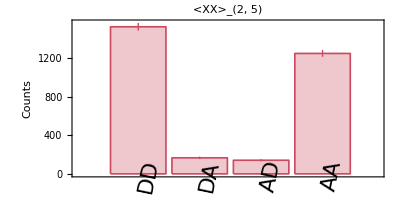

```mathematica
BarChart[Flatten[Accumulate[countsXZXYXYpostSelectAll]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<XX>_(2, 5)"]
```

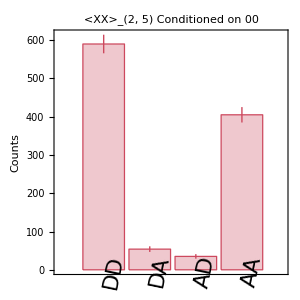

```mathematica
BarChart[Flatten[Accumulate[countsYYXZYYpostSelect00]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<XX>_(2, 5) Conditioned on 00"]
```

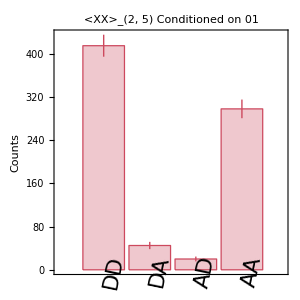

```mathematica
BarChart[Flatten[Accumulate[countsYYXZYYpostSelect01]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<XX>_(2, 5) Conditioned on 01"]
```

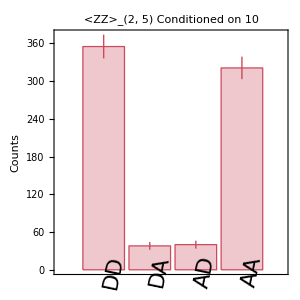

```mathematica
BarChart[Flatten[Accumulate[countsYYXZYYpostSelect10]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(2, 5) Conditioned on 10"]
```

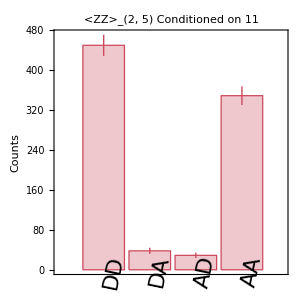

```mathematica
BarChart[Flatten[Accumulate[countsYYXZYYpostSelect11]⟦-1⟧]
,ChartLabels->Placed[bellLabels,{{0.5,0},{0.5,1.1}},Rotate[#,Pi/2.3]&]
,BarChartSettings
,PlotLabel->"<ZZ>_(2, 5) Conditioned on 11"]
```

### AKR Bell_(2,5)

#### Correct normalisation of data

```mathematica
accumulatedDataXYXYZY=Accumulate@countsXYXYZYpostSelectAllvalue;
accumulatedDataXYXYZYerror=Accumulate@countsXYXYZYpostSelectAll;
```

```mathematica
accumulatedDataXZXYXY=Accumulate@countsXZXYXYpostSelectAllvalue;
accumulatedDataXZXYXYerror=Accumulate@countsXZXYXYpostSelectAll;
```

```mathematica
accumulatedDataXYXYZYnorm=N@accumulatedDataXYXYZY⟦#⟧/Total[accumulatedDataXYXYZY⟦#⟧]&/@Range@Length@accumulatedDataXYXYZY;
accumulatedDataXYXYZYnormError=N@accumulatedDataXYXYZYerror⟦#⟧/Total[accumulatedDataXYXYZYerror⟦#⟧]&/@Range@Length@accumulatedDataXYXYZYerror;

accumulatedDataXZXYXYnorm=N@accumulatedDataXZXYXY⟦#⟧/Total[accumulatedDataXZXYXY⟦#⟧]&/@Range@Length@accumulatedDataXZXYXY;
accumulatedDataXZXYXYnormError=N@accumulatedDataXZXYXYerror⟦#⟧/Total[accumulatedDataXZXYXYerror⟦#⟧]&/@Range@Length@accumulatedDataXZXYXYerror;
```

#### Q_Z

Disparity in first and second index

```mathematica
QAB1=N@Total[Table[#⟦i⟧,{i,{2,3}}]]&/@accumulatedDataXYXYZYnorm;
QAB1Error=N@Total[Table[#⟦i⟧,{i,{2,3}}]]&/@accumulatedDataXYXYZYnormError;
```

```mathematica
QzBell25=QAB1;
```

#### Q_X

```mathematica
Qxpositive=N@Total[Table[#⟦i⟧,{i,{1,4}}]]&/@accumulatedDataXZXYXYnorm;
QxpositiveError=N@Total[Table[#⟦i⟧,{i,{1,4}}]]&/@accumulatedDataXZXYXYnormError;
```

```mathematica
Qxnegative=N@Total[Table[#⟦i⟧,{i,{2,3}}]]&/@accumulatedDataXZXYXYnorm;
QxnegativeError=N@Total[Table[#⟦i⟧,{i,{2,3}}]]&/@accumulatedDataXZXYXYnormError;
```

Evaluating Qx is done by computing by evaluating (1 - (QxPositive - QxNegative)/ (QxPositive + QxNegative)) / 2

```mathematica
QxBell25=((1-(Qxpositive⟦#⟧-Qxnegative⟦#⟧)/(Qxnegative⟦#⟧+Qxpositive⟦#⟧))/2)&/@Range[Length@Qxpositive];
QxBell25Error=((1-(QxpositiveError-QxnegativeError)/(QxnegativeError+QxpositiveError))/2)
```

{0.1000.014}

#### AKR

```mathematica
{QxBell25,QzBell25};
```

```mathematica
entropy[x_]:=(-x*Log[2,x])-((1-x)*Log[2,1-x])
```

```mathematica
(* RESULT *)
```

```mathematica
akrBell25=Table[1-entropy[QxBell25⟦i⟧]-entropy[QzBell25⟦i⟧],{i,Range[Length@QxBell25]}];
```

Adding Monte Carlo simultation here based on sampling between the ranges defined by the poissonian uncertainty.

QBER

```mathematica
upperBound=QAB1Error⟦1,1⟧+QAB1Error⟦1,2⟧;
lowerBound=QAB1Error⟦1,1⟧-QAB1Error⟦1,2⟧;
```

```mathematica
errorArrayQBER=Range[lowerBound,upperBound,(upperBound-lowerBound)/1999];
errorArrayQBERsample=Table[RandomSample[errorArrayQBER,1],{i,1,2000}];
```

Qx

```mathematica
upperBound=QxBell25Error⟦1,1⟧+QxBell25Error⟦1,2⟧;
lowerBound=QxBell25Error⟦1,1⟧-QxBell25Error⟦1,2⟧;
```

```mathematica
errorArrayQx=Range[lowerBound,upperBound,(upperBound-lowerBound)/1999];
```

```mathematica
errorArrayQxsample=Table[RandomSample[errorArrayQx,1],{i,1,2000}];
```

AKR

```mathematica
akrArray=1-entropy[errorArrayQxsample⟦#⟧]-entropy[errorArrayQBERsample⟦#⟧]&/@Range[2000];
```

```mathematica
akrStandardDeviation=StandardDeviation[Flatten@akrArray]
akrValue=Mean[Flatten@akrArray]
```

0.0263792

0.0583836

#### Summary

```mathematica
(* RESULT BELL 2,5 *)
```

```mathematica
{{"QBER","Qx","AKR","+-"},{QzBell25⟦-1⟧,QxBell25⟦-1⟧,akrBell25⟦-1⟧,akrStandardDeviation}}//TableForm
```

QBER | Qx | AKR | +-
0.101766 | 0.0997725 | 0.0571566 | 0.0263792

```mathematica
{{"QBER","+-","Qx","+-","AKR","+-"},{QAB1Error⟦1,1⟧,QAB1Error⟦1,2⟧,QxBell25Error⟦1,1⟧,QxBell25Error⟦1,2⟧,akrBell25⟦-1⟧,akrStandardDeviation}}//TableForm
```

QBER | +- | Qx | +- | AKR | +-
0.101766 | 0.00547559 | 0.0997725 | 0.0137305 | 0.0571566 | 0.0263792

### Rates of CKA via Bell states

```mathematica
(* get the max value of the key rate from the two bell state *)
maxValue=Max[{1/akrBell12⟦-1⟧,1/akrBell56⟦-1⟧}];

(* compute funtion *)

akrBell=((1/akrBell25⟦-1⟧)+maxValue)^-1
```

0.0443218